```mathematica
data=Import["/Users/ayushboss/Desktop/Coding/Python/hsmc-stream-cipher-2019-git/7-12-19-3:35/stream-ciphers/python/cluster_data.csv","CSV"];
```

```mathematica
clusterList={};
For[i=1,i≤ Length[data],i++,
madeCluster={data[[i]][[2]],data[[i]][[3]]};
AppendTo[clusterList, madeCluster];
];
```

{{13.1526,26.632},{13.1501,26.654}}

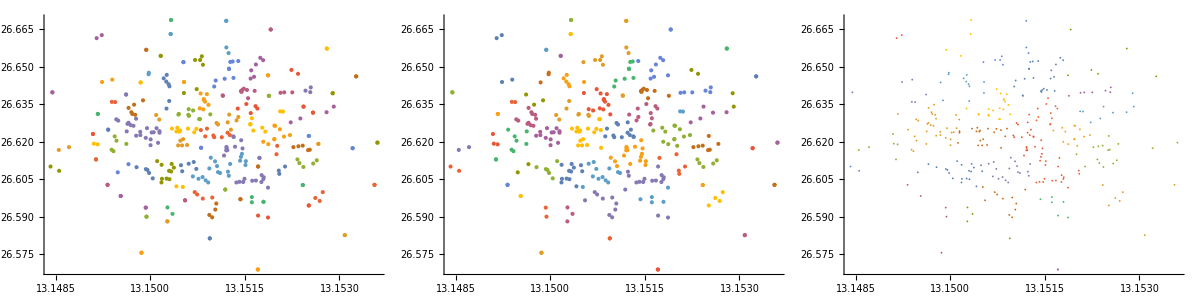

```mathematica
{{13.152560810629144,26.6319995083},{13.150097214438533,26.6539876188}}
Grid[{Table[ListPlot[FindClusters[clusterList,Method->{"NeighborhoodContraction","NeighborhoodRadius"->s}]],{s,{0.06,0.08,0.1}}]},Frame->All]
```

```mathematica
klt=KarhunenLoeveDecomposition[clusterList];
klt
```

{{{230.423,466.476},{0.00530795,0.00530795},{0.0129709,0.0129709},{0.00925549,0.00925549},{0.0189152,0.0189152},{0.006844,0.006844},{0.00855254,0.00855254},{0.0182451,0.0182451},{0.0039201,0.0039201},{0.00273001,0.00273001},{0.0126868,0.0126868},{0.00853276,0.00853276},{0.00456165,0.00456165},{0.0132903,0.0132903},{0.0140885,0.0140885},{0.0120649,0.0120649},{0.0145048,0.0145048},{0.0322143,0.0322143},{0.000791958,0.000791958},{0.000679013,0.000679013},{0.0154359,0.0154359},{0.0136589,0.0136589},{0.0315116,0.0315116},{0.000718512,0.000718512},{0.00256741,0.00256741},{0.0261031,0.0261031},{0.0312825,0.0312825},{0.0336937,0.0336937},{0.0143507,0.0143507},{0.0000985726,0.0000985726},{0.00349329,0.00349329},{0.00331768,0.00331768},{0.00196333,0.00196333},{0.0162024,0.0162024},{0.0274972,0.0274972},{0.0174045,0.0174045},{0.00528596,0.00528596},{0.00654231,0.00654231},{0.0135455,0.0135455},{0.0136697,0.0136697},{0.0255732,0.0255732},{0.00455417,0.00455417},{0.0142348,0.0142348},{0.00324596,0.00324596},{0.014299,0.014299},{0.000380671,0.000380671},{0.0211403,0.0211403},{0.00969966,0.00969966},{0.0222966,0.0222966},{0.0100975,0.0100975},{0.0172235,0.0172235},{0.00974317,0.00974317},{0.00985636,0.00985636},{0.0280815,0.0280815},{0.0154799,0.0154799},{0.0121992,0.0121992},{0.0191419,0.0191419},{0.0241911,0.0241911},{0.0149884,0.0149884},{0.0251844,0.0251844},{0.0112619,0.0112619},{0.00519241,0.00519241},{0.00835105,0.00835105},{0.0162001,0.0162001},{0.00810885,0.00810885},{0.0318228,0.0318228},{0.0156649,0.0156649},{0.00114423,0.00114423},{0.0258554,0.0258554},{0.0161149,0.0161149},{0.007336,0.007336},{0.0209428,0.0209428},{0.0327959,0.0327959},{0.0181065,0.0181065},{0.0159179,0.0159179},{0.00438977,0.00438977},{0.0115181,0.0115181},{0.0124629,0.0124629},{0.0102183,0.0102183},{0.0538179,0.0538179},{0.00503832,0.00503832},{0.0395619,0.0395619},{0.00675163,0.00675163},{0.0294475,0.0294475},{0.0012335,0.0012335},{0.0128124,0.0128124},{0.00491789,0.00491789},{0.0237789,0.0237789},{0.000635802,0.000635802},{0.0000940157,0.0000940157},{0.00287526,0.00287526},{0.000350121,0.000350121},{0.0082951,0.0082951},{0.022564,0.022564},{0.0142051,0.0142051},{0.00934108,0.00934108},{0.0297961,0.0297961},{0.00110461,0.00110461},{0.0120203,0.0120203},{0.00958257,0.00958257},{0.00732765,0.00732765},{0.00405742,0.00405742},{0.0122154,0.0122154},{0.00216379,0.00216379},{0.0289446,0.0289446},{0.0256958,0.0256958},{0.0112558,0.0112558},{0.0127011,0.0127011},{0.0110922,0.0110922},{0.017944,0.017944},{0.000514046,0.000514046},{0.00367131,0.00367131},{0.00979436,0.00979436},{0.00121308,0.00121308},{0.0155603,0.0155603},{0.0106426,0.0106426},{0.00354887,0.00354887},{0.0303728,0.0303728},{0.0415508,0.0415508},{0.00543489,0.00543489},{0.0187066,0.0187066},{0.00269114,0.00269114},{0.00262923,0.00262923},{0.0056426,0.0056426},{0.0218077,0.0218077},{0.00363446,0.00363446},{0.00329374,0.00329374},{0.0190121,0.0190121},{0.0169671,0.0169671},{0.0435605,0.0435605},{0.0245619,0.0245619},{0.0328996,0.0328996},{0.02432,0.02432},{0.0281616,0.0281616},{0.0463146,0.0463146},{0.0173265,0.0173265},{0.0399066,0.0399066},{0.0000172439,0.0000172439},{0.00409313,0.00409313},{0.00962219,0.00962219},{0.00744154,0.00744154},{0.0243297,0.0243297},{0.0126857,0.0126857},{0.0166052,0.0166052},{0.016413,0.016413},{0.000485081,0.000485081},{0.00879965,0.00879965},{0.00288215,0.00288215},{0.00236177,0.00236177},{0.0103267,0.0103267},{0.0297433,0.0297433},{0.0212541,0.0212541},{0.00639481,0.00639481},{0.011276,0.011276},{0.00724558,0.00724558},{0.0123681,0.0123681},{0.00147204,0.00147204},{0.00917881,0.00917881},{0.00116901,0.00116901},{0.0243648,0.0243648},{0.0255983,0.0255983},{0.00467771,0.00467771},{0.0132629,0.0132629},{0.0186354,0.0186354},{0.0266869,0.0266869},{0.0161346,0.0161346},{0.0148059,0.0148059},{0.00908945,0.00908945},{0.0146031,0.0146031},{0.0214168,0.0214168},{0.0353579,0.0353579},{0.0339564,0.0339564},{0.0193231,0.0193231},{0.0185147,0.0185147},{0.0264396,0.0264396},{0.000963263,0.000963263},{0.00715834,0.00715834},{0.024708,0.024708},{0.00757463,0.00757463},{0.0286399,0.0286399},{0.00258538,0.00258538},{0.0116721,0.0116721},{0.00189888,0.00189888},{0.0154419,0.0154419},{0.041029,0.041029},{0.00325741,0.00325741},{0.0192768,0.0192768},{0.0109619,0.0109619},{0.00892607,0.00892607},{0.0191034,0.0191034},{0.0106131,0.0106131},{0.0223143,0.0223143},{0.0195224,0.0195224},{0.0159488,0.0159488},{0.0165695,0.0165695},{0.00282357,0.00282357},{0.00592951,0.00592951},{0.0152638,0.0152638},{0.00538379,0.00538379},{0.00121228,0.00121228},{0.0110319,0.0110319},{0.0166322,0.0166322},{0.00656081,0.00656081},{0.0278254,0.0278254},{0.00017744,0.00017744},{0.00875798,0.00875798},{0.00267136,0.00267136},{0.00817772,0.00817772},{0.0243658,0.0243658},{0.02325,0.02325},{0.00470256,0.00470256},{0.00331737,0.00331737},{0.00555793,0.00555793},{0.00626164,0.00626164},{0.00295716,0.00295716},{0.0099384,0.0099384},{0.0219332,0.0219332},{0.0102293,0.0102293},{0.00849567,0.00849567},{0.0147375,0.0147375},{0.0093021,0.0093021},{0.00103913,0.00103913},{0.0299332,0.0299332},{0.0276288,0.0276288},{0.021419,0.021419},{0.0189809,0.0189809},{0.014464,0.014464},{0.0250153,0.0250153},{0.002005,0.002005},{0.00684575,0.00684575},{0.0274422,0.0274422},{0.0218799,0.0218799},{0.00248541,0.00248541},{0.027506,0.027506},{0.00281916,0.00281916},{0.00619328,0.00619328},{0.0159228,0.0159228},{0.0213087,0.0213087},{0.0112718,0.0112718},{0.00586538,0.00586538},{0.00628518,0.00628518},{0.0220216,0.0220216},{0.00175501,0.00175501},{0.0148351,0.0148351},{0.0266964,0.0266964},{0.00417557,0.00417557},{0.00859714,0.00859714},{0.0169873,0.0169873},{0.0251677,0.0251677},{0.0127911,0.0127911},{0.0134836,0.0134836},{0.0104807,0.0104807},{0.00816561,0.00816561},{0.0431197,0.0431197},{0.0136213,0.0136213},{0.00523626,0.00523626},{0.00315336,0.00315336},{0.0152227,0.0152227},{0.0107358,0.0107358},{0.021464,0.021464},{0.016171,0.016171},{0.0217195,0.0217195},{0.00294736,0.00294736},{0.0099393,0.0099393},{0.00750166,0.00750166},{0.00915327,0.00915327},{0.00242198,0.00242198},{0.00572693,0.00572693},{0.0188337,0.0188337},{0.010274,0.010274},{0.00312522,0.00312522},{0.0186016,0.0186016},{0.0288441,0.0288441},{0.0281905,0.0281905},{0.00827633,0.00827633},{0.0152658,0.0152658},{0.042468,0.042468},{0.0263508,0.0263508},{0.000192845,0.000192845},{0.000474117,0.000474117},{0.0042159,0.0042159},{0.0444046,0.0444046},{0.0228866,0.0228866},{0.0219752,0.0219752},{0.0169625,0.0169625},{0.00701055,0.00701055},{0.00730661,0.00730661},{0.00909892,0.00909892},{0.0162708,0.0162708},{0.00297329,0.00297329},{0.00698561,0.00698561},{0.020387,0.020387},{0.0304449,0.0304449},{0.0142594,0.0142594},{0.00908721,0.00908721},{0.0158125,0.0158125},{0.00479778,0.00479778},{0.0118112,0.0118112},{0.00253645,0.00253645},{0.00120857,0.00120857},{0.0116576,0.0116576},{0.0142131,0.0142131},{0.0293756,0.0293756},{0.0309473,0.0309473},{0.0146961,0.0146961},{0.00239648,0.00239648},{0.0217894,0.0217894}},{{0.0570116,0.0571007,0.0570212,0.0570341,0.0569909,0.0570461,0.0570395,0.0569909,0.0570845,0.0570871,0.0571336,0.0571129,0.0570501,0.0571279,0.0571377,0.0571143,0.0570127,0.0569278,0.0570617,0.0570671,0.0571449,0.0570145,0.0572085,0.0570757,0.0570752,0.0569525,0.0572048,0.0569276,0.0571383,0.0570731,0.0570834,0.0570629,0.0570827,0.0571434,0.0569544,0.0571472,0.057087,0.0570488,0.0570176,0.0571335,0.0569669,0.0570863,0.0571275,0.0570601,0.0570078,0.0570642,0.0571639,0.0570239,0.0569782,0.0570262,0.0569947,0.057114,0.0570247,0.0571934,0.0570022,0.0570239,0.0569899,0.057168,0.0571365,0.0569632,0.0570161,0.057094,0.0571049,0.0571338,0.0570354,0.0569317,0.0571342,0.0570678,0.0571781,0.0571419,0.0571064,0.0569739,0.0572083,0.0569947,0.0571332,0.0570807,0.0570141,0.0570147,0.0570239,0.0568403,0.0570496,0.0572456,0.0570987,0.0569402,0.0570799,0.0570145,0.0570498,0.0571701,0.0570659,0.05707,0.0570501,0.0570762,0.0570304,0.0569713,0.0570159,0.0571039,0.0571987,0.0570706,0.057018,0.0571088,0.057045,0.0570883,0.0571222,0.0570749,0.0569446,0.0569604,0.0570184,0.0570179,0.0571211,0.0569959,0.0570697,0.0570594,0.0571085,0.0570614,0.056999,0.0570256,0.0570812,0.0572096,0.0572426,0.057048,0.0571496,0.0570601,0.0570635,0.057102,0.0571653,0.057093,0.057081,0.0571528,0.0569941,0.0568764,0.0569623,0.0569315,0.0571778,0.057194,0.0572684,0.0571439,0.0568962,0.05706,0.0570561,0.0570265,0.0570973,0.0569652,0.0570109,0.0571448,0.0569978,0.0570677,0.0571067,0.0570807,0.0570757,0.0571149,0.0569372,0.0571599,0.0570443,0.0570245,0.0571059,0.0570132,0.0570787,0.0571078,0.0570635,0.0569758,0.0571822,0.0570869,0.0571224,0.0571452,0.0569547,0.0571428,0.0570062,0.0571037,0.0571398,0.0571666,0.0572195,0.0572182,0.0569893,0.0569931,0.0571806,0.057056,0.0570955,0.0571714,0.0571044,0.0571983,0.05708,0.0570208,0.0570768,0.0570002,0.0572446,0.0570862,0.056985,0.057112,0.0570389,0.056989,0.0571103,0.0571645,0.0569881,0.0570004,0.0571451,0.0570821,0.0570482,0.0570108,0.0571018,0.0570661,0.0571162,0.0571421,0.0570931,0.0571905,0.0570691,0.0570327,0.0570795,0.057047,0.056964,0.0571758,0.057091,0.0570869,0.0570966,0.0570997,0.0570554,0.0571168,0.0571662,0.0571137,0.0570273,0.0570078,0.0570392,0.0570672,0.0571991,0.0571941,0.0571688,0.056991,0.0571378,0.0571758,0.0570578,0.0570987,0.0569575,0.0571625,0.0570789,0.0569545,0.0570556,0.057044,0.0569937,0.057163,0.0570177,0.0570462,0.0570918,0.0569802,0.0570823,0.0571314,0.0569514,0.0570856,0.0571016,0.0570007,0.0571814,0.057012,0.0571308,0.0570219,0.057106,0.0568926,0.0571369,0.0570518,0.0570795,0.0570003,0.0571169,0.0569755,0.0570008,0.0569778,0.0570793,0.0570216,0.0571055,0.0571127,0.0570528,0.0570374,0.0569865,0.057029,0.0570558,0.0571605,0.0569521,0.0571943,0.0570371,0.0571373,0.0572474,0.0571873,0.0570629,0.0570738,0.0570828,0.0572632,0.0571647,0.0571538,0.0569997,0.0570469,0.0571109,0.0570206,0.0571405,0.0570825,0.0570285,0.0571562,0.0569452,0.0571323,0.0570321,0.0570062,0.0570913,0.0571188,0.0570784,0.0570666,0.0571149,0.0571309,0.0571962,0.0569359,0.0570016,0.0570656,0.0571682},{-0.574309,0.0465809,0.000333576,-0.0415999,-0.00376023,-0.0374094,-0.0342681,0.0114787,-0.0020173,-0.0385824,-0.00410972,-0.0658929,0.0357306,0.0426973,0.0785102,-0.0451057,0.0382662,0.0389241,0.0701923,-0.0369337,0.0822766,0.0375428,0.0364465,-0.0438526,0.0484475,0.010729,-0.0449754,-0.0289579,0.0747959,-0.0353299,-0.0320205,0.0373186,-0.0320628,0.0780946,-0.00123253,-0.0722426,0.0859632,-0.038463,0.0116393,-0.00179893,-0.00349513,0.00556142,0.0836237,-0.0329288,-0.0809672,0.0416922,-0.0699426,-0.0715422,0.0790292,-0.0442244,-0.0304089,-0.027471,0.00161257,0.00443897,0.0383683,0.070491,0.0812953,0.0356809,0.0480206,-0.0435862,-0.0759953,-0.0424474,-0.00223914,0.0112804,-0.0447808,-0.0439739,0.0719957,-0.0815627,-0.00188606,-0.0325466,-0.0333402,0.074101,-0.0686871,0.0739702,0.0501407,-0.0409573,0.0325649,-0.038437,-0.034774,0.0408711,-0.0331609,-0.0393288,-0.00543109,0.0414699,0.0788768,0.00702971,-0.00663381,-0.000253304,0.0341465,0.010173,-0.0821077,-0.0273591,-0.00497438,-0.0027561,0.0356777,-0.0267909,-0.000396987,0.00783322,-0.0385168,-0.0680254,0.0882898,0.00592821,-0.078748,0.0413038,-0.0272523,-0.031427,-0.0384731,0.0480058,0.0338525,0.000764404,0.0404885,0.0747363,-0.0355407,0.00801434,-0.0757918,-0.0385849,0.0416907,-0.0332087,-0.0015514,0.0317473,-0.070497,-0.0407271,-0.0294457,0.0329571,-0.0442547,0.0876107,0.00197593,-0.00648551,0.0881955,0.00756157,0.0439537,0.0828985,-0.0696621,0.0092012,-0.00641957,0.038727,-0.067484,-0.0279762,0.00992311,-0.0685097,0.0431303,0.0461948,0.00581977,0.00796358,-0.0304834,-0.0426934,-0.00590997,0.00942335,0.00972791,0.0381768,0.0500503,0.0401859,0.071642,0.0789276,-0.0671222,-0.0373385,0.0737732,0.000768116,0.0478954,0.00616052,-0.030848,0.0782693,0.0354448,0.00273429,-0.00258198,-0.0365088,-0.0357707,-0.0743485,-0.0268865,0.0494535,0.0346993,-0.0397815,0.0739167,-0.0360585,-0.00292079,0.0435169,0.00083853,0.07271,0.00647231,0.0463263,-0.0666291,-0.00528505,-0.0446175,0.0413041,-0.0821789,-0.0789957,0.0381089,-0.0343942,0.0726089,0.0011727,-0.067335,0.0496449,-0.0797217,0.00273702,0.0844233,-0.00140555,-0.0715404,0.0447153,0.0335351,-0.0341631,-0.0294436,0.0401686,-0.00201416,0.0116703,0.0104835,0.0475754,0.00523831,0.0804569,0.0100672,-0.0780002,0.00158722,-0.0391333,-0.0443097,0.0476902,0.000784638,0.0440454,-0.0711352,0.0363823,-0.0360476,0.0408093,-0.0359714,0.0031549,0.00802123,0.0447367,-0.0334064,0.010453,0.00614916,0.005777,0.050136,-0.0331515,-0.070447,-0.070419,0.0108085,0.0835529,-0.00541175,-0.031843,-0.026949,-0.000610117,0.0871741,-0.0658438,-0.0288322,-0.0684067,0.00967532,-0.0275555,0.0093802,-0.0368453,0.0465533,-0.0408301,0.0756736,0.00630157,-0.0376806,-0.0691382,0.0413346,0.0322001,0.0733608,0.0352761,-0.038933,-0.0747196,0.0888239,-0.0440961,-0.0368739,0.0820832,0.0382965,-0.0301827,0.00069256,-0.0374862,-0.00274018,0.00288818,0.0416167,0.00952048,0.0744109,-0.0392068,-0.0335231,-0.00448713,0.0702127,0.00621929,0.0402478,-0.029538,-0.0339867,0.0427614,0.0104013,-0.0708105,0.00616327,-0.0752864,-0.0308878,0.0798463,0.0491706,0.0343116,0.00429742,0.0384181,-0.0335263,0.0395508,0.0409697,0.0736562,-0.0676575,0.000329445,-0.0777645,0.0400943,0.0716212,0.0832407,-0.0327415,-0.0428642,0.0411297,0.0117328,-0.0781424,0.0396556,-0.041586},{-0.0386725,-0.0334041,0.997004,-0.00177832,-0.00287567,-0.00190072,-0.00199166,-0.00331852,-0.00293122,-0.00186879,-0.00287299,-0.0010765,-0.00402637,-0.0042329,-0.00527413,-0.00168064,-0.0040981,-0.00411277,-0.00502843,-0.00191565,-0.00538395,-0.00407717,-0.00405547,-0.00171504,-0.00439724,-0.00329472,-0.00168917,-0.00214012,-0.00516622,-0.00196257,-0.00205928,-0.00407319,-0.00205801,-0.00526235,-0.00294722,-0.000893775,-0.00548805,-0.00187025,-0.00332458,-0.00294013,-0.00288212,-0.00315155,-0.00542219,-0.00203166,-0.000632934,-0.00420035,-0.000961485,-0.000907671,-0.00528085,-0.00170164,-0.00210147,-0.00219309,-0.00303358,-0.00312455,-0.00410051,-0.00503513,-0.00534732,-0.0040311,-0.00438804,-0.00171689,-0.000777857,-0.00175683,-0.00292585,-0.00332023,-0.00168595,-0.00170397,-0.00508464,-0.000618774,-0.00293994,-0.00204705,-0.00202213,-0.00513741,-0.0010003,-0.0051347,-0.00444948,-0.00179944,-0.00393249,-0.00186922,-0.00197615,-0.00416476,-0.00202437,-0.0018554,-0.00283276,-0.0041874,-0.00528175,-0.00319046,-0.00279525,-0.00298697,-0.00398116,-0.00328472,-0.000602011,-0.00219436,-0.00284246,-0.00290382,-0.00402304,-0.00221233,-0.00298429,-0.00321675,-0.00186707,-0.00101432,-0.00555346,-0.00316232,-0.000703419,-0.00418962,-0.00219057,-0.00207008,-0.00186836,-0.0043814,-0.00397551,-0.00300742,-0.00416566,-0.00516035,-0.0019583,-0.00322153,-0.000782873,-0.00186549,-0.00420119,-0.00203136,-0.00295304,-0.0039105,-0.000944629,-0.00180505,-0.00213306,-0.00394849,-0.00170804,-0.00553624,-0.00304708,-0.00280496,-0.00554806,-0.00319869,-0.00426073,-0.00539085,-0.000970362,-0.00326297,-0.00281292,-0.00411836,-0.00101891,-0.00217558,-0.00327672,-0.000995931,-0.00424387,-0.00432601,-0.00315511,-0.00322442,-0.00209946,-0.0017483,-0.00281927,-0.00326349,-0.00327208,-0.00410085,-0.00443658,-0.00416159,-0.00506965,-0.00528033,-0.00104041,-0.00190106,-0.00513338,-0.00301339,-0.00438058,-0.00316317,-0.00209853,-0.00526447,-0.00402185,-0.00307249,-0.00290802,-0.00193196,-0.00194625,-0.000830298,-0.00221143,-0.00443126,-0.00400528,-0.0018408,-0.00513287,-0.0019372,-0.00291,-0.00425295,-0.00301479,-0.00510734,-0.00317897,-0.00434204,-0.00105338,-0.00283293,-0.00169287,-0.00418572,-0.000610127,-0.000694333,-0.00409207,-0.0019918,-0.00509746,-0.00301893,-0.00103446,-0.00443671,-0.000668098,-0.00306498,-0.00544635,-0.00294888,-0.000908997,-0.0042854,-0.00396528,-0.00199611,-0.00213588,-0.00416015,-0.00293177,-0.00333454,-0.00329369,-0.00436966,-0.00314181,-0.00532595,-0.00327609,-0.000727956,-0.00303631,-0.00185277,-0.00170285,-0.00437651,-0.00301112,-0.00427149,-0.000926947,-0.00404864,-0.00193931,-0.00417174,-0.00194215,-0.00308062,-0.00322894,-0.00429563,-0.00202348,-0.00328871,-0.00317133,-0.0031625,-0.00444539,-0.00202722,-0.00093602,-0.000947571,-0.00330365,-0.00541107,-0.00283107,-0.00206237,-0.00220196,-0.00297623,-0.00551961,-0.00107443,-0.00215237,-0.000996498,-0.00327089,-0.00219154,-0.00325546,-0.00191919,-0.00434357,-0.00179894,-0.00519399,-0.00316917,-0.00189728,-0.000977424,-0.00419215,-0.00391553,-0.00512444,-0.00401325,-0.0018582,-0.000814098,-0.00557275,-0.00170271,-0.00191392,-0.00536958,-0.00410246,-0.00210945,-0.00301107,-0.00190198,-0.00290856,-0.00307131,-0.00419409,-0.0032636,-0.00515071,-0.00185448,-0.00200874,-0.0028652,-0.00502773,-0.00317334,-0.00416797,-0.00213686,-0.00200107,-0.00423193,-0.00329202,-0.000941464,-0.00317315,-0.000805668,-0.00208781,-0.0053082,-0.00442012,-0.00398359,-0.00311766,-0.00410616,-0.00201264,-0.00414294,-0.00417312,-0.00513279,-0.00102099,-0.00299532,-0.000730382,-0.00415678,-0.00507083,-0.00540787,-0.00203998,-0.00174665,-0.00419092,-0.00332301,-0.000714698,-0.00414124,-0.00178575},{-0.0632517,0.00719451,-0.00310379,0.996483,-0.00314245,-0.00347681,-0.00344552,-0.00299239,-0.00313039,-0.00349059,-0.00315367,-0.00376093,-0.0027568,-0.00269244,-0.00234032,-0.00355631,-0.0027298,-0.00271869,-0.00241808,-0.00347327,-0.00230362,-0.00273702,-0.00275838,-0.00354187,-0.00263294,-0.00299768,-0.00355996,-0.00338713,-0.00237692,-0.0034578,-0.00342578,-0.00274186,-0.00342616,-0.00234472,-0.00311557,-0.00382533,-0.00226416,-0.00348733,-0.00299226,-0.00313091,-0.00313853,-0.00305585,-0.00228941,-0.00343345,-0.00390364,-0.00269887,-0.00380359,-0.00381172,-0.00232651,-0.00354283,-0.00340508,-0.00338264,-0.00309139,-0.00307275,-0.00272822,-0.00241308,-0.00230484,-0.00276372,-0.00264049,-0.00353312,-0.00385514,-0.00352903,-0.00313368,-0.00300213,-0.00354882,-0.00353522,-0.00240428,-0.00391278,-0.00313419,-0.00343414,-0.00344003,-0.00237481,-0.00379365,-0.00237723,-0.00261943,-0.00351363,-0.00278602,-0.00348522,-0.00344965,-0.00269475,-0.00343517,-0.00350658,-0.00316478,-0.0026943,-0.00233356,-0.00303749,-0.00317396,-0.00311768,-0.00277326,-0.00300956,-0.00391718,-0.00337948,-0.00315656,-0.00313149,-0.00275546,-0.0033754,-0.00312066,-0.00303263,-0.00348618,-0.00378171,-0.00223896,-0.00305236,-0.00388803,-0.00270327,-0.00337126,-0.00341323,-0.00348577,-0.00263417,-0.00277916,-0.00309817,-0.00271102,-0.00237321,-0.00346181,-0.00303034,-0.0038522,-0.00348727,-0.0026998,-0.00344435,-0.00313442,-0.00279591,-0.00380827,-0.00351025,-0.00339934,-0.00278694,-0.00355071,-0.00224827,-0.00309087,-0.00317811,-0.00223712,-0.00302473,-0.00267104,-0.00228587,-0.00380158,-0.00302588,-0.00318376,-0.00273241,-0.00376479,-0.00338468,-0.00301126,-0.00378199,-0.0026865,-0.00264913,-0.00304921,-0.00303539,-0.00340597,-0.00353002,-0.00316993,-0.00301752,-0.00301425,-0.00273624,-0.00260964,-0.00271891,-0.00240286,-0.00233003,-0.00377266,-0.00347432,-0.00238375,-0.00310423,-0.00263774,-0.00304393,-0.00341961,-0.00233992,-0.00276356,-0.00308691,-0.00312888,-0.00347321,-0.0034585,-0.0038437,-0.00337829,-0.00262802,-0.00277619,-0.00350955,-0.00237746,-0.00346062,-0.00314452,-0.00268045,-0.00310287,-0.00239927,-0.00304787,-0.00266054,-0.00376639,-0.0031591,-0.00354946,-0.0026992,-0.00392848,-0.0038885,-0.00272983,-0.00345071,-0.00239304,-0.00309377,-0.00377499,-0.00262602,-0.00389031,-0.00307899,-0.00228249,-0.00312424,-0.00381302,-0.00266618,-0.00278124,-0.00344593,-0.00340219,-0.00271811,-0.00313083,-0.00300138,-0.00300645,-0.00263921,-0.00305867,-0.0023162,-0.00300482,-0.00388358,-0.00309525,-0.00349601,-0.00354751,-0.00264174,-0.00310121,-0.00267856,-0.00381546,-0.00275385,-0.00346237,-0.00270449,-0.00346227,-0.00307852,-0.00303778,-0.00267597,-0.00344408,-0.0030025,-0.00305288,-0.00305861,-0.00261537,-0.00343775,-0.00379731,-0.00380821,-0.00300378,-0.00228068,-0.00316224,-0.00342188,-0.00337095,-0.00312081,-0.00224846,-0.00375682,-0.00339484,-0.00377846,-0.00301513,-0.00338442,-0.0030109,-0.00347341,-0.00265303,-0.00350802,-0.00237063,-0.00304452,-0.0034841,-0.00378793,-0.00270466,-0.00278298,-0.00239098,-0.00276137,-0.00349363,-0.00384171,-0.00223762,-0.00353881,-0.00346907,-0.00229642,-0.00273313,-0.00340431,-0.00310485,-0.0034812,-0.00313578,-0.00307952,-0.00269537,-0.00301375,-0.00237622,-0.00350074,-0.00343342,-0.00316069,-0.00241654,-0.00305216,-0.00272307,-0.00340699,-0.00344402,-0.00268886,-0.00300801,-0.00381755,-0.0030542,-0.00385566,-0.00341006,-0.00232221,-0.00262777,-0.00276917,-0.00307126,-0.0027321,-0.00343761,-0.00272497,-0.0026995,-0.00238782,-0.00377391,-0.00310301,-0.00387666,-0.00271757,-0.00240492,-0.00228986,-0.0034346,-0.00353515,-0.0027116,-0.00298689,-0.00387549,-0.002719,-0.00352459},{-0.0410506,-0.0294224,-0.00300507,-0.00194711,0.9971,-0.00205353,-0.00213249,-0.00328484,-0.00294905,-0.00202608,-0.0028988,-0.00133796,-0.0039002,-0.00408017,-0.0049848,-0.00186282,-0.00396225,-0.0039744,-0.00477082,-0.00206665,-0.00508027,-0.00394409,-0.0039266,-0.00189243,-0.00422257,-0.0032639,-0.00187087,-0.00226067,-0.00489106,-0.00210745,-0.00219154,-0.00394097,-0.00219044,-0.00497461,-0.00296202,-0.00117946,-0.00517029,-0.00202708,-0.0032903,-0.00295713,-0.00290555,-0.00314047,-0.00511336,-0.00216738,-0.000951877,-0.00405145,-0.0012384,-0.00119067,-0.00498952,-0.00188044,-0.00222757,-0.002308,-0.00303754,-0.00311776,-0.00396428,-0.00477638,-0.00504735,-0.00390515,-0.00421502,-0.00189324,-0.00107784,-0.00192887,-0.00294452,-0.00328734,-0.00186688,-0.0018818,-0.00482016,-0.000939999,-0.00295728,-0.00218133,-0.00215943,-0.00486488,-0.00127244,-0.00486267,-0.00426836,-0.00196578,-0.00381839,-0.00202594,-0.0021189,-0.00401895,-0.00216097,-0.00201556,-0.00286361,-0.00403932,-0.00499102,-0.00317377,-0.00283068,-0.00299808,-0.00386104,-0.00325604,-0.000925311,-0.00230884,-0.00287155,-0.00292444,-0.00389707,-0.00232464,-0.00299595,-0.003197,-0.0020241,-0.00128391,-0.00522682,-0.00314984,-0.00101392,-0.00404221,-0.00230462,-0.00220006,-0.00202522,-0.00420841,-0.00385652,-0.00301462,-0.00402135,-0.00488541,-0.00210399,-0.00320108,-0.00108207,-0.00202278,-0.0040523,-0.00216818,-0.00296912,-0.00379953,-0.00122366,-0.00197051,-0.0022555,-0.00383292,-0.00188698,-0.0052122,-0.00304967,-0.00283983,-0.00522177,-0.00317994,-0.00410319,-0.00508475,-0.00124621,-0.00323802,-0.00284757,-0.00398078,-0.00128641,-0.00229241,-0.003249,-0.00126736,-0.00408949,-0.00415992,-0.00314303,-0.00320419,-0.00222585,-0.00192127,-0.00285194,-0.00323767,-0.0032451,-0.00396536,-0.00425578,-0.00401845,-0.0048065,-0.00498939,-0.00130656,-0.0020536,-0.00486212,-0.00302059,-0.00420802,-0.00314978,-0.00222633,-0.00497605,-0.00389679,-0.00307219,-0.00292797,-0.00208135,-0.00209281,-0.00112401,-0.00232411,-0.00425277,-0.00388307,-0.00200269,-0.00486104,-0.00208485,-0.00293129,-0.00409709,-0.00302172,-0.00484014,-0.00316441,-0.00417549,-0.00131765,-0.0028632,-0.00187317,-0.00403829,-0.000933733,-0.00100577,-0.00395682,-0.00213312,-0.00483063,-0.00302456,-0.00130142,-0.00425749,-0.000982287,-0.00306465,-0.00513447,-0.00296437,-0.00119199,-0.00412496,-0.0038475,-0.00213654,-0.00225832,-0.00401708,-0.00294958,-0.00330017,-0.00326383,-0.00419832,-0.00313195,-0.00502918,-0.00324779,-0.00103561,-0.00304038,-0.00201216,-0.00188199,-0.00420474,-0.00301825,-0.00411362,-0.00120842,-0.00392,-0.00208692,-0.0040262,-0.00208947,-0.00307871,-0.0032085,-0.00413514,-0.00216104,-0.00325895,-0.00315801,-0.00315061,-0.00426429,-0.00216379,-0.00121483,-0.00122631,-0.00327255,-0.00510248,-0.00286183,-0.00219395,-0.00231486,-0.00298869,-0.00519722,-0.0013357,-0.00227247,-0.00126753,-0.00324412,-0.00230678,-0.00322979,-0.00206985,-0.00417614,-0.00196479,-0.00491549,-0.00315525,-0.00205114,-0.00125125,-0.00404462,-0.0038028,-0.00485476,-0.00388882,-0.00201683,-0.00110921,-0.00524409,-0.00188101,-0.00206467,-0.0050666,-0.00396652,-0.00223469,-0.00301856,-0.00205509,-0.00292913,-0.00307041,-0.00404546,-0.00323741,-0.00487701,-0.00201417,-0.00214671,-0.00289247,-0.00477004,-0.00315976,-0.00402461,-0.00225967,-0.00214082,-0.00407895,-0.00326247,-0.00122171,-0.00315978,-0.00110297,-0.00221574,-0.00501376,-0.0042427,-0.00386283,-0.00311141,-0.00396975,-0.00215064,-0.00400223,-0.00402696,-0.00486198,-0.00128917,-0.00300418,-0.00103712,-0.00401398,-0.00480777,-0.00510049,-0.002175,-0.00192028,-0.00404419,-0.00328836,-0.00102287,-0.00400011,-0.00195451},{-0.0608046,0.00312973,-0.00309374,-0.00334405,-0.00311646,0.99668,-0.0033007,-0.00302576,-0.00311117,-0.00332897,-0.00312629,-0.00349293,-0.00288461,-0.00284736,-0.00263472,-0.00336927,-0.00286749,-0.00285896,-0.0026801,-0.00331806,-0.00261269,-0.00287189,-0.00288895,-0.00335972,-0.00281027,-0.00302813,-0.00337341,-0.00326301,-0.00265686,-0.00330885,-0.00328971,-0.00287585,-0.00328992,-0.0026375,-0.00309944,-0.00353259,-0.0025876,-0.00332617,-0.00302625,-0.00311253,-0.00311358,-0.00306615,-0.00260373,-0.00329385,-0.00357695,-0.00284989,-0.00351981,-0.00352173,-0.00262297,-0.00335924,-0.0032753,-0.00326429,-0.00308632,-0.00307865,-0.0028663,-0.00267628,-0.00261012,-0.00289131,-0.00281615,-0.00335203,-0.00354781,-0.00335235,-0.0031136,-0.00303469,-0.00336305,-0.00335262,-0.00267331,-0.00358376,-0.00311547,-0.00329601,-0.00329881,-0.00265207,-0.00351474,-0.00265398,-0.00280334,-0.00334275,-0.0029015,-0.00332417,-0.00330287,-0.00284262,-0.00329466,-0.00334201,-0.00313226,-0.00284448,-0.0026294,-0.00305352,-0.00313677,-0.00310532,-0.00289489,-0.00303782,-0.00358604,-0.00326156,-0.00312584,-0.00310942,-0.00288307,-0.00325969,-0.00310773,-0.00305178,-0.00332482,-0.0035054,-0.00257147,-0.00306408,-0.00356996,-0.00285278,-0.00325379,-0.00327949,-0.00332458,-0.00280979,-0.00289964,-0.0030898,-0.00285735,-0.00265293,-0.00331202,-0.0030502,-0.00354567,-0.00332564,-0.00285082,-0.00330363,-0.00311698,-0.00290821,-0.00352233,-0.00334027,-0.0032733,-0.00290394,-0.00336697,-0.00257812,-0.00308721,-0.00314148,-0.00256927,-0.00304286,-0.00283089,-0.0025974,-0.00351889,-0.00305034,-0.00314736,-0.00287187,-0.00349064,-0.00326436,-0.00303855,-0.00350382,-0.00284312,-0.00281771,-0.00306053,-0.00305503,-0.00327591,-0.00335238,-0.00313555,-0.00304286,-0.00304078,-0.00287356,-0.00279324,-0.00286405,-0.00267053,-0.00262609,-0.00349987,-0.00331755,-0.00265971,-0.00309585,-0.00281292,-0.00305659,-0.00328809,-0.00263339,-0.00289024,-0.00308618,-0.00310748,-0.00331965,-0.00330783,-0.00354276,-0.0032622,-0.00280925,-0.00289995,-0.00334322,-0.00265401,-0.00330884,-0.00312177,-0.00283858,-0.00309477,-0.00267107,-0.00306171,-0.00282959,-0.00349553,-0.00312716,-0.00336433,-0.00284872,-0.00359702,-0.00356948,-0.00286692,-0.00330539,-0.00266448,-0.003087,-0.00350138,-0.00280799,-0.00356847,-0.00307831,-0.00259992,-0.0031074,-0.00352304,-0.00282899,-0.00290049,-0.00330152,-0.00327615,-0.00286318,-0.00311162,-0.00303545,-0.00303592,-0.00281316,-0.00306771,-0.00261821,-0.00303269,-0.00356841,-0.00309007,-0.00333223,-0.00336357,-0.00281611,-0.00309291,-0.00283874,-0.00352703,-0.00288418,-0.00331063,-0.00285208,-0.00331082,-0.00307945,-0.00305764,-0.00283882,-0.00330259,-0.00303187,-0.00306545,-0.00306973,-0.00279928,-0.00329727,-0.0035116,-0.00352257,-0.00303452,-0.00259476,-0.00312981,-0.00328651,-0.00325465,-0.00310705,-0.00257663,-0.00348902,-0.00327118,-0.00350069,-0.00304145,-0.00326573,-0.0030361,-0.00331854,-0.00282298,-0.00333766,-0.00265398,-0.00305772,-0.00332597,-0.00350731,-0.00285429,-0.00289707,-0.00266533,-0.0028874,-0.00333064,-0.00353936,-0.0025722,-0.00335572,-0.00331411,-0.00260477,-0.00287092,-0.00327541,-0.00309618,-0.00332383,-0.00311375,-0.00307942,-0.00284612,-0.00303948,-0.00265467,-0.00333667,-0.00329152,-0.00313184,-0.00267865,-0.00306501,-0.00286843,-0.00328057,-0.00330029,-0.00284405,-0.00303716,-0.00353036,-0.00306683,-0.00355107,-0.00327842,-0.00262184,-0.0028079,-0.00289145,-0.00307662,-0.00287037,-0.00329569,-0.00286763,-0.00284773,-0.00266332,-0.00349905,-0.00309295,-0.00356243,-0.00286236,-0.00267251,-0.0026027,-0.00329571,-0.00335683,-0.0028604,-0.00302125,-0.0035598,-0.00286209,-0.00335125},{-0.0589594,0.000091663,-0.00308538,-0.00321359,-0.00309619,-0.0032015,0.996808,-0.00304986,-0.00309596,-0.00320729,-0.00310498,-0.00329173,-0.00297932,-0.00296234,-0.00285398,-0.00322859,-0.00296959,-0.00296299,-0.00287515,-0.00320119,-0.00284292,-0.00297188,-0.00298572,-0.0032227,-0.00294201,-0.00305006,-0.0032331,-0.00316939,-0.0028653,-0.00319664,-0.00318713,-0.00297518,-0.00318722,-0.00285555,-0.00308654,-0.00331289,-0.00282857,-0.00320485,-0.00305081,-0.00309795,-0.00309409,-0.00307301,-0.00283788,-0.00318863,-0.00333187,-0.00296195,-0.0033068,-0.00330409,-0.00284377,-0.00322114,-0.00317743,-0.00317496,-0.00308169,-0.00308222,-0.0029687,-0.0028722,-0.00283751,-0.00298585,-0.00294663,-0.0032158,-0.00331721,-0.00321941,-0.00309774,-0.00305819,-0.00322334,-0.00321527,-0.0028736,-0.00333693,-0.00310063,-0.0031919,-0.00319239,-0.00285852,-0.00330539,-0.00286004,-0.00294,-0.00321416,-0.002987,-0.00320292,-0.00319229,-0.00295233,-0.00318877,-0.00321813,-0.00310711,-0.00295592,-0.00284973,-0.00306466,-0.00310812,-0.00309523,-0.00298499,-0.00305811,-0.00333763,-0.00317257,-0.00310203,-0.00309208,-0.00297763,-0.00317234,-0.00309722,-0.00306525,-0.00320335,-0.00329799,-0.00281922,-0.00307201,-0.00333132,-0.00296371,-0.00316512,-0.00317867,-0.00320323,-0.00294025,-0.00298887,-0.00308271,-0.00296591,-0.00286121,-0.0031992,-0.0030642,-0.00331566,-0.00320396,-0.00296288,-0.00319758,-0.0031031,-0.00299132,-0.00330771,-0.00321235,-0.00317823,-0.00299056,-0.00322877,-0.00282389,-0.00308363,-0.00311325,-0.00281675,-0.00305557,-0.00294956,-0.00282947,-0.0033067,-0.00306777,-0.0031193,-0.00297528,-0.00328484,-0.00317357,-0.00305812,-0.00329501,-0.00295937,-0.0029429,-0.00306815,-0.00306888,-0.00317782,-0.00321874,-0.003109,-0.00306097,-0.00305977,-0.00297539,-0.00292966,-0.00297171,-0.00286981,-0.00284658,-0.00329508,-0.00319951,-0.00286519,-0.00308875,-0.00294305,-0.00306521,-0.00318891,-0.00285196,-0.0029841,-0.0030848,-0.00309065,-0.003204,-0.00319436,-0.00331694,-0.00317457,-0.0029439,-0.00299162,-0.00321803,-0.00285991,-0.00319452,-0.00310391,-0.00295596,-0.00308787,-0.00287344,-0.00307122,-0.00295512,-0.00329218,-0.00310245,-0.00322508,-0.00295967,-0.00334838,-0.00333012,-0.00296856,-0.0031959,-0.00286657,-0.00308109,-0.00329597,-0.0029432,-0.00332702,-0.00307695,-0.0028364,-0.00309397,-0.0033054,-0.00294987,-0.00298879,-0.00319271,-0.00318107,-0.0029708,-0.00309642,-0.00306008,-0.00305712,-0.00294236,-0.00307363,-0.00284315,-0.00305269,-0.00333194,-0.00308535,-0.00320895,-0.00322522,-0.00294564,-0.00308586,-0.00295765,-0.00331055,-0.00298078,-0.00319634,-0.00296159,-0.00319675,-0.0030793,-0.00307164,-0.00295973,-0.00319597,-0.00305298,-0.00307401,-0.0030772,-0.00293593,-0.0031914,-0.00329716,-0.00330818,-0.00305666,-0.00282873,-0.00310472,-0.00318446,-0.00316686,-0.00309593,-0.00282114,-0.00328797,-0.00317789,-0.00329219,-0.00306029,-0.00317615,-0.0030541,-0.00320192,-0.0029492,-0.00320945,-0.00286497,-0.00306674,-0.00320691,-0.00329667,-0.0029653,-0.00298153,-0.00286959,-0.00298079,-0.00320794,-0.00331247,-0.00282149,-0.00321801,-0.00319742,-0.00283446,-0.0029731,-0.0031782,-0.00308886,-0.00320534,-0.00309644,-0.0030785,-0.00295798,-0.00305787,-0.00286201,-0.00321316,-0.0031846,-0.00310942,-0.00287377,-0.00307377,-0.00297626,-0.00318521,-0.003192,-0.00295922,-0.00305811,-0.00331481,-0.00307543,-0.00332251,-0.00317916,-0.002845,-0.00294174,-0.00298204,-0.00307979,-0.0029729,-0.00318874,-0.00297344,-0.00295771,-0.00286845,-0.00329272,-0.00308459,-0.00332666,-0.00296977,-0.00287172,-0.00283574,-0.00319103,-0.00322268,-0.00297081,-0.00304611,-0.00332295,-0.00296822,-0.00322081},{-0.0321216,-0.044179,-0.00296623,-0.00131526,-0.00280341,-0.00148093,-0.00160432,0.996596,-0.00287691,-0.00143685,-0.00279704,-0.000362508,-0.00436191,-0.00464034,-0.00605141,-0.00118133,-0.00445984,-0.00448136,-0.00571985,-0.00150075,-0.00620013,-0.00443145,-0.00439831,-0.00122869,-0.00486409,-0.00337211,-0.00119115,-0.00180767,-0.00590514,-0.00156424,-0.00169512,-0.00442512,-0.00169341,-0.00603533,-0.00290109,-0.000114191,-0.00634233,-0.00143957,-0.00341134,-0.00288805,-0.00281261,-0.00317551,-0.00625229,-0.00165813,0.00023667,-0.00459745,-0.000205643,-0.000135392,-0.00606359,-0.00121148,-0.001754,-0.00187589,-0.00301679,-0.00313685,-0.00446332,-0.00572966,-0.00615346,-0.00436606,-0.00485045,-0.00123335,0.0000404052,-0.00128498,-0.00286923,-0.00340322,-0.00119004,-0.00121645,-0.00579464,0.000257015,-0.00288693,-0.00167742,-0.00164433,-0.00586926,-0.000257395,-0.00586518,-0.00493378,-0.00134298,-0.00423536,-0.00143883,-0.00158358,-0.00455351,-0.00164845,-0.00141566,-0.00274319,-0.00458227,-0.00606285,-0.00322962,-0.00269329,-0.00295082,-0.00430033,-0.0033563,0.000279396,-0.00187834,-0.00275764,-0.00284195,-0.00435806,-0.00190216,-0.00294665,-0.00326417,-0.00143586,-0.000278307,-0.0064318,-0.00319006,0.000143334,-0.0045827,-0.00187573,-0.00171212,-0.0014376,-0.00484373,-0.00429162,-0.00298189,-0.00455032,-0.00589871,-0.00155777,-0.00327083,0.0000332771,-0.00143357,-0.00459827,-0.00165485,-0.00290345,-0.00420491,-0.000183071,-0.00135098,-0.0017955,-0.00425536,-0.00121749,-0.00640754,-0.00303401,-0.00270446,-0.00642545,-0.00324342,-0.00468124,-0.00621357,-0.000217409,-0.00332445,-0.00271304,-0.00448479,-0.000288617,-0.0018532,-0.00334574,-0.000254969,-0.0046558,-0.00476966,-0.00318178,-0.00327315,-0.00175122,-0.00127393,-0.00272474,-0.00332733,-0.00333906,-0.00446161,-0.00492007,-0.00454308,-0.00577605,-0.00606199,-0.000313726,-0.00148202,-0.00586178,-0.00298783,-0.00484174,-0.00319338,-0.00174641,-0.00603929,-0.0043544,-0.00306721,-0.00284795,-0.00152141,-0.00154341,-0.0000289911,-0.00190025,-0.00490845,-0.00433007,-0.00139641,-0.0058628,-0.00153139,-0.0028463,-0.0046689,-0.00298996,-0.0058247,-0.00321232,-0.00478692,-0.000331808,-0.0027449,-0.00119862,-0.00457885,0.000272129,0.000154956,-0.00445221,-0.0016031,-0.00581386,-0.00299761,-0.000305576,-0.00491588,0.000188632,-0.00305982,-0.00628469,-0.00290088,-0.000136723,-0.00471375,-0.00427812,-0.00160983,-0.00179831,-0.00454147,-0.00287748,-0.00342152,-0.00336848,-0.00482754,-0.00316243,-0.00612339,-0.00334664,0.000111106,-0.00301922,-0.00141514,-0.00121177,-0.00483553,-0.00298576,-0.00469286,-0.000158788,-0.00439087,-0.00153359,-0.00455975,-0.00153721,-0.00307974,-0.00327823,-0.00472409,-0.00164495,-0.00336324,-0.00320132,-0.00318863,-0.0049297,-0.00165136,-0.000175091,-0.000186811,-0.00338179,-0.00624054,-0.00274172,-0.00170007,-0.00189022,-0.0029364,-0.00638644,-0.000360988,-0.00182113,-0.000256626,-0.00333734,-0.00187346,-0.00331893,-0.0015052,-0.00479085,-0.00134385,-0.00594195,-0.00320081,-0.00147464,-0.000229973,-0.00458553,-0.0042147,-0.00584855,-0.00434409,-0.00142265,-9.01984×10^-6,-0.00645656,-0.0012139,-0.00149968,-0.00618386,-0.00446448,-0.0017643,-0.00298473,-0.00148135,-0.0028468,-0.00306769,-0.00459045,-0.00332848,-0.0058857,-0.00141606,-0.00162913,-0.00278532,-0.00571939,-0.00320406,-0.00455005,-0.00179828,-0.00161661,-0.00464006,-0.00336596,-0.000176601,-0.00320327,5.35412×10^-6,-0.0017354,-0.00609933,-0.00489442,-0.00430449,-0.00312853,-0.00446944,-0.00163296,-0.00451787,-0.00456283,-0.00585995,-0.000288823,-0.00296529,0.000106196,-0.00453734,-0.005777,-0.00623405,-0.00166835,-0.00127047,-0.00458213,-0.00341079,0.00012573,-0.00451731,-0.00132275},{0.0400932,0.0311644,0.00300554,0.00187779,0.00289379,0.00199118,0.00207537,0.00330387,-0.997054,0.00196177,0.00289188,0.0012282,0.0039596,0.00415117,0.00511541,0.00178766,0.00402587,0.00403911,0.00488758,0.00200509,0.00521715,0.0040065,0.00398719,0.00181935,0.00430314,0.00328168,0.00179592,0.00221239,0.00501549,0.00204856,0.00213816,0.00400301,0.00213699,0.00510453,0.00295989,0.00105913,0.00531331,0.00196297,0.00330959,0.00295406,0.00289966,0.00314965,0.00525248,0.00211249,0.00081702,0.00412077,0.0011219,0.0010715,0.005121,0.00180674,0.00217687,0.0022622,0.00304015,0.00312507,0.00402807,0.00489364,0.0051826,0.00396447,0.00429487,0.00182061,0.000951256,0.00185813,0.00294071,0.00330604,0.00179226,0.00180852,0.00493993,0.00080415,0.00295406,0.00212708,0.00210386,0.00498815,0.00115802,0.00498573,0.00435175,0.00189753,0.00387252,0.00196188,0.00206094,0.00408691,0.0021057,0.00195002,0.00285449,0.00410827,0.00512224,0.00318539,0.00281956,0.00299758,0.00391781,0.00327289,0.000788556,0.00226322,0.00286319,0.00291978,0.00395639,0.00227997,0.00299522,0.00320996,0.00195991,0.0011706,0.00537371,0.00315963,0.000882754,0.00411088,0.00225918,0.00214767,0.0019611,0.00428824,0.0039128,0.00301581,0.00408867,0.00500974,0.00204475,0.00321435,0.000955832,0.00195847,0.00412162,0.00211282,0.00296646,0.0038523,0.00110623,0.00190264,0.0022064,0.0038877,0.00181324,0.00535796,0.00305288,0.00282896,0.0053685,0.00319244,0.00417627,0.00522267,0.00113018,0.00325325,0.00283681,0.00404517,0.00117399,0.00224576,0.00326544,0.00115324,0.00416121,0.00423673,0.00315264,0.00321737,0.00217502,0.00185012,0.00284203,0.00325328,0.00326121,0.00402884,0.00433902,0.00408527,0.00492568,0.0051207,0.00119475,0.00199136,0.00498484,0.00302179,0.00428767,0.00315996,0.0021749,0.00510626,0.00395571,0.00307667,0.00292359,0.0020205,0.00203318,0.00100017,0.00227928,0.00433501,0.00394076,0.00193639,0.004984,0.00202475,0.00292635,0.00416945,0.00302304,0.0049611,0.00317511,0.00425253,0.00120666,0.00285433,0.00179883,0.00410697,0.000796859,0.000874195,0.00402018,0.00207579,0.00495142,0.00302644,0.00118926,0.00434005,0.000849503,0.00306913,0.00527493,0.00296195,0.00107283,0.00419932,0.00390324,0.00207959,0.00220923,0.00408386,0.00294615,0.00331952,0.0032812,0.00427743,0.00314059,0.00516303,0.00326447,0.000905693,0.00304295,0.00194694,0.00180815,0.00428405,0.00301948,0.00418686,0.00108993,0.00398049,0.00202684,0.00409405,0.00202952,0.00308389,0.00322177,0.00420953,0.00210535,0.00327627,0.00316817,0.00316015,0.00434766,0.00210853,0.00109748,0.00110901,0.00329046,0.00524149,0.00285275,0.00214087,0.00226992,0.0029876,0.00534226,0.00122601,0.0022244,0.00115358,0.00326014,0.00226084,0.00324533,0.00200844,0.00425355,0.00189675,0.00504138,0.00316566,0.00198834,0.00113608,0.00411335,0.00385632,0.0049768,0.00394746,0.00195194,0.000984753,0.00539187,0.00180753,0.00200322,0.00520316,0.00403019,0.00218437,0.00301963,0.00199262,0.00292449,0.00307514,0.00411466,0.00325318,0.00500079,0.00194882,0.00209083,0.00288492,0.00488684,0.00317003,0.00409153,0.00221043,0.00208417,0.00415005,0.00327971,0.00110376,0.00316997,0.000977568,0.00216424,0.0051466,0.00432447,0.00391987,0.00311849,0.00403363,0.00209475,0.00406798,0.00409508,0.00498451,0.00117647,0.00300465,0.000907598,0.00408064,0.00492691,0.00523897,0.00212042,0.00184885,0.00411257,0.00330782,0.000892711,0.00406604,0.00188521},{0.0615198,-0.00424176,0.00309888,0.00339397,0.00312598,0.00336521,0.00334279,0.003019,0.00311883,-0.996624,0.00313619,0.0035688,0.00285196,0.00280728,0.0025564,0.00342294,0.00283213,0.00282289,0.00261066,0.00336301,0.00253035,0.0028373,0.00285555,0.00341205,0.00276405,0.00302217,0.00342695,0.00329943,0.0025825,0.00335208,0.0033294,0.00284151,0.00332966,0.00255962,0.00310625,0.00361524,0.00250132,0.00337275,0.00301932,0.00311996,0.00312281,0.00306572,0.00251995,0.00333451,0.00366891,0.00281087,0.00360001,0.00360362,0.00254408,0.00341197,0.00331327,0.00329913,0.0030901,0.00307943,0.00283083,0.00260651,0.00252881,0.00285872,0.00277038,0.00340406,0.00363446,0.00340318,0.0031215,0.00302816,0.00341637,0.00340507,0.00260194,0.00367636,0.003123,0.00333628,0.00333992,0.00257844,0.00359361,0.00258049,0.00275532,0.00339199,0.00287223,0.00337071,0.0033455,0.00280446,0.00333557,0.00338953,0.00314357,0.00280569,0.00255068,0.00305151,0.00314936,0.0031111,0.00286394,0.00303247,0.00367922,0.00329628,0.00313665,0.00311786,0.00285047,0.00329381,0.00311367,0.00304892,0.00337145,0.00358355,0.0024827,0.00306326,0.00365955,0.00281418,0.00328838,0.00331854,0.00337117,0.00276403,0.00286901,0.00309449,0.00281962,0.00257863,0.00335548,0.00304715,0.0036321,0.00337234,0.00281181,0.00334461,0.00312416,0.00287981,0.00360312,0.00338926,0.00331024,0.00287425,0.00341974,0.00249008,0.0030906,0.00315392,0.00248059,0.00304027,0.00278945,0.00251438,0.00359879,0.00304603,0.00315974,0.00283603,0.00356819,0.00329974,0.00303346,0.00358247,0.00280258,0.00277388,0.00305981,0.00305204,0.00331396,0.00340348,0.00314737,0.00303831,0.0030359,0.00283831,0.00274529,0.00282665,0.00259954,0.00254731,0.00357705,0.00336292,0.00258644,0.00310054,0.00276729,0.00305551,0.00332654,0.00255533,0.0028579,0.00308878,0.00311574,0.00336414,0.00335153,0.00362766,0.00329643,0.00276196,0.00286841,0.00339122,0.00258058,0.00335284,0.0031304,0.00279762,0.00309938,0.00259895,0.00306031,0.00278564,0.00357218,0.00313831,0.00341748,0.00281012,0.0036903,0.00365933,0.00283172,0.00334762,0.00259245,0.00309124,0.00357879,0.0027605,0.0036591,0.00308088,0.00251529,0.00311441,0.00360493,0.00278674,0.00287019,0.00334351,0.0033131,0.0028258,0.00311928,0.00302851,0.00303024,0.00276786,0.00306762,0.0025378,0.00302744,0.00365722,0.00309388,0.00337953,0.0034164,0.0027707,0.00309758,0.00279722,0.0036085,0.00285084,0.00335462,0.00281401,0.00335473,0.00308158,0.00305459,0.00279657,0.00334378,0.0030262,0.0030644,0.00306908,0.00275125,0.00333818,0.00359232,0.00360328,0.00302849,0.00251103,0.00314109,0.00332602,0.00328892,0.00311322,0.00248905,0.00356483,0.00330748,0.00357923,0.00303663,0.00330067,0.00303158,0.00336339,0.00277878,0.00338675,0.00257869,0.00305649,0.00337172,0.00358664,0.00281566,0.00286818,0.0025925,0.00285524,0.00337772,0.00362464,0.00248286,0.00340831,0.00335899,0.00252262,0.00283553,0.00331314,0.00310095,0.00336937,0.00312218,0.00308183,0.00280718,0.00303482,0.00258072,0.00338405,0.00333281,0.00314214,0.00260918,0.00306388,0.00283098,0.00331763,0.00334209,0.00280389,0.00303156,0.0036115,0.00306576,0.00363697,0.0033169,0.00254208,0.00276091,0.00286032,0.00307755,0.00283485,0.00333699,0.00283091,0.00280947,0.00259018,0.00357679,0.0030981,0.00365097,0.00282506,0.00260154,0.00251932,0.00333618,0.00340811,0.002822,0.00301422,0.00364874,0.00282525,0.00340117},{0.0413526,0.0291667,0.00301346,0.00196609,0.00290954,0.00207145,0.00214962,0.00329042,0.00295804,0.0020443,-0.997092,0.00136308,0.00389966,0.00407789,0.00497348,0.00188269,0.00396107,0.00397304,0.00476158,0.00208445,0.00506799,0.00394308,0.00392591,0.00191198,0.00421882,0.00326965,0.00189072,0.00227644,0.00488068,0.00212485,0.00220811,0.00394003,0.00220701,0.00496339,0.0029708,0.00120619,0.00515708,0.00204526,0.00329583,0.00296608,0.0029149,0.00314755,0.00510075,0.00218418,0.000980784,0.00404941,0.00126455,0.0012172,0.00497804,0.00190008,0.00224371,0.00232343,0.00304561,0.00312514,0.00396306,0.00476706,0.0050353,0.00390464,0.00421139,0.00191271,0.00110549,0.00194806,0.00295357,0.00329299,0.00188666,0.00190136,0.00481048,0.000969065,0.00296625,0.00219804,0.00217633,0.00485465,0.00129827,0.00485247,0.0042642,0.0019846,0.00381865,0.00204411,0.00213615,0.00401708,0.00217782,0.00203399,0.00287346,0.00403732,0.0049796,0.00318046,0.00284083,0.00300664,0.00386091,0.00326195,0.000954512,0.00232423,0.00288128,0.00293361,0.00389654,0.00233989,0.00300456,0.0032035,0.0020423,0.00130957,0.00521302,0.00315682,0.00104228,0.00404026,0.00231996,0.00221645,0.00204341,0.00420477,0.00385647,0.00302289,0.00401961,0.00487503,0.00212145,0.00320754,0.00110967,0.00204099,0.00405026,0.00218506,0.00297802,0.0038,0.00124995,0.00198927,0.00227141,0.00383308,0.00190665,0.00519858,0.00305765,0.00284996,0.00520798,0.00318648,0.00410056,0.00507229,0.00127229,0.00324419,0.0028577,0.0039795,0.00131189,0.00230795,0.00325497,0.00129313,0.00408709,0.00415672,0.00315003,0.00321067,0.00224201,0.00194053,0.00286192,0.00324377,0.00325112,0.00396422,0.00425161,0.00401681,0.0047969,0.00497795,0.00133199,0.00207149,0.00485198,0.00302888,0.00420441,0.0031567,0.00224262,0.00496478,0.00389633,0.00308,0.00293708,0.00209906,0.0021103,0.00115126,0.00233939,0.00424878,0.00388282,0.00202123,0.00485085,0.00210242,0.00294052,0.00409458,0.00302999,0.00483029,0.00317127,0.0041723,0.00134295,0.00287301,0.00189292,0.00403634,0.000962981,0.00103419,0.00395567,0.00215028,0.00482078,0.00303274,0.0013269,0.00425346,0.00101088,0.00307243,0.00512166,0.0029732,0.00121852,0.00412215,0.00384752,0.00215364,0.00227424,0.00401543,0.00295857,0.00330572,0.00326966,0.00419478,0.00313911,0.00501735,0.00325372,0.00106379,0.00304847,0.00203052,0.00190166,0.00420119,0.00302653,0.00411099,0.00123487,0.00391931,0.0021045,0.00402437,0.00210703,0.0030864,0.00321497,0.00413235,0.00217796,0.00326478,0.00316495,0.00315765,0.00426011,0.00218065,0.00124107,0.00125258,0.0032783,0.00508986,0.00287168,0.00221046,0.00233013,0.00299734,0.0051837,0.00136079,0.00228823,0.00129326,0.00325016,0.00232223,0.00323589,0.00208763,0.00417287,0.00198357,0.00490489,0.00316213,0.00206914,0.00127717,0.00404267,0.00380313,0.00484474,0.00388839,0.00203514,0.00113654,0.00523016,0.00190061,0.00208245,0.00505435,0.00396533,0.00225078,0.00302687,0.00207304,0.0029383,0.00307816,0.00404343,0.00324348,0.00486671,0.00203256,0.00216363,0.0029021,0.0047608,0.00316668,0.00402296,0.00227563,0.00215788,0.00407664,0.00326833,0.00124809,0.00316672,0.00113046,0.00223201,0.00500209,0.00423878,0.00386265,0.00311882,0.00396854,0.00216758,0.00400074,0.00402508,0.00485188,0.00131472,0.00301257,0.00106523,0.00401235,0.00479818,0.00508796,0.00219175,0.00193959,0.0040423,0.00329386,0.00105106,0.00399858,0.0019735},{0.0775396,-0.0306729,0.00316985,0.00452716,0.0033006,0.00439227,0.00429027,0.00280761,0.00324944,0.0044325,0.00331987,-0.994683,0.00202634,0.00180529,0.000647262,0.00464505,0.00194222,0.0019162,0.00091211,0.00437805,0.000525813,0.00196573,0.00201201,0.00460236,0.00161633,0.00282972,0.00464589,0.00411224,0.000767453,0.0043265,0.00422001,0.00197568,0.00422134,0.00066102,0.00321679,0.00552479,0.000403317,0.0044265,0.0028039,0.0032451,0.00329068,0.00300436,0.000481267,0.0042481,0.00579927,0.00183426,0.00545132,0.00549526,0.000621571,0.00461162,0.00416293,0.00407454,0.00312867,0.00304665,0.00193833,0.000900342,0.000548914,0.00203452,0.00163356,0.00458747,0.00563889,0.00455792,0.00325775,0.00282199,0.00463014,0.00459825,0.000857815,0.00582188,0.00325041,0.00424029,0.00426399,0.000780763,0.00541318,0.000786156,0.00156479,0.00450897,0.00212674,0.00442376,0.00430577,0.00184833,0.00425502,0.00446548,0.00336067,0.00183453,0.000632176,0.00295285,0.00339685,0.00319715,0.00207846,0.00285426,0.00583853,0.0040688,0.00334209,0.00326702,0.00202614,0.00405197,0.00320339,0.00292999,0.00442652,0.00538622,0.000325706,0.00299261,0.00573385,0.00184742,0.00405801,0.00419394,0.00442513,0.00162743,0.00209105,0.00315451,0.0018735,0.00076498,0.00433529,0.00292361,0.00563135,0.00442915,0.00183525,0.00426549,0.00324318,0.00215508,0.00546846,0.00450038,0.0041356,0.00211896,0.00462037,0.000350357,0.00312005,0.0033978,0.000325919,0.00292795,0.00175541,0.000493793,0.00544302,0.00289261,0.00340211,0.00193463,0.00535685,0.00408787,0.00286157,0.0053973,0.00178958,0.00168307,0.0029918,0.00292991,0.00416551,0.00456441,0.00337661,0.00287911,0.00286898,0.00195081,0.00155678,0.00188833,0.000864243,0.00062744,0.00535684,0.00438814,0.000797214,0.00316062,0.00163354,0.00297881,0.00418759,0.000652217,0.00203962,0.00309911,0.00326047,0.00436852,0.00433702,0.00559049,0.00405706,0.00158888,0.00206915,0.0044786,0.000787588,0.0043456,0.00328403,0.00177477,0.00315766,0.00083678,0.0029759,0.00169182,0.00533944,0.0033516,0.00462717,0.00184325,0.00585168,0.00573986,0.00194576,0.00429839,0.000832661,0.00314091,0.00536397,0.00158257,0.00575788,0.00309094,0.000456379,0.00322951,0.00549656,0.00173348,0.00210025,0.00428836,0.00413848,0.00188789,0.00324982,0.00281254,0.00284417,0.00164217,0.00301443,0.000579221,0.00285177,0.00571265,0.00313319,0.00445031,0.00461831,0.0016422,0.00315717,0.00176107,0.00549003,0.0020088,0.00434716,0.00185968,0.00434536,0.00308115,0.00293107,0.00174301,0.00426961,0.0028408,0.00298822,0.00300237,0.00156074,0.00425745,0.00545612,0.00546665,0.0028342,0.000473903,0.00335764,0.00421207,0.00405094,0.00320829,0.000360279,0.00531215,0.00411733,0.00539138,0.00287105,0.00407824,0.00287329,0.00437622,0.00167908,0.0045004,0.000741465,0.00297627,0.00440577,0.00541737,0.00184816,0.00213176,0.000813802,0.00204113,0.00444342,0.00559673,0.000312442,0.00460465,0.00437242,0.000522747,0.00194495,0.00415711,0.00316294,0.00439847,0.00327105,0.00308812,0.00183237,0.00287308,0.000775306,0.00445679,0.0042613,0.00333547,0.000910082,0.00298592,0.0018912,0.00414549,0.00428247,0.0018002,0.00284759,0.00548493,0.00298926,0.00562363,0.0041787,0.000598971,0.00159493,0.0020706,0.00304828,0.0019412,0.00426566,0.00190867,0.001851,0.000803992,0.00537004,0.00316915,0.00570032,0.001889,0.000866818,0.000490254,0.00424509,0.00457346,0.00185982,0.00279632,0.00570754,0.00190023,0.00453419},{-0.0179518,-0.0676975,-0.00290752,-0.000311559,-0.00265249,-0.000571649,-0.000765833,-0.00359612,-0.00276515,-0.000501094,-0.00263807,0.00118873,0.994899,-0.00553618,-0.00775429,-0.0000985326,-0.00525596,-0.0052924,-0.00723537,-0.00060217,-0.00798788,-0.00521126,-0.00515319,-0.000174174,-0.00588957,-0.00354775,-0.000111187,-0.00108899,-0.00752432,-0.000701788,-0.000907236,-0.00519983,-0.000904576,-0.00772884,-0.00280716,0.00158018,-0.00821322,-0.000506549,-0.00360741,-0.00278115,-0.00266769,-0.00323453,-0.00807041,-0.000849808,0.00212749,-0.00547072,0.00143691,0.00154305,-0.00777835,-0.000148646,-0.00100254,-0.0011905,-0.0029869,-0.00317045,-0.00526175,-0.00725196,-0.00791927,-0.00510374,-0.00586625,-0.000184973,0.00181919,-0.000262115,-0.00275245,-0.00359107,-0.000114659,-0.00015937,-0.00735072,0.00216132,-0.00277802,-0.000877615,-0.000826678,-0.00747296,0.00135692,-0.00746592,-0.00599735,-0.000353712,-0.004903,-0.000506431,-0.000733718,-0.00540853,-0.000834906,-0.000462899,-0.00255448,-0.00545067,-0.00777406,-0.00332182,-0.00247753,-0.00287872,-0.00500355,-0.00351927,0.00219596,-0.00119551,-0.00257931,-0.00271367,-0.00509584,-0.0012321,-0.00287127,-0.00337441,-0.000501659,0.00132098,-0.00835517,-0.00325735,0.00198427,-0.0054472,-0.00119546,-0.000937757,-0.000504383,-0.00585932,-0.00498815,-0.00293292,-0.00539645,-0.00751663,-0.000690526,-0.00338516,0.00180745,-0.000497826,-0.00547148,-0.000840049,-0.00280201,-0.00485408,0.00147196,-0.000366921,-0.00106566,-0.00493173,-0.000153811,-0.00831555,-0.00301224,-0.00249193,-0.00834675,-0.00334776,-0.00560559,-0.00801558,0.00141884,-0.00346537,-0.00250186,-0.00529114,0.00129822,-0.00115648,-0.00350309,0.00135514,-0.00556144,-0.00574451,-0.00324672,-0.00338624,-0.000998079,-0.000245545,-0.00252524,-0.00347339,-0.00349199,-0.0052556,-0.00598184,-0.00538229,-0.00732426,-0.0077744,0.0012652,-0.00057438,-0.00745798,-0.00293881,-0.00585479,-0.00326604,-0.000984839,-0.0077368,-0.00508681,-0.00306246,-0.00272362,-0.000632318,-0.000671101,0.00171278,-0.001228,-0.0059565,-0.00504556,-0.000433475,-0.00746233,-0.000652615,-0.00271407,-0.00558329,-0.00294255,-0.00739683,-0.00329185,-0.00576446,0.00123598,-0.00255958,-0.000126865,-0.00544344,0.00219053,0.00200144,-0.00524482,-0.000761695,-0.00738386,-0.00295785,0.00127816,-0.00596824,0.00205136,-0.00305529,-0.00812081,-0.00280291,0.0015417,-0.00565521,-0.00496752,-0.000773681,-0.00106846,-0.00538031,-0.00276578,-0.00361809,-0.00353845,-0.00583342,-0.00321418,-0.00787024,-0.00350735,0.00193525,-0.00298868,-0.00046697,-0.000146932,-0.00584392,-0.00293718,-0.00561909,0.00151065,-0.00514442,-0.000655025,-0.00541319,-0.000660346,-0.00308455,-0.00339256,-0.00566581,-0.000825735,-0.00353261,-0.00327354,-0.00325241,-0.00599325,-0.000837977,0.00147859,0.00146648,-0.00355907,-0.00805727,-0.0025535,-0.000916229,-0.00121673,-0.00285626,-0.0082847,0.00118906,-0.00110509,0.0013511,-0.00348907,-0.00118614,-0.00346417,-0.000608583,-0.00577362,-0.000357536,-0.00758085,-0.0032766,-0.000559147,0.00139429,-0.00545069,-0.00487426,-0.00743538,-0.00507278,-0.000479,0.001741,-0.00839188,-0.000154018,-0.000602521,-0.00796744,-0.00526121,-0.00101791,-0.00293402,-0.000570266,-0.00271879,-0.00306653,-0.00546211,-0.00347679,-0.0074963,-0.000466141,-0.000807541,-0.00261778,-0.00723539,-0.00327785,-0.00539055,-0.00106622,-0.000784443,-0.00553741,-0.00353405,0.00148563,-0.00327577,0.00176832,-0.000973137,-0.00783242,-0.00593616,-0.00501148,-0.00315901,-0.0052689,-0.000811211,-0.00534277,-0.00541995,-0.00745345,0.00130208,-0.00290651,0.00192494,-0.00537453,-0.0073247,-0.00804361,-0.000864183,-0.00023817,-0.00544256,-0.00360906,0.00195288,-0.00534467,-0.000319211},{0.0139228,0.0744889,0.00289385,0.0000251395,0.0026122,0.000312482,0.0005271,0.00365495,0.00273618,0.000234286,0.00259547,-0.00163318,0.0053174,-0.994202,0.00824907,-0.000210712,0.00548902,0.00552976,0.00767608,0.000346092,0.00850715,0.00543961,0.00537436,-0.00012691,0.00618884,0.00360171,-0.000197235,0.000884827,0.00799494,0.00045614,0.00068311,0.00542671,0.000680175,0.00822092,0.00278333,-0.00206594,0.0087565,0.000240529,0.00366728,0.00275358,0.00262913,0.00325485,0.00859845,0.000619781,-0.00266996,0.00572604,-0.00190772,-0.00202422,0.00827655,-0.000154842,0.000788919,0.000995957,0.00298155,0.00318344,0.00549548,0.00769462,0.00843221,0.00531994,0.00616272,-0.000114346,-0.00232932,-0.0000298335,0.00272202,0.00364857,-0.00019245,-0.000142462,0.00780313,-0.00270768,0.00274987,0.000650051,0.000593961,0.00793911,-0.00181957,0.00793121,0.00630761,0.0000714593,0.00509897,0.00024059,0.000491699,0.00565858,0.000603372,0.000191193,0.0025033,0.00570459,0.00827124,0.00335171,0.00241854,0.00286119,0.0052098,0.00356959,-0.00274586,0.00100171,0.00253111,0.00267992,0.00531206,0.00104198,0.0028528,0.00340951,0.000235297,-0.0017793,0.00891359,0.00328005,-0.00251234,0.0057,0.00100239,0.000717526,0.000238306,0.00615573,0.00519247,0.00292206,0.00564395,0.00798689,0.000443497,0.00342144,-0.00231626,0.000231019,0.00572679,0.00060816,0.00277602,0.00504473,-0.00194637,0.0000861716,0.000858289,0.00513024,-0.000149913,0.00886954,0.00300924,0.00243387,0.00890457,0.00338115,0.00587566,0.00853896,-0.00188783,0.00350933,0.0024442,0.00552716,-0.00175296,0.000958666,0.00355179,-0.00181658,0.00582611,0.00602915,0.00326874,0.00342217,0.000783974,-0.0000479968,0.00247093,0.00351883,0.00353942,0.00548805,0.00629156,0.00562779,0.0077744,0.00827193,-0.00171765,0.000315684,0.00792197,0.00292794,0.00615047,0.00329028,0.000768312,0.00823003,0.00530149,0.00306437,0.002691,0.000378983,0.000422605,-0.00221223,0.00103725,0.00626228,0.00525537,0.000158831,0.00792728,0.000402249,0.00267919,0.00585049,0.00293215,0.00785388,0.00331809,0.00604989,-0.00168521,0.00250937,-0.000179194,0.00569626,-0.00274094,-0.0025311,0.00547686,0.000522122,0.00784029,0.00294965,-0.00173198,0.00627527,-0.00258572,0.00305726,0.00865405,0.00277792,-0.00202287,0.00593021,0.00516978,0.000535624,0.000861084,0.00562571,0.00273682,0.00367811,0.00359078,0.00612702,0.0032324,0.00837771,0.00355701,-0.00245847,0.00298315,0.000196579,-0.00015713,0.00613825,0.00292644,0.00588971,-0.00198921,0.0053652,0.000404721,0.00566279,0.000410534,0.00308922,0.00342885,0.00594091,0.000592571,0.00358477,0.00329766,0.00327411,0.0063035,0.000606491,-0.00195262,-0.00194038,0.00361352,0.0085849,0.00250245,0.000693268,0.00102561,0.00283642,0.00883587,-0.00163318,0.000901696,-0.00181187,0.00353615,0.000991046,0.00350937,0.000353075,0.00606055,0.0000761324,0.00805717,0.00330176,0.000298193,-0.00185982,0.00570368,0.00506789,0.00789667,0.00528638,0.000209915,-0.00224283,0.00895375,-0.000148621,0.00034685,0.00848551,0.00549445,0.000805752,0.00292266,0.000310582,0.00268512,0.00306947,0.00571697,0.00352287,0.00796444,0.000195251,0.000573679,0.00257271,0.00767624,0.00330244,0.00563643,0.000858208,0.000547535,0.00579969,0.00358585,-0.00196211,0.00329998,-0.00227388,0.000756402,0.00833592,0.00624011,0.00521882,0.00317109,0.00550293,0.000577307,0.00558415,0.00567061,0.00791666,-0.00175799,0.00289281,-0.0024466,0.00561945,0.00777469,0.00856918,0.000635359,-0.0000565003,0.0056942,0.00366956,-0.00247698,0.00558676,0.0000328446},{-0.0070546,0.109174,0.00280308,-0.00145946,0.00238541,-0.00103286,-0.000713813,0.00393469,0.00256716,-0.00115011,0.00235681,-0.00392539,0.00640313,0.00711518,-0.989243,-0.00181199,0.00665909,0.00672186,0.00990725,-0.000983472,0.0111398,0.00658564,0.0064836,-0.00168646,0.00769722,0.0038566,-0.00179434,-0.000179381,0.010379,-0.000820125,-0.000483173,0.0065652,-0.000487515,0.0107146,0.00264062,-0.00456926,0.0115118,-0.00113983,0.0039523,0.00259173,0.0024112,0.00333773,0.0112759,-0.000576653,-0.00546303,0.00700991,-0.00433463,-0.00450404,0.0108016,-0.00172666,-0.00032364,-0.0000191623,0.00293328,0.00322882,0.00666896,0.00993578,0.0110326,0.00640381,0.0076568,-0.00166485,-0.00495715,-0.00154271,0.00254559,0.00392146,-0.00178278,-0.00170579,0.0100941,-0.00552065,0.00258504,-0.000533825,-0.00061623,0.0103004,-0.00420483,0.0102881,0.00787217,-0.00139187,0.00607954,-0.00113885,-0.000766003,0.00691555,-0.000600758,-0.0012183,0.00222078,0.00698128,0.010791,0.00348352,0.00209613,0.00275065,0.00624285,0.00380578,-0.00557692,-9.62339×10^-6,0.0022639,0.00248655,0.00639609,0.0000494881,0.00273743,0.00356793,-0.0011468,-0.00414238,0.0117463,0.00337512,-0.00523185,0.00697093,-5.16284×10^-6,-0.000428811,-0.00114234,0.00764953,0.00621565,0.00284566,0.00688779,0.0103691,-0.00083984,0.0035859,-0.00493729,-0.00115335,0.00701057,-0.000597843,0.0026222,0.00599806,-0.00439168,-0.00136947,-0.000222377,0.00612369,-0.00172299,0.0116796,0.00297296,0.00211621,0.0117343,0.00353089,0.00723487,0.0111927,-0.00430544,0.003713,0.00212853,0.00671231,-0.00409767,-0.0000731509,0.0037797,-0.00419562,0.00715771,0.00746285,0.00336034,0.00358479,-0.000331066,-0.00156901,0.00217249,0.00373009,0.00376081,0.00665497,0.00785346,0.00686142,0.0100538,0.0107935,-0.00405071,-0.00102724,0.0102721,0.00285147,0.00764052,0.00339327,-0.000359176,0.0107296,0.00637759,0.00305318,0.00250344,-0.000936591,-0.000868194,-0.00478547,0.0000415109,0.00780393,0.00630652,-0.00126566,0.0102824,-0.000898093,0.00247997,0.00719502,0.00285803,0.0101685,0.00343122,0.00748754,-0.00400183,0.00223185,-0.00176417,0.00696734,-0.00557471,-0.00525878,0.00664176,-0.000723111,0.0101518,0.00288683,-0.00407212,0.00782329,-0.00533736,0.00304642,0.0113581,0.00262923,-0.00450268,0.00731465,0.00618244,-0.000701849,-0.000219608,0.00685879,0.00256789,0.00396386,0.0038373,0.00760648,0.00330455,0.0109501,0.00378988,-0.00515323,0.00293392,-0.00120613,-0.00173191,0.00762142,0.0028506,0.00725169,-0.00445576,0.00647248,-0.000895317,0.00691741,-0.000886994,0.00309215,0.00359329,0.00732573,-0.000619933,0.00383041,0.00339999,0.003364,0.00786804,-0.000597413,-0.00439592,-0.00438312,0.00387082,0.0112604,0.00222066,-0.000467047,0.0000280563,0.00271403,0.0116316,-0.00392364,-0.000158628,-0.0041874,0.00375578,-0.0000269144,0.00371942,-0.000973582,0.00750592,-0.00138282,0.0104703,0.00340937,-0.00105631,-0.00425974,0.00697558,0.00603656,0.010233,0.006357,-0.00118612,-0.00482822,0.0118041,-0.00171609,-0.000980607,0.0111121,0.00666541,-0.000299335,0.00284367,-0.00103743,0.00249213,0.00306359,0.00699846,0.00373745,0.0103358,-0.00121004,-0.000642317,0.00232139,0.00990813,0.00340709,0.00687196,-0.000225747,-0.000684066,0.00711908,0.00382961,-0.00441804,0.00340273,-0.00487839,-0.000372082,0.010888,0.00777246,0.00625744,0.00321187,0.00667793,-0.00063893,0.00679667,0.00693067,0.0102628,-0.00410871,0.00280194,-0.00513336,0.0068501,0.0100533,0.0112341,-0.000554947,-0.0015833,0.00695912,0.00395784,-0.00517615,0.00680292,-0.00145154},{0.0653606,-0.0105428,0.00311694,0.0036653,0.00316875,0.00361123,0.00356984,0.00296973,0.00315111,0.0036288,0.00318112,0.00398688,0.00265623,0.00256951,0.00210233,-0.996285,0.00262107,0.00260783,0.00220679,0.00360617,0.00205353,0.00263062,0.00265556,0.003697,0.00249152,0.00297742,0.00371873,0.00349437,0.00215086,0.00358555,0.00354289,0.0026362,0.00354341,0.00210806,0.00313374,0.00407169,0.00200221,0.00362514,0.00296909,0.00315094,0.00316397,0.00305223,0.00203498,0.00355348,0.004178,0.00257915,0.00404257,0.0040558,0.00208681,0.00369914,0.00351699,0.00348515,0.00310043,0.00307275,0.00261916,0.00220083,0.00205786,0.00266334,0.00250046,0.00368737,0.00411353,0.00367965,0.00315512,0.00298014,0.00370692,0.0036907,0.00218721,0.00418907,0.00315452,0.00355297,0.00356139,0.00215094,0.0040286,0.00215379,0.00247259,0.00365946,0.00269561,0.00362293,0.0035756,0.00257761,0.00355594,0.00364722,0.00319647,0.00257526,0.00209437,0.00302912,0.0032095,0.00313276,0.00267779,0.00299111,0.00419522,0.00348162,0.00318677,0.00315456,0.00265506,0.00347572,0.0031362,0.0030217,0.00362416,0.00401451,0.00196952,0.00304755,0.00415528,0.0025848,0.00347302,0.00352841,0.00362361,0.00249416,0.00268465,0.00310993,0.00259517,0.00214732,0.00359024,0.00301883,0.00410993,0.00362546,0.00258009,0.00356532,0.00315368,0.00270814,0.00404903,0.00365533,0.00350818,0.0026953,0.00370716,0.00198102,0.00309876,0.0032132,0.00196797,0.00301462,0.00254403,0.00203373,0.00403966,0.00301059,0.00321867,0.00262224,0.0039958,0.0034888,0.00299361,0.00401633,0.00256217,0.00251492,0.00304473,0.00302406,0.00351813,0.00368142,0.00320317,0.00300148,0.00299723,0.00262783,0.00246304,0.00260406,0.00218691,0.00209067,0.00400256,0.00360851,0.00216096,0.00311601,0.00249809,0.00303835,0.00353299,0.00210269,0.00266393,0.00309238,0.00315138,0.00360476,0.00358764,0.00409681,0.00347893,0.00248339,0.00267898,0.00365163,0.00215419,0.00359069,0.00316817,0.00255487,0.00311441,0.00217992,0.00304132,0.00252597,0.0039947,0.0031903,0.00370705,0.00258071,0.00420679,0.00415655,0.00262161,0.00357546,0.00217399,0.00310422,0.00400558,0.00248077,0.00416066,0.00308441,0.0020255,0.00314299,0.0040571,0.00253674,0.00268774,0.00356993,0.00351104,0.00260331,0.00315154,0.00297815,0.00298701,0.00250059,0.00305607,0.00207193,0.00298669,0.00414845,0.00310439,0.00363598,0.00370412,0.00250276,0.00311292,0.0025513,0.00405827,0.00265121,0.00359241,0.00258759,0.00359207,0.00308261,0.00302628,0.0025465,0.00356567,0.00298313,0.00304737,0.00305431,0.00246852,0.0035585,0.00403786,0.00404871,0.0029833,0.00202644,0.00319386,0.00353842,0.00347175,0.00313703,0.0019826,0.00398259,0.00350171,0.00401245,0.00299828,0.00348721,0.00299497,0.00360603,0.00251771,0.00365342,0.00214176,0.00303849,0.00361941,0.00402429,0.00258611,0.00269372,0.00216953,0.00266226,0.00363296,0.004096,0.00196649,0.00369469,0.00360176,0.0020469,0.00262432,0.00351551,0.00311687,0.00361588,0.00315881,0.00308447,0.00257588,0.00299739,0.00215138,0.00364097,0.00355533,0.00318938,0.00220518,0.00304643,0.00260804,0.00351616,0.00356745,0.00256571,0.00298883,0.00405934,0.00304866,0.00411181,0.00352352,0.0020799,0.00248403,0.00267315,0.00307171,0.00262291,0.00355955,0.00261215,0.00258207,0.00216542,0.00400551,0.00311618,0.00414075,0.002603,0.00218905,0.00203665,0.00355404,0.00368711,0.00259372,0.0029634,0.00414077,0.00260582,0.00367246},{-0.0164407,-0.0701312,-0.00289909,-0.000205251,-0.00263451,-0.00047512,-0.000676638,-0.00361371,-0.00275123,-0.000401821,-0.00261925,0.00135175,-0.00517503,-0.00562662,-0.00792832,0.0000159714,0.994664,-0.00537407,-0.00739,-0.000506748,-0.0081707,-0.00528969,-0.00522903,-0.0000626007,-0.00599345,-0.0035636,3.02753×10^-6,-0.00101221,-0.00768968,-0.000610109,-0.00082328,-0.00527772,-0.000820522,-0.0079019,-0.00279509,0.00175803,-0.00840466,-0.00040756,-0.00362537,-0.00276773,-0.00265033,-0.0032383,-0.00825638,-0.000763736,0.00232568,-0.00555882,0.0016094,0.00171925,-0.00795362,-0.0000362128,-0.000922358,-0.00111716,-0.00298145,-0.00317158,-0.00534211,-0.00740729,-0.00809982,-0.0051778,-0.00596911,-0.0000740399,0.00200578,-0.000153819,-0.002738,-0.00360818,-9.26366×10^-7,-0.0000475369,-0.00750955,0.00236091,-0.00276438,-0.000792422,-0.000739637,-0.00763673,0.00152648,-0.00762938,-0.00610517,-0.000248896,-0.0049698,-0.000407509,-0.000643344,-0.00549476,-0.000748293,-0.000361858,-0.00253259,-0.00553828,-0.00794896,-0.00332903,-0.00245284,-0.0028689,-0.00507405,-0.0035338,0.00239683,-0.00112244,-0.00255849,-0.00269804,-0.00516991,-0.00116035,-0.00286111,-0.00338348,-0.00040255,0.00148898,-0.00855204,-0.00326197,0.0021773,-0.0055344,-0.00112266,-0.000855206,-0.000405376,-0.00596217,-0.00505794,-0.0029255,-0.00548175,-0.00768187,-0.000598349,-0.00339466,0.00199357,-0.000398557,-0.00555958,-0.000753299,-0.00278915,-0.00491898,0.00164574,-0.000262646,-0.000987719,-0.00499944,-0.0000412847,-0.00851083,-0.00300764,-0.00246757,-0.00854341,-0.00335623,-0.00569899,-0.00819989,0.00159068,-0.00347761,-0.00247763,-0.00537231,0.00146493,-0.00108197,-0.00351704,0.00152425,-0.00565289,-0.00584314,-0.0032511,-0.00339561,-0.000917724,-0.000136679,-0.00250222,-0.00348617,-0.00350549,-0.00533549,-0.00608947,-0.00546686,-0.00748228,-0.00794943,0.0014311,-0.000478022,-0.00762096,-0.00293138,-0.00595738,-0.00327122,-0.000903604,-0.00791028,-0.00516032,-0.00305961,-0.00270839,-0.000537876,-0.000578404,0.00189554,-0.00115601,-0.0060627,-0.00511732,-0.000331381,-0.00762567,-0.000559248,-0.00269802,-0.00567566,-0.00293529,-0.00755732,-0.00329774,-0.00586336,0.00140072,-0.00253804,-0.0000135061,-0.00553065,0.00239159,0.00219504,-0.00532457,-0.000672194,-0.00754413,-0.00295139,0.00144455,-0.00607489,0.00224664,-0.00305248,-0.00830864,-0.00279042,0.0017179,-0.00575038,-0.00503657,-0.000684726,-0.000990512,-0.00546485,-0.00275187,-0.0036361,-0.00355371,-0.00593526,-0.00321719,-0.00804883,-0.00352166,0.00212655,-0.00298317,-0.000366411,-0.0000342887,-0.00594602,-0.0029298,-0.00571268,0.00168592,-0.00522012,-0.000561678,-0.00549924,-0.000567175,-0.0030827,-0.00340205,-0.00576101,-0.00073853,-0.00354781,-0.00327867,-0.00325667,-0.00610107,-0.000751379,0.00165222,0.00164008,-0.00357508,-0.0082431,-0.00253166,-0.000832693,-0.00114462,-0.00284561,-0.00847898,0.00135196,-0.00102857,0.00151998,-0.00350244,-0.0011126,-0.00347688,-0.000513365,-0.00587306,-0.00025303,-0.00774826,-0.00328211,-0.000461972,0.00156488,-0.00553795,-0.00494023,-0.0075974,-0.00514591,-0.00037891,0.00192461,-0.00858999,-0.0000418928,-0.000507249,-0.00814984,-0.00534138,-0.00093825,-0.00292641,-0.000473548,-0.00270318,-0.00306406,-0.00555005,-0.00348981,-0.00766078,-0.000365398,-0.000720099,-0.00259807,-0.00739008,-0.00328315,-0.00547525,-0.000988037,-0.000695901,-0.00562801,-0.00354912,0.00166016,-0.00328093,0.00195328,-0.000891839,-0.00800959,-0.00604171,-0.00508237,-0.00315982,-0.00534936,-0.000723749,-0.00542587,-0.00550639,-0.00761615,0.00146921,-0.00289807,0.00211567,-0.0054589,-0.00748266,-0.00822869,-0.000778539,-0.000128895,-0.00552933,-0.00362726,0.00214448,-0.00542802,-0.000212914},{-0.0159972,-0.070719,-0.00289295,-0.000175301,-0.00262605,-0.000447548,-0.00065085,-0.0036139,-0.00274375,-0.000373578,-0.00261058,0.0013955,-0.00518898,-0.00564452,-0.00796655,0.0000479207,-0.00535147,0.99461,-0.00742352,-0.000479444,-0.00821106,-0.00530467,-0.00524337,-0.000031367,-0.00601461,-0.00356337,0.0000349129,-0.000989446,-0.0077258,-0.000583715,-0.000798763,-0.00529257,-0.000795981,-0.00793989,-0.00278807,0.00180539,-0.00844713,-0.00037939,-0.00362565,-0.00276037,-0.00264202,-0.00323512,-0.00829751,-0.000738706,0.00237798,-0.00557615,0.00165546,0.00176619,-0.00799216,-4.77366×10^-6,-0.000898766,-0.00109522,-0.00297604,-0.00316775,-0.00535756,-0.00744098,-0.00813965,-0.00519171,-0.00599003,-0.00004297,0.00205525,-0.000123381,-0.00273039,-0.00360824,0.0000308297,-0.0000162504,-0.00754408,0.00241356,-0.00275697,-0.0007676,-0.000714369,-0.00767247,0.00157183,-0.00766504,-0.00612729,-0.000219306,-0.00498196,-0.000379357,-0.000617271,-0.00551165,-0.000723133,-0.000333174,-0.00252316,-0.0055555,-0.0079874,-0.00332669,-0.00244274,-0.00286241,-0.0050871,-0.00353324,0.00244978,-0.00110057,-0.00254933,-0.00269015,-0.00518384,-0.0011388,-0.00285453,-0.0033816,-0.000374352,0.00153394,-0.00859583,-0.003259,0.00222835,-0.00555151,-0.00110086,-0.00083104,-0.000377203,-0.0059831,-0.00507082,-0.00291961,-0.0054984,-0.00771796,-0.000571831,-0.00339287,0.00204292,-0.000370319,-0.00557691,-0.000728094,-0.00278191,-0.00493067,0.00169211,-0.000233189,-0.000964666,-0.00501181,-9.81288×10^-6,-0.00855423,-0.00300242,-0.00245754,-0.00858715,-0.00335421,-0.00571762,-0.00824063,0.00163657,-0.00347649,-0.00246763,-0.00538795,0.00150956,-0.00105975,-0.00351634,0.00156948,-0.00567104,-0.00586304,-0.00324807,-0.00339378,-0.00089409,-0.000106104,-0.00249253,-0.00348518,-0.00350467,-0.00535082,-0.00611156,-0.00548333,-0.00751662,-0.0079879,0.00147555,-0.000450493,-0.00765651,-0.00292548,-0.00597823,-0.00326839,-0.000879742,-0.00794838,-0.0051741,-0.00305482,-0.0027006,-0.000510804,-0.000551767,0.00194409,-0.00113441,-0.00608443,-0.00513067,-0.000302443,-0.0076613,-0.000532448,-0.00269002,-0.00569403,-0.00292943,-0.00759225,-0.00329508,-0.00588331,0.00144488,-0.00252871,0.0000181619,-0.00554777,0.0024446,0.00224623,-0.00533988,-0.000646326,-0.00757902,-0.00294573,0.00148911,-0.00609673,0.00229823,-0.00304771,-0.00835023,-0.00278328,0.00176485,-0.00576943,-0.00504927,-0.000658995,-0.000967454,-0.00548131,-0.00274438,-0.00363637,-0.00355332,-0.00595594,-0.00321383,-0.00808817,-0.00352105,0.00217718,-0.00297773,-0.000337855,-2.79325×10^-6,-0.00596676,-0.00292391,-0.00573134,0.00173265,-0.00523444,-0.000534881,-0.00551608,-0.000540419,-0.00307816,-0.00340025,-0.00578005,-0.000713216,-0.00354741,-0.00327581,-0.0032536,-0.0061232,-0.000726218,0.00169854,0.0016864,-0.00357488,-0.00828421,-0.00252225,-0.000808281,-0.00112299,-0.00283892,-0.00852214,0.00139568,-0.00100586,0.00156514,-0.0035016,-0.00109061,-0.00347588,-0.000486109,-0.00589315,-0.00022352,-0.00778487,-0.00327936,-0.000434236,0.00161046,-0.00555508,-0.0049522,-0.0076327,-0.00515961,-0.000350469,0.00197335,-0.00863408,-0.0000105321,-0.000479986,-0.00819011,-0.00535679,-0.000914784,-0.00292047,-0.000445924,-0.00269529,-0.00305937,-0.00556735,-0.00348888,-0.00769669,-0.000336793,-0.000694744,-0.00258917,-0.00742361,-0.00328033,-0.00549175,-0.000964918,-0.00067027,-0.00564595,-0.00354869,0.00170672,-0.00327808,0.00200237,-0.000867974,-0.00804859,-0.00606328,-0.00509552,-0.00315591,-0.00536483,-0.000698384,-0.00544197,-0.00552333,-0.00765162,0.00151396,-0.00289193,0.00216616,-0.00547532,-0.00751699,-0.00826962,-0.000753609,-0.0000982162,-0.00554633,-0.0036276,0.00219517,-0.0054442,-0.000182957},{0.00223271,-0.101075,-0.00282029,0.00111697,-0.00243436,0.000722866,0.000428192,-0.00386542,-0.00260262,0.000831009,-0.00240852,0.00339442,-0.00614576,-0.0068038,-0.0101674,0.00144227,-0.00638204,-0.00643968,0.990617,0.000677164,-0.0105214,-0.0063142,-0.00622074,0.00132648,-0.00734121,-0.00379314,0.0014256,-0.0000650085,-0.00981862,0.000526256,0.000214972,-0.00629552,0.000218986,-0.0101286,-0.00266995,0.00398903,-0.0108648,0.000821668,-0.00388181,-0.00262552,-0.00245808,-0.00331441,-0.0106471,0.000301414,0.00481517,-0.0067063,0.00377223,0.00392929,-0.0102083,0.00136382,0.0000679707,-0.000213758,-0.00294057,-0.00321424,-0.00639112,-0.00940876,-0.0104217,-0.00614687,-0.00730412,0.00130697,0.00434785,0.00119362,-0.00258278,-0.00385379,0.00141561,0.00134492,-0.00955547,0.00486815,-0.00261952,0.000261522,0.000337784,-0.00974532,0.00365215,-0.00973405,-0.00750305,0.00105434,-0.00584672,0.000820896,0.000476463,-0.00661823,0.000323722,0.000893349,-0.00228273,-0.00667935,-0.010199,-0.00344878,-0.00216739,-0.00277246,-0.00599778,-0.00374668,0.00492019,-0.000222416,-0.00232228,-0.0025277,-0.00613912,-0.000277129,-0.00276036,-0.00352698,0.000828227,0.00359488,-0.0110812,-0.00334895,0.00460116,-0.00667034,-0.000226003,0.000165257,0.000824105,-0.00729693,-0.00597287,-0.00285951,-0.00659352,-0.00980916,0.000544323,-0.00354354,0.00432958,0.000834251,-0.00670698,0.000320381,-0.0026541,-0.00577159,0.00382498,0.00103374,-0.0000258443,-0.00588785,0.00135986,-0.0110198,-0.00297744,-0.00218636,-0.0110699,-0.00349197,-0.00691368,-0.0105694,0.00374521,-0.00366148,-0.0021982,-0.00643174,0.00355444,-0.00016367,-0.00372253,0.00364438,-0.00684296,-0.00712428,-0.00333498,-0.00354285,0.000074818,0.00121802,-0.00223815,-0.0036768,-0.00370515,-0.00637865,-0.00748498,-0.00656953,-0.00951785,-0.0102011,0.00351021,0.000717809,-0.00971967,-0.00286533,-0.00728879,-0.00336526,0.000100036,-0.0101423,-0.00612246,-0.0030518,-0.00254324,0.000633553,0.000570929,0.00418892,-0.000269906,-0.00744015,-0.00605721,0.000937209,-0.00972877,0.000598599,-0.00252247,-0.00687725,-0.00287134,-0.00962435,-0.00340083,-0.00714803,0.00346517,-0.00229263,0.00139826,-0.00666672,0.00491737,0.00462619,-0.00636592,0.000436487,-0.00960838,-0.00289751,0.00352997,-0.00745802,0.00469916,-0.00304497,-0.010723,-0.00265995,0.00392793,-0.00698758,-0.00594212,0.000417033,-0.0000286153,-0.00656702,-0.00260333,-0.00389318,-0.00377579,-0.00725723,-0.00328373,-0.0103458,-0.00373156,0.00452832,-0.00294143,0.000882753,0.00136838,-0.00727129,-0.00286432,-0.00692985,0.00388411,-0.00621008,0.000595897,-0.00662063,0.00058816,-0.00308748,-0.00355092,-0.00699855,0.000340951,-0.0037691,-0.00337212,-0.00333903,-0.00749893,0.000320433,0.00382968,0.00381703,-0.00380679,-0.010632,-0.00228244,0.000200236,-0.000256886,-0.0027386,-0.0109751,0.00339308,-0.000084844,0.00363698,-0.00370054,-0.000206668,-0.00366642,0.000667954,-0.00716462,0.00104631,-0.00990315,-0.00338028,0.000744187,0.00370363,-0.00667476,-0.00580652,-0.00968378,-0.00610316,0.000864304,0.00422883,-0.0111349,0.00135425,0.000674786,-0.0104951,-0.00638815,0.0000454121,-0.00285812,0.000726819,-0.00253318,-0.00306098,-0.00669541,-0.00368339,-0.00977843,0.000886062,0.000362505,-0.00237605,-0.00938327,-0.00337868,-0.00657962,-0.0000232329,0.00040062,-0.00680718,-0.00376874,0.00384888,-0.00337476,0.00427455,0.000112697,-0.0102884,-0.00741086,-0.00601106,-0.00319836,-0.00639973,0.000359067,-0.0065097,-0.00663263,-0.0097113,0.00356408,-0.00281917,0.00451032,-0.00655891,-0.00951756,-0.0106081,0.000281142,0.00123097,-0.00665992,-0.00388659,0.0045502,-0.00651511,0.0011091},{-0.0605401,0.00265688,-0.00309363,-0.00332498,-0.0031145,-0.00330258,-0.00328495,-0.00303068,-0.00311,-0.00331126,-0.00312417,-0.00346288,-0.0029005,-0.0028664,-0.00266995,-0.00334862,-0.00288452,-0.00287629,-0.00271157,0.996699,-0.00264962,-0.0028886,-0.00290516,-0.00333963,-0.00283191,-0.00303272,-0.00335282,-0.00324966,-0.00269041,-0.00329261,-0.00327497,-0.00289246,-0.00327516,-0.00267254,-0.00309862,-0.00349967,-0.0026262,-0.00330852,-0.00303125,-0.00311145,-0.00311174,-0.00306841,-0.00264127,-0.0032787,-0.00354009,-0.00286847,-0.00348793,-0.00348913,-0.00265843,-0.00333899,-0.00326129,-0.00325161,-0.00308679,-0.0030804,-0.00288339,-0.00270788,-0.00264661,-0.00290717,-0.00283759,-0.00333206,-0.0035132,-0.0033329,-0.00311232,-0.00303953,-0.00334255,-0.00333248,-0.00270559,-0.00354662,-0.00311435,-0.00328104,-0.00328348,-0.00268531,-0.00348343,-0.00268716,-0.00282575,-0.00332398,-0.00291596,-0.00330653,-0.00328689,-0.00286083,-0.00327941,-0.00332397,-0.00312954,-0.00286296,-0.00266479,-0.00305644,-0.00313351,-0.00310494,-0.00291007,-0.00304216,-0.00354866,-0.00324893,-0.00312333,-0.00310791,-0.00289894,-0.00324732,-0.00310729,-0.00305506,-0.00330715,-0.00347439,-0.00261112,-0.0030665,-0.0035341,-0.00287119,-0.0032412,-0.00326502,-0.00330693,-0.00283123,-0.00291468,-0.00308989,-0.00287539,-0.00268645,-0.0032957,-0.00305356,-0.00351115,-0.00330794,-0.0028694,-0.00328835,-0.00311602,-0.0029223,-0.0034902,-0.0033216,-0.00325972,-0.00291857,-0.00334671,-0.00261747,-0.00308784,-0.00313828,-0.00260888,-0.00304601,-0.0028505,-0.00263462,-0.00348714,-0.00305423,-0.00314419,-0.00288911,-0.00345987,-0.00325145,-0.00304278,-0.00347259,-0.00286236,-0.00283833,-0.0030629,-0.00305837,-0.00326186,-0.00333282,-0.00313262,-0.00304686,-0.00304491,-0.00289056,-0.00281561,-0.00288195,-0.00270266,-0.00266151,-0.00346926,-0.00330041,-0.0026928,-0.00309594,-0.00283431,-0.00305911,-0.00327388,-0.00266851,-0.002906,-0.00308716,-0.00310606,-0.00330288,-0.0032914,-0.00350889,-0.00324979,-0.00283134,-0.00291537,-0.00332497,-0.00268716,-0.00329227,-0.00312018,-0.00285799,-0.00309489,-0.00270368,-0.00306438,-0.00285027,-0.00346515,-0.00312451,-0.0033439,-0.00286714,-0.00355961,-0.0035335,-0.00288388,-0.00328958,-0.00269704,-0.00308727,-0.00347067,-0.00283017,-0.00353217,-0.00307928,-0.00263783,-0.0031065,-0.00349044,-0.00284894,-0.00291538,-0.00328582,-0.00326258,-0.00288108,-0.00311045,-0.00304046,-0.0030404,-0.0028344,-0.00306981,-0.00265432,-0.00303698,-0.00353289,-0.00309052,-0.00331428,-0.00334328,-0.00283741,-0.003093,-0.00285839,-0.00349461,-0.00290037,-0.00329407,-0.00287027,-0.0032943,-0.00308061,-0.003061,-0.00285878,-0.00328723,-0.00303633,-0.00306797,-0.00307208,-0.00282168,-0.00328202,-0.0034795,-0.00349047,-0.00303914,-0.00263227,-0.0031271,-0.00327185,-0.0032422,-0.00310652,-0.00261578,-0.00345899,-0.00325789,-0.00346951,-0.00304556,-0.00325301,-0.00304008,-0.00330163,-0.00284377,-0.00331894,-0.00268792,-0.0030603,-0.00330868,-0.00347579,-0.00287271,-0.00291137,-0.00269823,-0.00290309,-0.00331278,-0.00350532,-0.00261209,-0.00333553,-0.00329718,-0.00264161,-0.00288797,-0.0032615,-0.00309623,-0.00330662,-0.00311225,-0.00308046,-0.00286467,-0.00304352,-0.00268805,-0.00331868,-0.00327611,-0.00312954,-0.00271013,-0.00306756,-0.00288636,-0.00326695,-0.00328467,-0.00286311,-0.0030416,-0.00349809,-0.00306935,-0.00351677,-0.0032642,-0.00265767,-0.00282987,-0.0029067,-0.00307831,-0.00288747,-0.00328027,-0.00288525,-0.00286599,-0.00269636,-0.0034682,-0.00309284,-0.00352701,-0.00288023,-0.00270462,-0.00264007,-0.00328065,-0.00333719,-0.00287873,-0.0030263,-0.00352422,-0.00287975,-0.00333219},{-0.00925662,0.112825,0.00279386,-0.00161541,0.00236187,-0.00117414,-0.000844106,0.00396446,0.00254969,-0.00129551,0.00233202,-0.00416634,0.00651774,0.00725416,0.0110209,-0.00198021,0.00678259,0.00684767,0.0101424,-0.0011231,-0.988583,0.00670661,0.0066007,-0.0018503,0.00785632,0.00388376,-0.00196212,-0.000291074,0.0106303,-0.000954139,-0.00060561,0.00668537,-0.0006101,0.0109774,0.00262593,-0.00483244,0.0118022,-0.0012848,0.00398264,0.00257503,0.00238859,0.00334679,0.0115581,-0.000702264,-0.00575671,0.00714538,-0.00458976,-0.00476475,0.0110677,-0.00189179,-0.000440421,-0.000125687,0.00292853,0.00323393,0.00679282,0.010172,0.0113066,0.00651823,0.0078144,-0.00182773,-0.00523343,-0.00170163,0.00252735,0.00395052,-0.00194986,-0.00187002,0.0103356,-0.00581642,0.00256802,-0.000658113,-0.000743289,0.0105492,-0.00445558,0.0105365,0.00803719,-0.00154557,0.00618309,-0.00128372,-0.000898063,0.00704819,-0.000727179,-0.00136633,0.00219137,0.007116,0.0110566,0.00349773,0.00206253,0.00273935,0.00635193,0.00383098,-0.0058746,-0.000115749,0.0022361,0.00246652,0.00651053,-0.0000546549,0.00272562,0.00358494,-0.00129195,-0.0043908,0.0120448,0.00338546,-0.00551778,0.00710505,-0.000110891,-0.000549148,-0.00128734,0.00780711,0.00632368,0.00283795,0.00701906,0.0106202,-0.000974598,0.00360354,-0.00521286,-0.00129875,0.00714604,-0.00072446,0.00260634,0.00609874,-0.00464875,-0.00152236,-0.000335801,0.00622859,-0.00188825,0.0119757,0.00296947,0.00208311,0.0120325,0.00354698,0.00737827,0.0114724,-0.00455959,0.00373477,0.00209563,0.0068374,-0.00434416,-0.000181433,0.00380402,-0.00444571,0.00729821,0.00761409,0.00337031,0.00360224,-0.000448109,-0.00172878,0.0021414,0.00375265,0.00378444,0.00677814,0.0080182,0.0069916,0.0102941,0.0110593,-0.00429596,-0.00116827,0.0105198,0.00284375,0.0077977,0.00340445,-0.000477528,0.0109931,0.00649119,0.00305233,0.00248403,-0.00107474,-0.00100374,-0.00505601,-0.0000629731,0.00796654,0.0064175,-0.00141528,0.0105306,-0.00103464,0.00245933,0.00733688,0.00285056,0.0104125,0.00344346,0.00763921,-0.00424536,0.00220296,-0.00193068,0.00710147,-0.00587267,-0.00554558,0.00676471,-0.000853858,0.0103955,0.00288055,-0.00431812,0.00798657,-0.00562668,0.00304561,0.0116431,0.00261391,-0.00476338,0.00746071,0.00628937,-0.000831779,-0.000333035,0.00698892,0.00255044,0.00399427,0.00386358,0.00776255,0.00331248,0.0112212,0.00381472,-0.00543655,0.00292907,-0.00135345,-0.00189735,0.00777787,0.00284295,0.00739539,-0.00471507,0.00658936,-0.00103183,0.0070498,-0.00102325,0.00309279,0.00361093,0.00747184,-0.000747234,0.0038566,0.00341109,0.00337379,0.00803306,-0.000723809,-0.00465278,-0.00463992,0.00389823,0.0115423,0.00219132,-0.000588856,-0.0000766199,0.00270148,0.0119262,-0.00416441,-0.000269911,-0.00443712,0.00377923,-0.000133738,0.00374186,-0.0011129,0.0076584,-0.00153607,0.0107247,0.00342103,-0.00119856,-0.00451204,0.00710979,0.00613885,0.0104793,0.00647003,-0.00133275,-0.00510004,0.0121045,-0.00188076,-0.00112001,0.0113889,0.006789,-0.000415331,0.00283569,-0.00117899,0.00247214,0.0030633,0.00713368,0.00376037,0.0105858,-0.00135763,-0.000769987,0.00229527,0.0101434,0.00341844,0.00700234,-0.000339517,-0.000813379,0.00725829,0.0038556,-0.00467623,0.00341388,-0.00515222,-0.000490541,0.011157,0.00793409,0.00636709,0.00321649,0.00680195,-0.000766625,0.00692463,0.00706364,0.0105101,-0.00435582,0.0027927,-0.00541585,0.00697998,0.0102935,0.0115149,-0.000679913,-0.00174369,0.0070926,0.00398852,-0.00545994,0.00693127,-0.00160746},{-0.0168657,-0.0694318,-0.00290103,-0.0002353,-0.00263919,-0.000502361,-0.000701773,-0.00360818,-0.00275475,-0.000429849,-0.00262418,0.00130542,-0.00515324,-0.00560016,-0.00787786,-0.0000164312,-0.00531259,-0.00535013,-0.00734511,-0.000533671,-0.00811771,0.994733,-0.00520677,-0.0000941618,-0.00596313,-0.00355857,-0.0000292911,-0.00103378,-0.00764171,-0.000635957,-0.00084691,-0.00525487,-0.00084418,-0.00785172,-0.00279808,0.00170743,-0.0083492,-0.000435508,-0.00361973,-0.0027711,-0.00265484,-0.00323674,-0.00820249,-0.000787974,0.00226924,-0.00553304,0.00156035,0.00166912,-0.0079028,-0.0000680213,-0.000944904,-0.00113774,-0.00298254,-0.00317078,-0.00531855,-0.0073622,-0.00804749,-0.00515605,-0.00593909,-0.000105418,0.00195267,-0.000184439,-0.00274167,-0.00360278,-0.0000331082,-0.000079174,-0.00746345,0.00230407,-0.00276782,-0.000816407,-0.000764153,-0.00758922,0.00147827,-0.00758195,-0.00607372,-0.000278517,-0.00495014,-0.000435438,-0.000668818,-0.00546951,-0.000772686,-0.000390393,-0.00253839,-0.00551264,-0.00789824,-0.00332648,-0.00245945,-0.00287124,-0.00505332,-0.00352915,0.00233962,-0.00114294,-0.00256399,-0.00270205,-0.00514816,-0.00118047,-0.00286354,-0.0033804,-0.000430532,0.00144121,-0.00849502,-0.00326016,0.00212235,-0.00550888,-0.00114308,-0.000878433,-0.000433329,-0.00593216,-0.00503742,-0.00292715,-0.00545677,-0.00763393,-0.00062434,-0.00339145,0.0019406,-0.000426585,-0.00553379,-0.00077773,-0.00279236,-0.00489986,0.00159631,-0.000292112,-0.00100962,-0.00497952,-0.0000731188,-0.00845426,-0.00300848,-0.00247408,-0.00848645,-0.00335332,-0.00567168,-0.00814648,0.00154181,-0.00347362,-0.00248411,-0.00534851,0.00141753,-0.00110289,-0.00351256,0.00147617,-0.00562615,-0.00581433,-0.00324936,-0.00339244,-0.00094032,-0.000167462,-0.00250835,-0.00348202,-0.00350113,-0.00531206,-0.00605808,-0.00544209,-0.00743642,-0.00789868,0.00138394,-0.000505214,-0.00757367,-0.00293304,-0.00592744,-0.00326925,-0.000926451,-0.00785998,-0.00513873,-0.00305995,-0.00271229,-0.000564517,-0.000604545,0.00184354,-0.00117621,-0.00603172,-0.00509623,-0.000360219,-0.00757828,-0.000585581,-0.00270215,-0.00564865,-0.00293689,-0.00751074,-0.00329557,-0.00583447,0.00135389,-0.00254375,-0.00004558,-0.00550512,0.00233433,0.00213992,-0.00530118,-0.000697416,-0.00749762,-0.00295276,0.00139724,-0.00604378,0.00219104,-0.00305281,-0.00825422,-0.00279353,0.00166778,-0.00572256,-0.00501626,-0.000709792,-0.00101242,-0.00544009,-0.00275538,-0.00363044,-0.00354884,-0.00590553,-0.00321585,-0.00799706,-0.00351707,0.00207209,-0.00298427,-0.000394809,-0.000066157,-0.00591622,-0.00293144,-0.00568532,0.00163606,-0.0051979,-0.000588005,-0.00547405,-0.000593451,-0.00308275,-0.00339884,-0.00573318,-0.000763092,-0.00354296,-0.00327671,-0.00325496,-0.00606962,-0.000775767,0.00160284,0.0015907,-0.00357,-0.00818925,-0.00253745,-0.000856202,-0.00116485,-0.00284819,-0.0084227,0.00130566,-0.00105006,0.00147196,-0.00349812,-0.00113324,-0.00347275,-0.000540229,-0.00584402,-0.000282562,-0.0076997,-0.00328005,-0.000489398,0.00151637,-0.00551241,-0.0049208,-0.00755039,-0.00512443,-0.000407173,0.00187236,-0.00853261,-0.0000736134,-0.000534129,-0.00809697,-0.00531788,-0.000960646,-0.00292811,-0.000500842,-0.00270718,-0.00306429,-0.00552431,-0.00348559,-0.00761306,-0.000393848,-0.000744731,-0.00260325,-0.00734517,-0.00328114,-0.00545044,-0.00101001,-0.000720848,-0.00560151,-0.00354431,0.00161052,-0.00327897,0.00190064,-0.000914706,-0.00795823,-0.00601091,-0.00506153,-0.00315911,-0.00532577,-0.000748386,-0.00540152,-0.00548108,-0.00756894,0.0014217,-0.00290001,0.00206137,-0.00543419,-0.00743682,-0.00817506,-0.000802653,-0.000159795,-0.00550393,-0.00362155,0.00208994,-0.00540361,-0.000242959},{0.0176403,0.0684826,0.00291402,0.000286855,0.00265594,0.000550065,0.000746587,0.00361091,0.00276991,0.000478642,0.00264128,-0.0012315,0.00513369,0.00557422,0.00781898,0.0000712287,0.00529069,0.00532761,0.00729387,0.000580943,0.00805538,0.00524545,-0.994813,0.000147798,0.00593189,0.00356198,0.00008399,0.00107368,0.00758625,0.000681755,0.000889667,0.00523386,0.000886976,0.00779323,0.00281249,-0.00162767,0.00828346,0.000484181,0.00362233,0.00278608,0.00267133,0.00324493,0.00813891,0.000831561,-0.00218149,0.005508,-0.0014827,-0.00159004,0.00784341,0.000121988,0.000986159,0.00117632,0.00299435,0.00318003,0.00529656,0.00731068,0.00798602,0.00513656,0.00590825,0.000158783,-0.00186949,0.000236787,0.00275705,0.00360573,0.0000875886,0.000132888,0.00741057,-0.00221576,0.00278289,0.000859661,0.000808129,0.00753436,-0.00140176,0.00752722,0.00604094,0.000329491,0.00493349,0.000484079,0.000714093,0.00544518,0.000816485,0.000439909,0.0025567,0.00548778,0.00783902,0.00333331,0.00247885,0.0028848,0.00503523,0.0035331,-0.00225081,0.00118141,0.00258186,0.00271787,0.00512864,0.00121843,0.00287725,0.0033865,0.000479248,-0.00136534,0.00842713,0.00326802,-0.00203661,0.0054842,0.00118142,0.000920616,0.000482005,0.00590131,0.00501961,0.00293974,0.00543285,0.00757851,0.00067034,0.00339739,-0.00185761,0.000475365,0.00550877,0.00082161,0.00280713,0.00488397,-0.00151816,0.00034287,0.00105001,0.00496253,0.000127146,0.00838701,0.00301997,0.00249337,0.00841864,0.00335963,0.00564455,0.00808352,-0.00146442,0.00347849,0.00250337,0.00532623,-0.00134221,0.00114192,0.00351674,-0.00139987,0.0055998,0.00578514,0.0032573,0.00339844,0.000981644,0.000220031,0.0025271,0.00348666,0.0035055,0.00529027,0.00602533,0.00541847,0.00738384,0.0078394,-0.00130889,0.000552845,0.00751914,0.00294565,0.0058967,0.00327687,0.000968153,0.00780131,0.00511945,0.00307076,0.00272794,0.000611415,0.000650733,-0.00176185,0.00121425,0.00599957,0.00507767,0.000410145,0.00752359,0.000632031,0.00271817,0.00562193,0.00294944,0.00745721,0.00330293,0.00580521,-0.00127931,0.0025619,0.0000999199,0.00548043,-0.00224541,-0.00205396,0.00527943,0.000742363,0.00744415,0.00296498,-0.001322,0.00601146,-0.00210444,0.00306358,0.00818991,0.00280813,-0.00158869,0.00569474,0.00499874,0.000754515,0.00105281,0.00541647,0.00277055,0.00363305,0.00355251,0.00587508,0.00322434,0.00793638,0.00352109,-0.00198703,0.00299612,0.000444108,0.000120218,0.00588568,0.00294402,0.00565814,-0.00155732,0.00517776,0.000634453,0.00544981,0.000639831,0.00309316,0.0034048,0.00570538,0.000807144,0.00354664,0.00328438,0.00326298,0.00603682,0.000819568,-0.00152477,-0.00151262,0.00357337,0.0081257,0.00255573,0.000898787,0.00120292,0.00286208,0.00835583,-0.00123181,0.00108989,-0.00139576,0.00350254,0.0011719,0.0034774,0.000587424,0.00581453,0.000333401,0.00764344,0.00328755,0.000537371,-0.00143949,0.00548771,0.00490446,0.00749625,0.00510529,0.000456286,-0.00179035,0.00846425,0.00012745,0.000581331,0.00803478,0.00529597,0.0010017,0.00294079,0.000548633,0.002723,0.00307493,0.00549933,0.00349013,0.00755794,0.000443232,0.00078884,0.00262071,0.00729391,0.00328875,0.00542678,0.00105051,0.000765409,0.0055755,0.00354806,-0.00153205,0.00328663,-0.00181808,0.000956402,0.0078981,0.00597901,0.00504327,0.00316848,0.00530375,0.000792516,0.00537848,0.00545669,0.00751453,-0.00134618,0.002913,-0.00197655,0.00541064,0.00738426,0.00811182,0.000846081,0.000212536,0.00547945,0.00362404,-0.00200478,0.00538045,0.000294532},{0.0646001,-0.00935178,0.00311172,0.00361214,0.00315885,0.00356286,0.00352506,0.00297725,0.00314319,0.00357907,0.00317081,0.00390593,0.00269148,0.00261271,0.00218648,0.00365829,0.00265923,0.00264675,0.00228145,0.00355833,0.00214199,0.00266795,0.00269161,-0.996359,0.00254131,0.00298409,0.00366169,0.00345566,0.00223077,0.00353955,0.00350068,0.00267326,0.00350114,0.00219174,0.00312674,0.00398348,0.00209489,0.00357556,0.0029768,0.00314327,0.00315438,0.00305298,0.00212499,0.00351023,0.00407983,0.00262121,0.00395698,0.00396839,0.00217158,0.00364298,0.00347663,0.00344813,0.00309667,0.00307221,0.00265743,0.00227582,0.00214521,0.00269852,0.00254975,0.00363194,0.00402103,0.00362551,0.00314695,0.00298742,0.00365011,0.00363483,0.00226392,0.0040902,0.00314674,0.00351014,0.00351766,0.00223007,0.00394445,0.00223277,0.0025243,0.00360702,0.00272724,0.00357338,0.00353024,0.00261876,0.00351242,0.00359663,0.00318465,0.00261708,0.00217895,0.00303156,0.00319631,0.00312685,0.00271122,0.00299714,0.00409573,0.00344473,0.00317548,0.00314581,0.00269025,0.00343948,0.00313013,0.00302505,0.00357452,0.00393112,0.00206487,0.00304872,0.00405963,0.00262642,0.00343627,0.00348688,0.00357402,0.00254345,0.00271774,0.00310521,0.00263586,0.00222717,0.003544,0.00302239,0.00401767,0.00357574,0.00262216,0.00352173,0.00314628,0.00273884,0.00396281,0.00360316,0.0034689,0.00272737,0.00365094,0.00207559,0.00309542,0.00320018,0.00206321,0.00301768,0.00258869,0.00212292,0.0039544,0.00301549,0.0032057,0.0026609,0.00391306,0.0034512,0.00299935,0.0039324,0.00260588,0.00256215,0.00304578,0.00302755,0.00347768,0.003627,0.0031908,0.00300665,0.00300275,0.00266587,0.00251467,0.00264439,0.00226322,0.00217532,0.0039202,0.00356021,0.0022397,0.00311127,0.00254725,0.0030398,0.0034921,0.00218657,0.00269884,0.00308989,0.00314283,0.00355741,0.00354115,0.00400619,0.00344257,0.00253432,0.00271303,0.00360053,0.00223311,0.00354386,0.00315921,0.00259902,0.00310976,0.00225744,0.00304311,0.00257332,0.00391291,0.00317865,0.00365043,0.00262234,0.00410721,0.00406062,0.00265959,0.00353052,0.0022514,0.00309996,0.00392298,0.00253192,0.00406391,0.00308194,0.00211642,0.00313578,0.0039697,0.00258227,0.00272047,0.00352526,0.00347176,0.00264362,0.00314363,0.00298588,0.00299339,0.00254938,0.00305646,0.00215832,0.0029926,0.00405365,0.0031006,0.00358563,0.00364784,0.00255168,0.00310821,0.00259605,0.00397132,0.00268719,0.0035456,0.00262865,0.00354534,0.00308062,0.00302983,0.00259203,0.00352186,0.00298948,0.00304879,0.0030553,0.00252024,0.00351499,0.00395171,0.00396258,0.00299005,0.00211638,0.00318207,0.00349641,0.00343534,0.00313071,0.00207668,0.00390171,0.00346314,0.00392864,0.00300374,0.00345009,0.0030001,0.00355829,0.00256533,0.00360114,0.00222267,0.0030401,0.00357072,0.00393964,0.00262776,0.00272495,0.0022478,0.00269699,0.00358284,0.00400497,0.00206244,0.00363868,0.003554,0.00213516,0.0026625,0.0034754,0.00311205,0.00356741,0.00315008,0.00308217,0.00261787,0.00300267,0.00223085,0.00359052,0.00351141,0.00317863,0.00227986,0.00304793,0.00264843,0.00347677,0.00352298,0.002609,0.00299511,0.00397275,0.00305009,0.00402011,0.0034826,0.0021656,0.00253464,0.00270678,0.00307101,0.00266123,0.00351562,0.00265176,0.00262332,0.00224403,0.00392255,0.00311095,0.00404623,0.00264324,0.00226533,0.00212622,0.00351099,0.00363249,0.00263513,0.00297122,0.00404583,0.00264556,0.0036193},{0.0105176,0.0800265,0.00287642,-0.000214936,0.00257305,0.0000946518,0.000325951,0.00369671,0.00270625,0.0000102144,0.00255441,-0.00200226,0.0054879,0.0060055,0.00864668,-0.000469428,0.005673,0.00571726,0.00802955,0.00013078,0.00892476,0.00561975,0.00554861,-0.00037896,-0.993573,0.0036395,-0.00045529,0.00071191,0.00837283,0.000249342,0.00049388,0.00560564,0.00049072,0.00861632,0.00275761,-0.00246875,0.0091937,0.0000171039,0.00370988,0.0027248,0.00259139,0.00326516,0.00902322,0.000425736,-0.00311904,0.0059282,-0.00229832,-0.00242327,0.00867697,-0.000408849,0.000608275,0.000830872,0.00297091,0.00318775,0.00568,0.00804969,0.00884466,0.00549014,0.00639845,-0.000364945,-0.00275201,-0.000274429,0.00269091,0.00368923,-0.000449415,-0.000395108,0.00816616,-0.00315995,0.0027206,0.000458008,0.000397716,0.00831337,-0.00220352,0.00830477,0.0065546,-0.00016522,0.00525268,0.0000173142,0.000287869,0.00585645,0.000408098,-0.000036895,0.00245524,0.0059056,0.00867082,0.00336984,0.00236411,0.0028406,0.00537189,0.00360439,-0.00320102,0.00083723,0.0024855,0.00264611,0.0054823,0.000880513,0.00283144,0.00343189,0.000011597,-0.0021597,0.00936316,0.00329231,-0.00294968,0.00590009,0.000838519,0.000531488,0.0000148378,0.00639142,0.00535298,0.00290693,0.00583971,0.00836449,0.000235567,0.00344478,-0.00273786,6.95485×10^-6,0.00592893,0.000412578,0.00274851,0.00519408,-0.00233991,-0.000149279,0.000682736,0.005286,-0.000404128,0.00931548,0.00300051,0.0023802,0.00935365,0.00340215,0.00608985,0.00895994,-0.00227695,0.00353893,0.00239084,0.00571354,-0.00213042,0.000790916,0.00358527,-0.00219953,0.00603589,0.00625524,0.00328044,0.00344521,0.000602934,-0.00029389,0.00242033,0.00354964,0.00357185,0.00567152,0.00653814,0.00582192,0.00813558,0.0086718,-0.00209326,0.0000982411,0.00829445,0.0029128,0.00638556,0.00330381,0.000585274,0.00862638,0.00547045,0.00305965,0.00265812,0.000165902,0.000213488,-0.0026262,0.000875258,0.0065056,0.00542034,-0.0000716517,0.00830055,0.000191609,0.00264443,0.00606233,0.00291738,0.00822068,0.00333323,0.0062766,-0.00205819,0.00246211,-0.000435306,0.00589638,-0.00319654,-0.00296975,0.00566001,0.000320279,0.0082066,0.00293669,-0.00210873,0.00651961,-0.00302819,0.00305261,0.00908306,0.00275124,-0.00242192,0.00614843,0.00532861,0.000335023,0.000685524,0.00581974,0.00270691,0.00372082,0.00362723,0.00636042,0.00324099,0.00878569,0.00359128,-0.00289186,0.00297235,-0.0000304175,-0.000411614,0.00637224,0.00291139,0.00610434,-0.00238615,0.00553914,0.000194128,0.00586027,0.000200341,0.00308676,0.00345218,0.00615918,0.000395953,0.00362108,0.00331107,0.00328553,0.00655049,0.00041125,-0.00234583,-0.00233352,0.00365169,0.00900935,0.00245451,0.000504993,0.000863339,0.00281393,0.00927952,-0.00200198,0.000729391,-0.00219426,0.0035683,0.000825506,0.00354,0.000138227,0.0062885,-0.000159845,0.00843971,0.00331602,0.0000788944,-0.00224611,0.00590392,0.00521971,0.00826695,0.00545447,-0.0000160164,-0.00265874,0.00940613,-0.000401931,0.000131878,0.00890215,0.00567856,0.0006263,0.00290711,0.0000923212,0.00265136,0.0030656,0.00591874,0.00355422,0.00834032,-0.0000321609,0.000376514,0.00252963,0.00802983,0.00331622,0.00583085,0.000682123,0.000347872,0.00600752,0.00362186,-0.00235735,0.00331346,-0.00269286,0.000573214,0.00874066,0.00648196,0.0053818,0.00317467,0.00568769,0.0003801,0.0057749,0.00586897,0.0082885,-0.00213642,0.00287537,-0.00287871,0.0058131,0.00813575,0.00899193,0.00044229,-0.000303321,0.00589332,0.00371269,-0.00291106,0.00577809,-0.000207202},{-0.0325347,-0.0434307,-0.00296612,-0.00134514,-0.00280623,-0.00150781,-0.00162895,-0.00339556,-0.00287848,-0.00146458,-0.00280011,-0.00040976,-0.00433649,-0.00460994,-0.0059954,-0.00121372,-0.00443261,-0.00445365,-0.00566979,-0.0015273,-0.00614142,-0.00440473,-0.00437238,-0.00126018,-0.00482958,0.996635,-0.00122344,-0.00182851,-0.00585179,-0.00158963,-0.00171815,-0.00439856,-0.00171647,-0.00597962,-0.0029021,-0.000165984,-0.00628099,-0.00146721,-0.00340315,-0.00288947,-0.00281524,-0.00317166,-0.00619262,-0.00168181,0.000178638,-0.00456777,-0.000255792,-0.000186685,-0.0060072,-0.00124323,-0.00177588,-0.00189567,-0.00301576,-0.0031338,-0.00443601,-0.00567939,-0.00609545,-0.00434068,-0.00481625,-0.00126465,-0.0000140715,-0.00131547,-0.00287096,-0.00339528,-0.0012222,-0.00124803,-0.00574329,0.000198557,-0.00288841,-0.00170083,-0.0016683,-0.0058164,-0.000306646,-0.00581242,-0.00489806,-0.0013724,-0.0042122,-0.00146645,-0.00160858,-0.00452441,-0.00167229,-0.00144392,-0.0027472,-0.00455275,-0.00600658,-0.00322473,-0.00269816,-0.00295114,-0.00427605,-0.00334916,0.000220549,-0.00189804,-0.00276133,-0.00284405,-0.00433267,-0.00192145,-0.00294706,-0.0032587,-0.00146354,-0.000327085,-0.00636879,-0.00318595,0.0000868882,-0.0045533,-0.00189535,-0.00173473,-0.00146524,-0.00480953,-0.00426754,-0.00298147,-0.0045215,-0.0058454,-0.00158331,-0.00326523,-0.0000210541,-0.00146129,-0.00456858,-0.00167873,-0.00290469,-0.00418234,-0.000233616,-0.00138024,-0.00181669,-0.00423192,-0.00124927,-0.00634502,-0.00303273,-0.00270923,-0.00636251,-0.00323814,-0.00464994,-0.00615442,-0.000267357,-0.003318,-0.00271776,-0.00445722,-0.000337007,-0.00187334,-0.00333877,-0.000304093,-0.00462509,-0.00473676,-0.00317775,-0.00326759,-0.00177315,-0.00130459,-0.0027291,-0.00332072,-0.00333224,-0.00443444,-0.00488441,-0.00451447,-0.00572495,-0.00600567,-0.000361858,-0.00150886,-0.00580915,-0.00298741,-0.00480762,-0.00318911,-0.00176861,-0.00598345,-0.00432918,-0.00306538,-0.00284993,-0.00154765,-0.00156912,-0.0000822904,-0.00191961,-0.00487321,-0.00430538,-0.00142499,-0.00581007,-0.00155731,-0.00284852,-0.00463791,-0.0029895,-0.00577284,-0.00320782,-0.00475392,-0.000379587,-0.00274882,-0.00123065,-0.00454944,0.00021323,0.0000983338,-0.00442509,-0.00162783,-0.00576206,-0.0029969,-0.000353859,-0.00488051,0.00013149,-0.00305799,-0.00622445,-0.00290202,-0.000188014,-0.00468191,-0.00425427,-0.00163439,-0.0018195,-0.00451288,-0.00287905,-0.0034133,-0.00336112,-0.00479365,-0.00315881,-0.00606598,-0.00333958,0.0000551947,-0.00301821,-0.00144326,-0.00124359,-0.00480156,-0.00298533,-0.00466149,-0.00020979,-0.00436499,-0.0015595,-0.0045307,-0.00156307,-0.00307761,-0.00327263,-0.00469223,-0.00166897,-0.00335589,-0.00319706,-0.00318463,-0.00489398,-0.0016752,-0.0002256,-0.0002373,-0.00337419,-0.00618092,-0.00274572,-0.00172297,-0.00190962,-0.00293697,-0.00632423,-0.000408205,-0.00184188,-0.000305676,-0.00333055,-0.0018933,-0.00331236,-0.00153168,-0.00475769,-0.00137318,-0.00588797,-0.00319644,-0.00150171,-0.000279546,-0.0045561,-0.0041918,-0.00579622,-0.004319,-0.00145063,-0.0000625843,-0.00639317,-0.00124557,-0.00152618,-0.00612529,-0.00443723,-0.00178602,-0.00298437,-0.00150829,-0.00284889,-0.00306575,-0.00456082,-0.0033218,-0.00583262,-0.00144423,-0.00165324,-0.00278866,-0.00566931,-0.00319974,-0.0045214,-0.00181953,-0.00164105,-0.00460961,-0.00335865,-0.000227371,-0.003199,-0.000048616,-0.00175762,-0.00604236,-0.00485939,-0.00428009,-0.00312559,-0.0044421,-0.00165707,-0.00448972,-0.00453366,-0.00580741,-0.000337338,-0.00296518,0.0000504538,-0.0045088,-0.00572591,-0.00617465,-0.0016919,-0.00130126,-0.00455285,-0.00340253,0.0000697177,-0.00448908,-0.00135262},{0.0653459,-0.0103641,0.00312137,0.00366274,0.00317249,0.00360937,0.00356851,0.00297601,0.00315515,0.00362674,0.00318482,0.00398029,0.00266656,0.002581,0.00211979,0.00371234,0.00263182,0.00261868,0.00222286,0.00360439,0.00207161,0.00264125,0.00266601,0.00369407,0.00250397,0.00298357,-0.996284,0.00349391,0.00216771,0.00358404,0.00354194,0.00264679,0.00354244,0.00212545,0.0031379,0.00406404,0.00202091,0.0036231,0.0029754,0.00315502,0.00316775,0.00305753,0.0020533,0.00355237,0.00416888,0.00259047,0.0040353,0.00404825,0.00210435,0.00369615,0.0035163,0.00348495,0.00310507,0.00307788,0.00262992,0.00221694,0.00207577,0.00267367,0.00251284,0.00368447,0.00410524,0.00367696,0.00315913,0.0029864,0.00370383,0.00368774,0.00220359,0.00417985,0.00315859,0.00355192,0.00356021,0.00216765,0.00402154,0.00217048,0.00248532,0.00365701,0.00270541,0.0036209,0.00357418,0.00258878,0.00355479,0.00364505,0.00319994,0.00258654,0.00211189,0.00303467,0.00321277,0.0031371,0.00268785,0.00299718,0.00418591,0.00348144,0.00319031,0.00315847,0.00266537,0.00347563,0.00314052,0.00302738,0.00362211,0.00400756,0.00198861,0.00305291,0.00414654,0.00259606,0.00347285,0.00352754,0.00362157,0.00250653,0.00269467,0.00311443,0.00260629,0.00216415,0.0035887,0.00302454,0.00410167,0.0036234,0.00259142,0.00356417,0.00315781,0.0027178,0.00404166,0.00365292,0.00350765,0.00270517,0.00370417,0.002,0.00310347,0.00321651,0.00198703,0.00302024,0.00255572,0.0020519,0.00403244,0.0030165,0.00322199,0.00263307,0.00398892,0.00348851,0.00299964,0.00400929,0.00257374,0.00252699,0.00305007,0.00302977,0.00351742,0.00367869,0.00320656,0.00300743,0.00300323,0.00263857,0.00247574,0.00261514,0.00220322,0.00210819,0.00399575,0.00360666,0.00217763,0.00312051,0.00251045,0.00304375,0.00353223,0.0021201,0.00267421,0.00309721,0.00315532,0.00360306,0.00358606,0.0040888,0.00347883,0.00249601,0.00268914,0.00364939,0.00217088,0.00358905,0.00317207,0.00256649,0.00311893,0.00219641,0.00304678,0.00253807,0.00398798,0.00319379,0.00370399,0.00259196,0.00419749,0.00414776,0.00263233,0.00357411,0.00219046,0.00310879,0.00399874,0.00249342,0.00415175,0.00308924,0.00204395,0.00314713,0.00404956,0.00254856,0.0026977,0.00356861,0.00351051,0.00261438,0.00315558,0.00298448,0.00299313,0.00251288,0.00306132,0.00208971,0.00299273,0.00413984,0.00310903,0.00363384,0.00370111,0.00251508,0.00311743,0.00256301,0.0040508,0.00266165,0.00359078,0.00259876,0.00359045,0.00308752,0.003032,0.00255834,0.00356448,0.00298924,0.00305278,0.00305966,0.00248125,0.00355736,0.00403049,0.00404136,0.00298947,0.00204472,0.00319733,0.00353749,0.00347163,0.00314131,0.0020015,0.003976,0.00350129,0.00400542,0.00300427,0.003487,0.0030009,0.00360426,0.00252984,0.00365099,0.00215875,0.00304392,0.00361752,0.00401714,0.00259737,0.00270345,0.00218613,0.00267251,0.00363085,0.00408792,0.00198566,0.00369172,0.00359999,0.00206495,0.00263508,0.00351485,0.00312136,0.00361401,0.00316273,0.00308932,0.00258718,0.00300335,0.00216815,0.00363882,0.00355411,0.00319302,0.00222125,0.00305184,0.00261913,0.00351562,0.00356616,0.00257721,0.00299494,0.00405193,0.00305407,0.00410365,0.00352274,0.00209758,0.0024966,0.00268324,0.0030768,0.00263368,0.00355834,0.00262312,0.00259326,0.00218207,0.00399861,0.0031206,0.00413217,0.00261406,0.00220536,0.00205489,0.00355296,0.00368435,0.00260496,0.00296972,0.00413212,0.0026168,0.00366992},{-0.0557717,-0.00498557,-0.00306597,-0.00298989,-0.00305684,-0.00299821,-0.00300361,-0.00308474,-0.00306507,-0.00299827,-0.00306387,-0.00294966,-0.00313232,-0.00314926,-0.00321535,-0.00298779,-0.00313495,-0.00313159,-0.00319603,-0.00300021,-0.00322263,-0.00313373,-0.00314215,-0.00298801,-0.00315695,-0.00308131,-0.00299289,0.996993,-0.00320858,-0.00300347,-0.00301008,-0.00313592,-0.00300997,-0.00321489,-0.00305951,-0.00293988,-0.00322626,-0.00299643,-0.00308647,-0.0030681,-0.00305604,-0.00307904,-0.00322416,-0.00300717,-0.00291641,-0.00314399,-0.00294499,-0.00293453,-0.00320772,-0.00298466,-0.00300827,-0.00302006,-0.0030685,-0.00308274,-0.00313457,-0.00319455,-0.0032125,-0.00313857,-0.00315947,-0.00298245,-0.00292596,-0.00299156,-0.00306576,-0.00309206,-0.00298414,-0.00298004,-0.00320323,-0.00291855,-0.00307034,-0.00301226,-0.0030089,-0.00319847,-0.00294967,-0.00319935,-0.00316317,-0.00299358,-0.00312459,-0.00299464,-0.00300184,-0.00313045,-0.00300618,-0.00300542,-0.00305958,-0.00313692,-0.00321291,-0.00307787,-0.00305475,-0.0030729,-0.00313027,-0.00308661,-0.0029166,-0.00301823,-0.00305675,-0.00305763,-0.00313039,-0.00302076,-0.00307417,-0.00308235,-0.00299468,-0.00294554,-0.00322826,-0.00307982,-0.00292662,-0.00314386,-0.00301135,-0.00300455,-0.00299477,-0.00315306,-0.0031327,-0.0030654,-0.00314208,-0.00320423,-0.00300499,-0.00308219,-0.00292541,-0.00299496,-0.0031449,-0.00301469,-0.00307442,-0.00312492,-0.0029432,-0.00299289,-0.00301372,-0.00313004,-0.00299209,-0.0032296,-0.00307219,-0.00306056,-0.00322536,-0.00307142,-0.00314265,-0.0032123,-0.00294625,-0.00309149,-0.00306689,-0.00314285,-0.0029351,-0.00301623,-0.0030854,-0.00294022,-0.0031484,-0.00314691,-0.00307546,-0.00308658,-0.00300829,-0.0029897,-0.00305914,-0.0030858,-0.00308609,-0.00314028,-0.00315247,-0.00314638,-0.00319775,-0.00321002,-0.00294703,-0.00299657,-0.0032035,-0.00307142,-0.00315531,-0.00307419,-0.00301754,-0.00321217,-0.00313569,-0.00307703,-0.00305706,-0.00300506,-0.00299906,-0.00293368,-0.00302251,-0.00316371,-0.00313954,-0.00300312,-0.00319896,-0.00299783,-0.00306858,-0.00314689,-0.00307089,-0.00320654,-0.00308168,-0.00315969,-0.00294654,-0.00305566,-0.00298667,-0.00313984,-0.00292692,-0.00292424,-0.00313318,-0.00300727,-0.00319923,-0.00306578,-0.00294688,-0.00316394,-0.00291763,-0.00306925,-0.00322657,-0.00306606,-0.00293584,-0.00314666,-0.00313108,-0.00300523,-0.00301656,-0.00314539,-0.00306554,-0.00309582,-0.00308713,-0.00315307,-0.00307808,-0.00321403,-0.00308071,-0.00293088,-0.00307201,-0.00299725,-0.0029883,-0.00315688,-0.00306863,-0.00315113,-0.00294292,-0.00313694,-0.00299969,-0.00313935,-0.00300047,-0.00307361,-0.0030896,-0.00315655,-0.00301213,-0.00308287,-0.00308288,-0.00308424,-0.00315911,-0.00300884,-0.00293297,-0.00294404,-0.00308825,-0.00321473,-0.0030573,-0.00300829,-0.00301454,-0.00307186,-0.00322476,-0.00294616,-0.00301637,-0.00293792,-0.00308635,-0.00302084,-0.00307878,-0.00300137,-0.0031549,-0.00298951,-0.0032125,-0.0030764,-0.00300227,-0.00293883,-0.00314559,-0.00311739,-0.00320588,-0.00313158,-0.00299722,-0.00292745,-0.00323311,-0.00298217,-0.00299676,-0.00321329,-0.00313859,-0.00301012,-0.00307116,-0.00300165,-0.00306204,-0.00307152,-0.00313968,-0.00308321,-0.00320344,-0.00300107,-0.00300027,-0.00306645,-0.00319475,-0.00308298,-0.0031512,-0.00302021,-0.00300538,-0.00314647,-0.00308771,-0.00294874,-0.00308436,-0.00293466,-0.00300766,-0.00321291,-0.00316019,-0.00312814,-0.00307964,-0.00313898,-0.00300437,-0.00314502,-0.00313627,-0.00320617,-0.00294208,-0.00306516,-0.00292677,-0.003144,-0.00319955,-0.00322018,-0.00301046,-0.00299278,-0.00315006,-0.00308225,-0.00292125,-0.00314034,-0.00299713},{-0.00487789,0.105577,0.00281258,-0.00130544,0.00240901,-0.000893275,-0.000585059,0.00390576,0.00258477,-0.00100648,0.00238164,-0.00368763,0.00629063,0.00697869,0.0104967,-0.00164587,0.00653785,0.00659834,0.00967598,-0.000845525,0.0108669,0.0064669,0.00636867,-0.00152467,0.0075409,0.00383025,-0.00162865,-0.0000689494,-0.989868,-0.000687705,-0.000362157,0.00644723,-0.000366353,0.0104561,0.00265551,-0.00430961,0.0112262,-0.000996619,0.00392283,0.0026086,0.00243388,0.00332922,0.0109984,-0.000452511,-0.00517333,0.00687687,-0.0040829,-0.00424683,0.0105399,-0.0015636,-0.000208194,0.0000861797,0.00293837,0.0032242,0.00654737,0.00970348,0.010763,0.00629151,0.00750196,-0.00150399,-0.00468458,-0.00138576,0.00256397,0.00389325,-0.0016178,-0.00154361,0.00985665,-0.00522889,0.00260222,-0.000410984,-0.000490661,0.0100556,-0.00395742,0.0100438,0.00771002,-0.00124005,0.00597795,-0.000995729,-0.000635508,0.0067853,-0.000475818,-0.00107206,0.00225016,0.00684898,0.0105298,0.00346994,0.00212965,0.0027622,0.00613582,0.00378138,-0.00528328,0.0000953258,0.00229169,0.00250668,0.00628377,0.000152484,0.00274948,0.00355159,-0.0010034,-0.00389727,0.0114527,0.00336535,-0.00494978,0.00683924,0.000099394,-0.000309863,-0.000999094,0.00749472,0.00610964,0.00285366,0.0067589,0.0101222,-0.000706686,0.00356893,-0.00466543,-0.00100972,0.00687754,-0.000472708,0.00263823,0.0058993,-0.00413804,-0.00121845,-0.000110238,0.00602076,-0.00155979,0.0113883,0.0029768,0.00214924,0.0114409,0.00351545,0.00709401,0.0109176,-0.00405467,0.00369197,0.00216134,0.00658951,-0.00385447,0.0000339223,0.00375615,-0.00394885,0.00701972,0.00731427,0.00335093,0.00356801,-0.000215363,-0.00141121,0.00220352,0.00370826,0.00373793,0.00653406,0.00769159,0.00673359,0.00981752,0.0105321,-0.00380871,-0.000887906,0.0100285,0.00285948,0.0074861,0.00338268,-0.000242182,0.0104705,0.00626609,0.00305442,0.00252298,-0.000800095,-0.000734267,-0.00451857,0.000144843,0.00764416,0.00619761,-0.00111787,0.0100383,-0.000763176,0.00250071,0.00705569,0.0028658,0.00992861,0.00341957,0.00733856,-0.00376154,0.00226071,-0.00159974,0.00683562,-0.00528079,-0.00497587,0.00652105,-0.000593909,0.00991222,0.00289343,-0.00382939,0.00766286,-0.00505196,0.00304763,0.0110778,0.00264474,-0.00424546,0.00717118,0.00607752,-0.000573451,-0.000107467,0.00673101,0.00258549,0.00393432,0.00381182,0.00745316,0.00329716,0.0106834,0.00376582,-0.00487372,0.00293911,-0.0010606,-0.00156854,0.00746771,0.00285855,0.00711055,-0.00419992,0.00635775,-0.000760432,0.0067874,-0.000752369,0.00309193,0.00357632,0.00718223,-0.000494124,0.00380502,0.00338946,0.00335476,0.0077059,-0.000472496,-0.00414249,-0.00412975,0.00384422,0.010983,0.00224996,-0.00034665,0.000131577,0.0027268,0.0113418,-0.00368606,-0.0000485985,-0.00394099,0.00373309,0.0000787222,0.00369773,-0.000835937,0.00735614,-0.00123146,0.0102202,0.0033983,-0.000915778,-0.00401081,0.00684378,0.0059362,0.00999085,0.00624607,-0.00104129,-0.00456006,0.0115086,-0.00155348,-0.000842879,0.0108398,0.00654408,-0.000184665,0.00285195,-0.000897569,0.00251222,0.00306428,0.00686566,0.00371529,0.01009,-0.00106424,-0.000516146,0.00234754,0.00967679,0.00339633,0.00674393,-0.000113267,-0.000556278,0.00698235,0.00380442,-0.0041633,0.00339216,-0.00460825,-0.000254986,0.0106235,0.00761366,0.00614983,0.00320772,0.00655618,-0.000512734,0.00667103,0.0068001,0.0100196,-0.00386488,0.00281144,-0.00485469,0.00672258,0.00981714,0.0109578,-0.00043144,-0.0014249,0.00682805,0.00392803,-0.00489618,0.0066769,-0.00129754},{-0.0596045,0.00110032,-0.00308986,-0.00325867,-0.00310463,-0.00324252,-0.00322957,-0.00304354,-0.00310272,-0.00324945,-0.00311376,-0.00336034,-0.00294952,-0.0029258,-0.00278276,-0.00327707,-0.00293733,-0.00293008,-0.00281198,-0.00324175,-0.00276805,-0.00294032,-0.00295524,-0.00326996,-0.00289989,-0.00304446,-0.00328146,-0.00320222,-0.00279768,0.996764,-0.00322294,-0.00294384,-0.00322307,-0.00278473,-0.00309252,-0.00338765,-0.00275013,-0.00324689,-0.00304434,-0.00310449,-0.00310226,-0.00307243,-0.00276171,-0.00322532,-0.00341507,-0.00292638,-0.00337934,-0.00337816,-0.00277203,-0.00326877,-0.00321167,-0.00320636,-0.00308492,-0.00308274,-0.00293634,-0.00280874,-0.00276358,-0.00295611,-0.00290493,-0.0032628,-0.00339559,-0.00326532,-0.00310471,-0.00305208,-0.0032715,-0.00326264,-0.00280869,-0.00342071,-0.00310726,-0.00322822,-0.00322948,-0.00279155,-0.00337671,-0.00279321,-0.00289625,-0.00325862,-0.00296026,-0.00324494,-0.00323076,-0.00291753,-0.00322568,-0.00326103,-0.00311717,-0.00292055,-0.00277816,-0.00306265,-0.00311934,-0.00310029,-0.00295672,-0.00305306,-0.00342194,-0.00320386,-0.00311164,-0.00309954,-0.00294788,-0.00320309,-0.00310241,-0.00306247,-0.00324544,-0.00336867,-0.00273853,-0.00307107,-0.00341238,-0.00292852,-0.0031963,-0.00321389,-0.00324529,-0.00289856,-0.0029609,-0.00308676,-0.0029315,-0.00279364,-0.00323842,-0.00306124,-0.00339385,-0.00324612,-0.00292731,-0.00323455,-0.00310942,-0.00296537,-0.00338079,-0.00325659,-0.00321154,-0.00296345,-0.00327643,-0.00274385,-0.00308651,-0.00312433,-0.00273614,-0.00305303,-0.00291179,-0.00275399,-0.00337896,-0.00306368,-0.00313033,-0.00294259,-0.00335497,-0.00320546,-0.00305331,-0.00336615,-0.00292241,-0.00290296,-0.00306731,-0.00306597,-0.00321214,-0.00326488,-0.00311953,-0.00305664,-0.00305515,-0.00294322,-0.00288599,-0.00293761,-0.00280523,-0.00277495,-0.00336488,-0.00324046,-0.00279855,-0.00309281,-0.00290147,-0.00306404,-0.0032236,-0.00278097,-0.00295458,-0.00308696,-0.00309794,-0.00324416,-0.00323379,-0.00339374,-0.00320541,-0.00290082,-0.00296284,-0.00326136,-0.00279313,-0.00323423,-0.00311155,-0.00291862,-0.00309186,-0.00280784,-0.00306976,-0.00291507,-0.00336151,-0.00311236,-0.00327309,-0.00292447,-0.00343277,-0.00341142,-0.00293645,-0.00323401,-0.00280106,-0.00308475,-0.00336598,-0.00289993,-0.00340901,-0.0030791,-0.00275946,-0.00310014,-0.00337947,-0.00291136,-0.00296112,-0.00323059,-0.00321439,-0.00293671,-0.00310317,-0.00305359,-0.00305177,-0.00290108,-0.00307335,-0.00277004,-0.00304773,-0.00341229,-0.00308862,-0.00325165,-0.00327293,-0.00290426,-0.0030899,-0.0029198,-0.00338424,-0.00295035,-0.00323604,-0.00292686,-0.00323638,-0.00308104,-0.00306868,-0.00292122,-0.00323313,-0.00304765,-0.00307287,-0.00307641,-0.00289218,-0.00322831,-0.00337017,-0.00338117,-0.00305099,-0.00275261,-0.00311476,-0.00322009,-0.00319775,-0.00310133,-0.00274152,-0.00335652,-0.00321062,-0.00336322,-0.00305572,-0.00320764,-0.00304981,-0.0032424,-0.00290892,-0.00325378,-0.0027965,-0.00306543,-0.00324821,-0.00336842,-0.00293008,-0.00295513,-0.00280336,-0.00295143,-0.00325044,-0.00338962,-0.00274028,-0.0032655,-0.00323792,-0.00275976,-0.00294081,-0.00321222,-0.00309299,-0.00324644,-0.0031039,-0.0030805,-0.00292247,-0.00305345,-0.00279475,-0.00325593,-0.00322185,-0.00311857,-0.00281057,-0.00307256,-0.0029421,-0.00321862,-0.00322971,-0.00292262,-0.00305284,-0.0033882,-0.00307427,-0.00340022,-0.00321386,-0.00277248,-0.00289893,-0.00295361,-0.00308044,-0.0029405,-0.003226,-0.00293995,-0.00292283,-0.00280193,-0.00336303,-0.00308906,-0.00340676,-0.00293575,-0.00280716,-0.00275994,-0.00322754,-0.00326899,-0.00293579,-0.00303953,-0.00340341,-0.00293462,-0.00326589},{0.0576724,0.00211032,0.00308196,0.00312178,0.00308415,0.00311852,0.00311523,0.00306993,0.00308758,0.00312183,0.00309218,0.0031487,0.00305051,0.00304822,0.00301534,0.00312938,0.00304612,0.00304092,0.00301899,0.00311921,0.00301221,0.0030469,0.0030584,0.00312613,0.00304,0.00306856,0.00313416,0.00310423,0.00301884,0.00311804,-0.996884,0.00304972,0.00311551,0.00301603,0.00307982,0.00315648,0.00300564,0.00311965,0.00307122,0.00309002,0.0030826,0.00308061,0.00301002,0.0031151,0.00315708,0.00304571,0.00315523,0.00314916,0.00300623,0.0031238,0.00310921,0.00311292,0.00308096,0.00308744,0.00304546,0.00301667,0.00300475,0.00305693,0.00304372,0.0031198,0.00315289,0.00312581,0.00308889,0.00307784,0.00312482,0.00311846,0.00302123,0.00316088,0.00309252,0.00311916,0.00311798,0.0030106,0.00315646,0.00301184,0.00304156,0.0031237,0.00305152,0.00311778,0.00311486,0.00303437,0.00311475,0.00313109,0.00309153,0.00303921,0.00301187,0.00307536,0.00309001,0.00309056,0.00305284,0.00307543,0.00316043,0.00311077,0.00308742,0.00308215,0.00304871,0.00311174,0.00309224,0.00307764,0.00311803,0.00315047,0.0030012,0.00308038,0.00316119,0.00304665,0.00310356,0.0031083,0.00311801,0.00303732,0.0030561,0.0030802,0.00304713,0.00301463,0.00312015,0.00307697,0.00315178,0.00311851,0.00304663,0.00312344,0.00309569,0.00305411,0.00315498,0.00312237,0.00311203,0.0030559,0.00313135,0.00300444,0.00308366,0.00309544,0.00299854,0.0030674,0.00303809,0.0030001,0.00315572,0.00308303,0.00310162,0.00305279,0.00313847,0.00311047,0.00307491,0.00314647,0.00304616,0.00303616,0.00307629,0.00308153,0.00310945,0.00312461,0.00309241,0.0030767,0.00307615,0.00305173,0.00303105,0.00305229,0.0030167,0.00300883,0.00314947,0.00311668,0.00301657,0.00308624,0.00303989,0.00307407,0.00311975,0.00301282,0.00305469,0.00308643,0.00308109,0.00312291,0.00311483,0.00315609,0.00311377,0.00304401,0.00306063,0.00313003,0.0030116,0.00311439,0.00309362,0.00304356,0.00308551,0.00302257,0.00308073,0.00304864,0.00314761,0.00308718,0.0031269,0.00304261,0.00317101,0.00315948,0.00304477,0.00311927,0.0030155,0.00307944,0.0031499,0.00304371,0.00315485,0.0030786,0.00301022,0.00308688,0.00315047,0.00304,0.00305535,0.00311657,0.00311488,0.00305134,0.00308804,0.00308054,0.00307509,0.00303852,0.00308054,0.00300862,0.00306979,0.00316339,0.00308457,0.00312233,0.00312769,0.00304204,0.00308339,0.00304636,0.00315647,0.00305334,0.00311623,0.00304349,0.0031168,0.00308182,0.00308441,0.00304989,0.00312141,0.00307089,0.00308284,0.00308524,0.00303749,0.00311739,0.00314455,0.0031556,0.00307531,0.00300073,0.00308919,0.00311321,0.00310593,0.00309051,0.00300077,0.00314505,0.00311299,0.00314387,0.00307655,0.00311394,0.00306976,0.00312013,0.0030432,0.00311926,0.00302035,0.0030759,0.00312335,0.00314681,0.0030483,0.00304529,0.0030201,0.00305102,0.00312175,0.00315084,0.0030046,0.00312094,0.00311557,0.00300336,0.00304969,0.00311045,0.00308619,0.00312219,0.00308654,0.00308046,0.00304158,0.00307382,0.00301473,0.00312638,0.00310981,0.00309582,0.00301764,0.00308275,0.00305696,0.00311881,0.00311623,0.00304523,0.0030759,0.00316141,0.00308429,0.00315967,0.00310993,0.00300919,0.00304126,0.00305024,0.00308472,0.00304975,0.00311394,0.00305268,0.00303995,0.00301958,0.00314598,0.00308116,0.00315861,0.00305015,0.00301856,0.00300708,0.00311789,0.00312819,0.00305337,0.00306672,0.00315411,0.00304769,0.00312902},{-0.0170301,-0.0692427,-0.00290414,-0.000246116,-0.00264306,-0.000512408,-0.000711242,-0.00360924,-0.00275829,-0.000440114,-0.00262811,0.00129013,-0.00514986,-0.0055955,-0.00786662,-0.0000278952,-0.00530873,-0.00534615,-0.0073354,-0.000543631,-0.00810578,-0.00526296,-0.00520326,-0.000105394,-0.00595741,-0.00355977,-0.0000407363,-0.00104227,-0.00763115,-0.000645623,-0.000855969,0.994749,-0.000853247,-0.00784056,-0.00280148,0.00169098,-0.00833659,-0.000445748,-0.00362077,-0.00277462,-0.00265865,-0.00323889,-0.00819031,-0.000797198,0.0022512,-0.00552856,0.00154432,0.00165281,-0.00789146,-0.0000793186,-0.000953662,-0.00114596,-0.00298541,-0.00317314,-0.00531467,-0.00735243,-0.00803573,-0.00515267,-0.00593345,-0.000116595,0.00193554,-0.000195413,-0.00274526,-0.00360389,-0.0000445081,-0.00009042,-0.00745341,0.00228592,-0.00277135,-0.000825565,-0.000773455,-0.00757878,0.00146247,-0.00757154,-0.00606769,-0.000289217,-0.00494733,-0.000445671,-0.000678379,-0.00546517,-0.000781953,-0.000400804,-0.00254257,-0.00550819,-0.00788694,-0.00332836,-0.00246384,-0.00287447,-0.00505023,-0.00353046,0.00232137,-0.00115115,-0.00256808,-0.00270573,-0.00514478,-0.00118857,-0.0028668,-0.00338214,-0.000440781,0.00142554,-0.00848198,-0.00326225,0.00210471,-0.00550447,-0.00115126,-0.000887376,-0.00044357,-0.00592651,-0.00503438,-0.00293018,-0.00545251,-0.00762338,-0.000634047,-0.00339315,0.0019235,-0.000436846,-0.00552931,-0.000787014,-0.00279583,-0.0048972,0.00158018,-0.000302769,-0.00101821,-0.00497664,-0.0000844294,-0.00844135,-0.0030113,-0.00247845,-0.00847343,-0.0033551,-0.00566678,-0.00813442,0.00152583,-0.00347511,-0.00248848,-0.00534458,0.00140197,-0.0011112,-0.00351391,0.00146041,-0.0056214,-0.00580902,-0.00325146,-0.00339415,-0.000949092,-0.000178481,-0.00251262,-0.00348347,-0.00350252,-0.00530823,-0.00605206,-0.00543789,-0.00742644,-0.00788736,0.00136843,-0.000515246,-0.0075633,-0.00293607,-0.00592182,-0.00327129,-0.000935301,-0.00784878,-0.0051354,-0.00306263,-0.00271593,-0.000574404,-0.000614289,0.0018267,-0.00118432,-0.00602582,-0.00509304,-0.000370711,-0.00756787,-0.000595377,-0.00270587,-0.00564383,-0.00293992,-0.00750057,-0.00329756,-0.00582915,0.00133847,-0.00254789,-0.0000569523,-0.00550071,0.00231605,0.00212223,-0.00529736,-0.000706913,-0.00748746,-0.00295572,0.0013817,-0.00603784,0.00217322,-0.00305548,-0.0082419,-0.00279696,0.00165147,-0.00571752,-0.00501328,-0.000719243,-0.001021,-0.00543589,-0.00275893,-0.00363148,-0.00355009,-0.00589997,-0.00321806,-0.00798546,-0.00351839,0.00205459,-0.00298716,-0.000405174,-0.0000774738,-0.00591064,-0.00293447,-0.00568041,0.00161982,-0.0051944,-0.000597801,-0.00546973,-0.000603233,-0.00308535,-0.00340055,-0.00572815,-0.00077241,-0.00354421,-0.00327876,-0.00325709,-0.00606359,-0.000785035,0.00158673,0.00157459,-0.0035712,-0.00817708,-0.00254162,-0.000865227,-0.00117297,-0.00285148,-0.00840987,0.00129039,-0.00105854,0.00145622,-0.00349952,-0.00114148,-0.0034742,-0.000550175,-0.00583865,-0.000293234,-0.00768898,-0.00328206,-0.000499499,0.00150049,-0.005508,-0.00491806,-0.00754009,-0.00512113,-0.000417502,0.00185546,-0.00851948,-0.0000848843,-0.000544075,-0.00808507,-0.00531402,-0.000969364,-0.00293117,-0.000510907,-0.00271086,-0.00306694,-0.00551984,-0.00348701,-0.00760257,-0.000404231,-0.000754059,-0.00260726,-0.00733545,-0.00328318,-0.00544624,-0.00101862,-0.000730267,-0.00559683,-0.00354558,0.00159432,-0.00328102,0.00188363,-0.000923553,-0.00794674,-0.00600506,-0.0050584,-0.0031615,-0.00532189,-0.000757719,-0.00539744,-0.00547673,-0.00755859,0.0014061,-0.00290313,0.00204391,-0.00543,-0.00742684,-0.00816295,-0.000811847,-0.000170849,-0.00549956,-0.00362257,0.00207241,-0.0053995,-0.000253779},{0.0576968,0.00206888,0.00308204,0.00312351,0.00308438,0.00312009,0.00311668,0.00306956,0.00308774,0.00312344,0.00309243,0.0031514,0.00304918,0.00304661,0.00301231,0.00313126,0.00304469,0.00303946,0.00301629,0.00312076,0.00300904,0.00304549,0.00305704,0.00312796,0.00303817,0.00306822,0.00313603,0.00310546,0.00301595,0.00311953,0.00311686,0.00304832,-0.996883,0.00301302,0.00307995,0.00315943,0.00300232,0.00312126,0.00307085,0.00309018,0.00308282,0.00308047,0.00300679,0.00311649,0.00316037,0.00304414,0.00315809,0.00315208,0.00300318,0.00312564,0.0031105,0.00311409,0.00308098,0.00308735,0.00304402,0.00301396,0.00300161,0.0030556,0.0030419,0.00312161,0.00315599,0.00312758,0.00308906,0.00307748,0.00312668,0.00312029,0.00301846,0.0031642,0.00309268,0.00312054,0.00311939,0.00300774,0.00315927,0.00300899,0.00303965,0.00312541,0.00305031,0.00311939,0.00311633,0.00303284,0.00311615,0.00313274,0.00309183,0.00303765,0.00300883,0.00307516,0.00309036,0.00309066,0.00305157,0.00307511,0.00316377,0.00311194,0.0030877,0.00308234,0.00304738,0.00311289,0.00309234,0.00307741,0.00311965,0.00315325,0.00299779,0.00308023,0.0031644,0.00304509,0.00310472,0.00310963,0.00311962,0.0030355,0.00305484,0.00308025,0.00304561,0.00301175,0.00312165,0.00307674,0.00315487,0.00312012,0.00304506,0.00312484,0.00309584,0.00305294,0.00315786,0.00312407,0.00311328,0.00305468,0.00313319,0.00300104,0.00308367,0.00309578,0.00299513,0.00306718,0.00303643,0.0029969,0.00315857,0.00308275,0.00310196,0.00305133,0.00314123,0.00311167,0.0030746,0.00314927,0.00304453,0.00303441,0.00307615,0.0030813,0.00311074,0.00312639,0.00309273,0.00307641,0.00307585,0.0030503,0.00302915,0.00305078,0.00301394,0.00300578,0.00315221,0.00311824,0.00301373,0.00308629,0.00303807,0.00307391,0.00312106,0.0030098,0.00305336,0.00308641,0.00308128,0.00312444,0.00311634,0.00315912,0.00311492,0.00304213,0.00305934,0.0031317,0.00300876,0.00311591,0.00309382,0.00304192,0.00308556,0.00301977,0.00308056,0.00304689,0.00315034,0.00308748,0.00312876,0.00304106,0.00317435,0.0031627,0.00304334,0.00312072,0.00301271,0.00307948,0.00315266,0.00304183,0.0031581,0.00307858,0.00300696,0.00308702,0.00315339,0.00303831,0.00305411,0.00311801,0.00311613,0.00304983,0.00308821,0.00308016,0.00307476,0.00303671,0.00308042,0.00300551,0.00306948,0.00316657,0.00308459,0.00312397,0.00312953,0.00304023,0.00308345,0.0030447,0.00315937,0.00305198,0.00311774,0.00304195,0.00311831,0.00308178,0.00308418,0.0030482,0.00312283,0.00307056,0.00308268,0.0030851,0.00303559,0.00311879,0.00314743,0.00315848,0.00307497,0.0029975,0.00308949,0.00311456,0.00310708,0.00309062,0.0029974,0.00314774,0.00311422,0.00314667,0.00307626,0.00311512,0.00306947,0.00312167,0.00304144,0.00312096,0.00301743,0.00307574,0.00312493,0.00314963,0.00304675,0.0030441,0.00301727,0.00304971,0.00312338,0.00315389,0.00300116,0.00312277,0.00311712,0.00300019,0.00304826,0.00311174,0.00308624,0.00312376,0.00308673,0.00308043,0.00304001,0.00307353,0.00301187,0.00312802,0.00311123,0.00309608,0.00301494,0.00308259,0.00305545,0.00312007,0.00311766,0.00304362,0.00307558,0.0031643,0.00308413,0.00316275,0.00311124,0.0030061,0.00303939,0.00304896,0.00308463,0.00304831,0.00311536,0.0030512,0.00303841,0.00301674,0.00314875,0.00308123,0.00316178,0.00304865,0.0030158,0.00300386,0.00311927,0.00312998,0.00305182,0.00306634,0.00315729,0.0030462,0.00313075},{-0.00680727,0.108775,0.00280444,-0.00144206,0.00238834,-0.00101705,-0.000699213,0.00393177,0.00256941,-0.00113386,0.00235987,-0.00389868,0.00639093,0.00710033,0.010728,-0.00179323,0.00664593,0.00670844,0.00988186,-0.00096785,0.0111098,0.00657276,0.00647114,-0.00166819,0.00768016,0.00385397,-0.00177564,-0.000166816,0.0103518,-0.000805117,-0.000469432,0.0065524,-0.000473758,-0.989314,0.00264258,-0.00454012,0.0114804,-0.00112363,0.00394933,0.00259391,0.00241402,0.00333709,0.0112454,-0.000562565,-0.00543055,0.00699543,-0.00430637,-0.00447518,0.0107728,-0.00170825,-0.000310517,-7.16149×10^-6,0.00293415,0.00322861,0.00665576,0.00991028,0.0110029,0.00639164,0.0076399,-0.00164668,-0.00492657,-0.00152498,0.00254794,0.00391863,-0.00176416,-0.00168748,0.010068,-0.00548795,0.00258725,-0.00051988,-0.000601983,0.0102735,-0.00417705,0.0102612,0.00785446,-0.0013747,0.00606856,-0.00112265,-0.000751209,0.00690138,-0.000586581,-0.00120175,0.00222434,0.00696689,0.0107623,0.00348232,0.00210016,0.00275223,0.00623127,0.00380337,-0.00554401,2.33361×10^-6,0.00226729,0.00248908,0.00638392,0.0000612283,0.00273907,0.00356642,-0.00113057,-0.00411486,0.011714,0.00337434,-0.00520022,0.00695661,6.74989×10^-6,-0.0004153,-0.00112613,0.00763264,0.00620417,0.00284685,0.00687378,0.010342,-0.00082475,0.00358432,-0.00490679,-0.0011371,0.0069961,-0.000583643,0.00262428,0.00598739,-0.00436321,-0.00135239,-0.000209621,0.00611256,-0.00170457,0.0116476,0.00297368,0.00212018,0.011702,0.00352947,0.00721952,0.0111625,-0.00427729,0.00371097,0.00213247,0.00669898,-0.00407036,-0.0000609581,0.00377739,-0.00416791,0.00714269,0.00744665,0.0033596,0.00358323,-0.000317915,-0.00155118,0.00217624,0.00372796,0.00375857,0.00664184,0.00783579,0.00684752,0.0100278,0.0107648,-0.00402353,-0.00101146,0.0102454,0.00285266,0.00762367,0.0033924,-0.00034588,0.0107012,0.0063655,0.00305362,0.00250591,-0.00092113,-0.000853019,-0.00475553,0.0000532886,0.00778649,0.00629472,-0.00124895,0.0102556,-0.000882808,0.00248257,0.00717984,0.00285919,0.0101422,0.00343023,0.0074713,-0.00397484,0.00223535,-0.00174561,0.00695301,-0.00554177,-0.00522706,0.00662865,-0.000708461,0.0101255,0.00288786,-0.00404486,0.00780577,-0.00530536,0.00304686,0.0113273,0.00263126,-0.00447381,0.00729902,0.00617109,-0.000687287,-0.000206852,0.0068449,0.00257015,0.00396088,0.00383477,0.00758976,0.00330403,0.0109208,0.00378751,-0.00512188,0.0029348,-0.00118967,-0.00171347,0.00760465,0.00285178,0.00723632,-0.00442705,0.00646004,-0.000880036,0.00690327,-0.000871741,0.00309243,0.00359171,0.0073101,-0.000605659,0.00382789,0.00339912,0.00336327,0.00785033,-0.000583238,-0.00436748,-0.00435468,0.00386817,0.0112299,0.00222421,-0.000453375,0.0000398542,0.00271575,0.0115997,-0.00389695,-0.000146106,-0.00415973,0.00375356,-0.0000148808,0.00371731,-0.000957994,0.00748959,-0.00136571,0.0104428,0.00340844,-0.0010404,-0.0042318,0.00696124,0.00602571,0.0102064,0.00634498,-0.00116974,-0.00479814,0.0117716,-0.00169773,-0.00096501,0.0110821,0.00665224,-0.000286299,0.00284489,-0.00102159,0.00249466,0.00306397,0.00698401,0.00373529,0.0103088,-0.00119354,-0.000628003,0.0023246,0.00988274,0.0034062,0.00685804,-0.000212953,-0.000669573,0.00710419,0.00382712,-0.00438945,0.00340186,-0.00484809,-0.000358777,0.0108589,0.00775513,0.00624578,0.00321171,0.00666471,-0.000624613,0.00678302,0.00691647,0.0102361,-0.00408132,0.00280329,-0.00510211,0.00683624,0.0100274,0.0112037,-0.000540929,-0.00156541,0.00694487,0.00395483,-0.00514475,0.00678922,-0.00143413},{-0.0395447,-0.0318489,-0.00299671,-0.00184116,-0.00288224,-0.00195733,-0.0020436,-0.00330243,-0.00293521,-0.00192714,-0.00288008,-0.00117546,-0.00397422,-0.00417039,-0.00515837,-0.0017487,-0.00404218,-0.00405587,-0.00492504,-0.00197155,-0.00526259,-0.00402233,-0.00400226,-0.00178123,-0.00432618,-0.00327974,-0.00175703,-0.00218416,-0.00505598,-0.00201609,-0.00210788,-0.00401868,-0.00210667,-0.00514721,0.99705,-0.00100218,-0.00536121,-0.00192842,-0.00330825,-0.00294379,-0.00288829,-0.00314427,-0.00529883,-0.00208161,-0.000754309,-0.00413934,-0.00106647,-0.00101503,-0.00516432,-0.00176838,-0.00214767,-0.00223492,-0.00303216,-0.00311893,-0.00404444,-0.00493129,-0.00522742,-0.00397903,-0.00431762,-0.00178268,-0.00089184,-0.00182093,-0.00293016,-0.00330444,-0.00175352,-0.00177034,-0.00497856,-0.000741036,-0.00294373,-0.00209643,-0.00207269,-0.00502821,-0.00110342,-0.00502569,-0.0043759,-0.00186132,-0.00388505,-0.00192735,-0.00202884,-0.00410497,-0.00207466,-0.00191486,-0.00284182,-0.00412671,-0.00516545,-0.00318099,-0.0028061,-0.00298833,-0.00393137,-0.00327057,-0.000725083,-0.00223602,-0.00285084,-0.0029089,-0.00397097,-0.00225314,-0.00298587,-0.00320608,-0.00192533,-0.00111645,-0.00542316,-0.00315449,-0.000821496,-0.00412919,-0.00223207,-0.00211779,-0.00192655,-0.004311,-0.00392616,-0.00300727,-0.00410644,-0.00505021,-0.00201213,-0.00321059,-0.000896553,-0.00192385,-0.00414018,-0.00208173,-0.00295634,-0.00386428,-0.00105044,-0.00186659,-0.00217783,-0.00390047,-0.00177483,-0.00540695,-0.00304513,-0.00281558,-0.00541789,-0.00318842,-0.00419635,-0.00526856,-0.00107493,-0.00325027,-0.00282346,-0.00406176,-0.00112024,-0.00221816,-0.00326295,-0.00109878,-0.00418072,-0.0042583,-0.00314744,-0.00321357,-0.00214577,-0.00181277,-0.00282904,-0.00325046,-0.00325859,-0.00404506,-0.00436314,-0.00410282,-0.0049641,-0.00516394,-0.0011412,-0.00195757,-0.00502466,-0.00301323,-0.00431034,-0.00315499,-0.00214538,-0.00514906,-0.00397013,-0.0030694,-0.00291284,-0.00198723,-0.00200042,-0.000941833,-0.00225239,-0.00435871,-0.00395466,-0.00190094,-0.00502394,-0.0019918,-0.00291533,-0.00418922,-0.00301453,-0.0050002,-0.00317033,-0.00427414,-0.00115344,-0.00284177,-0.00176019,-0.00412529,-0.000733308,-0.000812779,-0.00403639,-0.00204392,-0.00499047,-0.00301816,-0.00113556,-0.00436387,-0.000787621,-0.00306189,-0.0053218,-0.00295195,-0.00101636,-0.00421989,-0.0039164,-0.00204789,-0.00218064,-0.00410141,-0.00293574,-0.00331817,-0.00327908,-0.0042999,-0.003135,-0.00520729,-0.0032621,-0.000844922,-0.00303493,-0.00191194,-0.00176972,-0.00430658,-0.00301094,-0.00420698,-0.00103371,-0.00399552,-0.00199389,-0.00411204,-0.00199662,-0.00307691,-0.003218,-0.00423009,-0.00207413,-0.00327415,-0.00316317,-0.0031549,-0.00437183,-0.00207749,-0.00104175,-0.00105326,-0.00328856,-0.00528781,-0.0028401,-0.0021107,-0.00224301,-0.00297812,-0.00539097,-0.00117332,-0.00219623,-0.0010992,-0.00325749,-0.0022335,-0.0032425,-0.00197496,-0.00427533,-0.00186064,-0.00508245,-0.00316078,-0.00195429,-0.00108121,-0.00413167,-0.00386862,-0.00501634,-0.00396178,-0.00191707,-0.000926184,-0.00544166,-0.00176926,-0.00196973,-0.00524851,-0.0040465,-0.00215531,-0.00301102,-0.0019587,-0.00291361,-0.003068,-0.00413319,-0.00325043,-0.00504104,-0.00191376,-0.00205957,-0.00287286,-0.00492431,-0.00316508,-0.00410911,-0.00218177,-0.00205259,-0.00416933,-0.00327753,-0.00104774,-0.00316497,-0.000918599,-0.00213472,-0.00519045,-0.00434798,-0.00393355,-0.00311226,-0.00405002,-0.00206348,-0.00408512,-0.00411318,-0.00502425,-0.00112257,-0.00299581,-0.000846996,-0.00409814,-0.00496531,-0.00528507,-0.00208965,-0.00181137,-0.00413074,-0.00330655,-0.000831873,-0.00408326,-0.00184857},{0.0812835,-0.0368016,0.00318784,0.00479152,0.00334263,0.00463201,0.00451156,0.00276011,0.00328126,0.00467915,0.003364,0.00572457,0.00183638,0.00157443,0.000205999,0.00493003,0.00173735,0.00170743,0.000519687,0.004615,0.0000624238,0.00176511,0.0018179,0.00487997,0.00135167,0.00278661,0.00493013,0.00430228,0.000348011,0.00455403,0.0044281,0.00177639,0.00442968,0.0002222,0.00324396,-0.994031,-0.0000817519,0.00467243,0.00275547,0.00327566,0.00333115,0.00299165,9.95766×10^-6,0.00446152,0.0062949,0.00160928,0.00588224,0.00593552,0.000177203,0.0048914,0.00436152,0.00425591,0.00313915,0.00304058,0.00173286,0.000506151,0.0000912352,0.00184489,0.00137143,0.00486347,0.00610531,0.00482728,0.00329088,0.00277571,0.00491318,0.00487652,0.000454823,0.00632103,0.00328149,0.0044515,0.00447984,0.000365347,0.00583673,0.000371515,0.0012902,0.00476957,0.00195537,0.00466952,0.00453002,0.0016281,0.0044698,0.00471657,0.00341255,0.00161081,0.000188738,0.0029315,0.00345578,0.00321863,0.00189781,0.00281446,0.00634087,0.00424951,0.00339126,0.00330315,0.00183648,0.00422935,0.00322573,0.00290393,0.00467276,0.00580586,-0.000173046,0.00297775,0.00621649,0.00162472,0.00423804,0.00439851,0.00467111,0.00136534,0.00191215,0.00316996,0.0016556,0.000345861,0.00456408,0.00289649,0.00609657,0.00467579,0.00161029,0.0044806,0.00327232,0.00198852,0.00590262,0.00475962,0.00432856,0.00194531,0.00490036,-0.000144389,0.00312841,0.0034559,-0.000172297,0.00290342,0.00151711,0.000026676,0.00587229,0.00285857,0.00345986,0.0017271,0.00577323,0.0042722,0.00282323,0.00581975,0.00155616,0.0014316,0.00297755,0.00290311,0.00436454,0.00483521,0.00343131,0.00284371,0.00283179,0.0017465,0.00128265,0.00167223,0.000463297,0.000183684,0.00577116,0.00462745,0.00038376,0.00317609,0.00137211,0.00296255,0.00438883,0.000212351,0.00185136,0.00310303,0.00329556,0.00460301,0.00456712,0.00604727,0.00423501,0.00131834,0.00188531,0.00473234,0.000373259,0.00457739,0.00332119,0.00153906,0.00317271,0.000429605,0.00295785,0.00143966,0.00575086,0.0034026,0.00490927,0.00162052,0.00635451,0.00622394,0.00174181,0.00452044,0.000426033,0.00315396,0.00577955,0.0013109,0.00624618,0.0030948,-0.0000196216,0.00325774,0.00593682,0.00149072,0.0019232,0.00450904,0.00433144,0.00167189,0.00328162,0.00276398,0.00280254,0.00138262,0.00300362,0.000126488,0.00281255,0.00619091,0.00314384,0.00470019,0.00489861,0.00138199,0.00317252,0.00152228,0.00592795,0.00181503,0.00457889,0.00163986,0.00457665,0.00308258,0.00290396,0.00150019,0.00448587,0.00279932,0.00297208,0.00298844,0.00128615,0.00447219,0.00588993,0.00590037,0.00279067,2.94899×10^-6,0.0034094,0.00441911,0.0042292,0.00323187,-0.000131929,0.00571895,0.0043067,0.00581321,0.00283417,0.00426012,0.00283811,0.00461266,0.00142556,0.00476022,0.000316882,0.00295919,0.00464713,0.00584352,0.00162529,0.00196249,0.000402791,0.00185384,0.00469212,0.00605566,-0.000189423,0.00488365,0.00460899,0.0000604349,0.00173993,0.00435438,0.00317885,0.00463868,0.00330711,0.0030911,0.0016078,0.0028371,0.000358097,0.00470713,0.00447817,0.00338184,0.000517531,0.00296937,0.00167477,0.00433904,0.00450211,0.00156894,0.00280645,0.00592098,0.00297305,0.00608594,0.00438011,0.000149826,0.00132603,0.00188896,0.00304302,0.00173546,0.00448258,0.0016963,0.00163022,0.000391243,0.00578748,0.00318716,0.00617716,0.00167342,0.000466007,0.0000211731,0.00445743,0.00484528,0.00163819,0.00274731,0.00618657,0.00168721,0.00479851},{-0.0114562,0.116362,0.00278142,-0.00177009,0.00233555,-0.00131461,-0.000973917,0.00398983,0.00252926,-0.00143997,0.00230448,-0.00440344,0.00662536,0.00738539,0.0112736,-0.0021468,0.00689881,0.00696615,0.0103669,-0.00126195,0.0116828,0.00682038,0.0067107,-0.00201263,0.00800706,0.00390659,-0.00212829,-0.000402847,0.0108704,-0.00108756,-0.000727808,0.00679837,-0.000732441,0.0112287,0.00260819,-0.00509108,-0.98792,-0.00142885,0.00400854,0.00255533,0.00236317,0.00335206,0.0118282,-0.000827537,-0.00604491,0.00727321,-0.00484061,-0.00502099,0.0113222,-0.00205537,-0.000557132,-0.00023246,0.00292043,0.00323537,0.00690939,0.0103975,0.0115688,0.00662565,0.00796368,-0.00198913,-0.00550477,-0.0018592,0.00250616,0.00397518,-0.00211532,-0.00203273,0.0105662,-0.00610666,0.00254802,-0.000782109,-0.000869968,0.010787,-0.00470217,0.0107738,0.00819366,-0.00169808,0.00627997,-0.00142767,-0.00102959,0.00717329,-0.000853237,-0.00151336,0.00215936,0.00724311,0.0113106,0.003508,0.00202645,0.00272488,0.00645416,0.0038519,-0.00616668,-0.000222134,0.00220565,0.00244361,0.00661797,-0.000159119,0.00271066,0.00359792,-0.00143617,-0.00463513,0.0123307,0.00339198,-0.00579848,0.00723156,-0.000216883,-0.000669304,-0.00143141,0.00795636,0.00642491,0.00282697,0.0071428,0.0108601,-0.00110874,0.00361714,-0.0054835,-0.0014432,0.00727386,-0.000850718,0.00258745,0.00619285,-0.00490147,-0.00167409,-0.000449261,0.00632679,-0.00205196,0.0122593,0.00296258,0.0020475,0.012318,0.00355909,0.0075138,0.01174,-0.00480949,0.00375237,0.00206022,0.00695515,-0.0045866,-0.000289908,0.0038241,-0.00469166,0.00743091,0.00775722,0.00337648,0.00361565,-0.000565073,-0.00188718,0.00210776,0.00377103,0.00380385,0.00689403,0.00817441,0.0071143,0.0105235,0.0113134,-0.00453723,-0.00130849,0.0107565,0.00283276,0.00794657,0.00341178,-0.000595772,0.011245,0.00659782,0.003048,0.00246171,-0.00121218,-0.00113864,-0.00532179,-0.00016777,0.00812067,0.00652157,-0.00156383,0.0107678,-0.00117051,0.00243581,0.0074709,0.00283981,0.0106455,0.00345182,0.00778272,-0.00448494,0.00217146,-0.00209561,0.00722799,-0.00616504,-0.00582711,0.0068804,-0.000984114,0.0106282,0.00287096,-0.00456011,0.00814135,-0.00591065,0.00304132,0.0119158,0.00259556,-0.00501962,0.00759881,0.00638952,-0.00096124,-0.0004465,0.00711156,0.00253002,0.00402024,0.00388555,0.00791034,0.00331666,0.0114805,0.00383531,-0.00571473,0.00292087,-0.00149978,-0.00206123,0.00792604,0.00283203,0.00753119,-0.00496996,0.00669917,-0.00116768,0.00717465,-0.00115883,0.0030899,0.00362452,0.00760996,-0.000874154,0.00387849,0.00341835,0.00337977,0.00818953,-0.000849847,-0.00490529,-0.00489238,0.00392131,0.0118122,0.00215939,-0.000710442,-0.000181595,0.0026858,0.0122083,-0.00440132,-0.000381296,-0.00468271,0.00379846,-0.000240802,0.00376012,-0.00125146,0.00780271,-0.00168813,0.0109677,0.00342883,-0.00133997,-0.00476012,0.0072364,0.00623453,0.0107145,0.0065761,-0.00147839,-0.00536705,0.0123922,-0.00204389,-0.00125865,0.0116537,0.00690531,-0.00053128,0.00282444,-0.00131974,0.00244927,0.00305952,0.00726127,0.00377909,0.0108246,-0.00150422,-0.00089725,0.00226644,0.010368,0.00342594,0.00712523,-0.000453319,-0.000942241,0.00738974,0.0038773,-0.00493004,0.00342117,-0.00542119,-0.000608877,0.0114142,0.00808728,0.0064699,0.00321746,0.00691867,-0.000893917,0.00704518,0.00718905,0.0107464,-0.00459888,0.00278025,-0.00569321,0.00710238,0.0105229,0.0117837,-0.000804564,-0.00190268,0.00721849,0.00401476,-0.00573856,0.00705219,-0.00176212},{-0.0614237,0.00414835,-0.00309656,-0.00338781,-0.00312328,-0.00335943,-0.00333731,-0.0030177,-0.00311629,-0.00336979,-0.00313346,-0.00356042,-0.00285288,-0.00280883,-0.00256123,-0.00341646,-0.00283328,-0.0028241,-0.00261473,-0.00335728,-0.00253552,-0.00283839,-0.00285653,-0.00340569,-0.00276613,-0.00302081,-0.00342048,-0.00329443,-0.00258699,-0.00334649,-0.00332412,-0.00284257,-0.00332438,-0.00256442,-0.00310379,-0.00360628,-0.00250683,0.996633,-0.00301804,-0.00311744,-0.00312014,-0.00306388,-0.00252525,-0.00332915,-0.00365915,-0.00281234,-0.00359125,-0.00359473,-0.00254896,-0.00340557,-0.00330814,-0.00329426,-0.00308789,-0.00307748,-0.002832,-0.00261061,-0.0025339,-0.00285963,-0.00277242,-0.00339773,-0.00362516,-0.00339694,-0.00311894,-0.00302684,-0.00340993,-0.0033987,-0.00260618,-0.00366654,-0.00312047,-0.00333094,-0.00333452,-0.00258287,-0.00358497,-0.00258491,-0.00275755,-0.00338589,-0.00287286,-0.00336484,-0.00333997,-0.00280586,-0.00333019,-0.00338357,-0.00314072,-0.00280714,-0.00255555,-0.00304981,-0.0031464,-0.00310872,-0.00286471,-0.00303104,-0.00366936,-0.00329143,-0.00313384,-0.00311526,-0.00285139,-0.003289,-0.00311128,-0.00304729,-0.00336558,-0.00357497,-0.00248843,-0.00306145,-0.00364999,-0.00281561,-0.00328354,-0.00331332,-0.0033653,-0.00276608,-0.00286975,-0.00309221,-0.00282097,-0.00258312,-0.00334988,-0.00304553,-0.00362282,-0.00336646,-0.00281327,-0.00333921,-0.00312166,-0.00288036,-0.00359432,-0.00338318,-0.0033052,-0.00287492,-0.00341334,-0.00249574,-0.00308843,-0.00315097,-0.00248631,-0.00303862,-0.00279113,-0.00251962,-0.00359006,-0.00304451,-0.00315679,-0.00283721,-0.00355967,-0.00329483,-0.00303202,-0.00357386,-0.00280417,-0.00277576,-0.00305799,-0.00305042,-0.00330882,-0.00339722,-0.00314448,-0.00303682,-0.00303443,-0.00283945,-0.00274752,-0.00282798,-0.00260374,-0.00255218,-0.00356855,-0.00335715,-0.00259084,-0.00309826,-0.00276932,-0.00305372,-0.00332136,-0.00256014,-0.00285879,-0.00308667,-0.00311315,-0.00335845,-0.00334591,-0.00361851,-0.00329161,-0.00276413,-0.00286923,-0.00338522,-0.00258499,-0.00334719,-0.00312778,-0.00279925,-0.00309711,-0.00260325,-0.00305855,-0.00278752,-0.00356373,-0.00313547,-0.00341104,-0.00281155,-0.00368042,-0.00364975,-0.00283286,-0.00334212,-0.00259675,-0.003089,-0.00357027,-0.00276268,-0.00364945,-0.00307878,-0.00252066,-0.00311193,-0.00359604,-0.00278849,-0.0028709,-0.00333803,-0.00330805,-0.00282713,-0.00311674,-0.00302722,-0.00302884,-0.00276986,-0.00306575,-0.00254281,-0.00302601,-0.00364773,-0.00309167,-0.00337359,-0.00340999,-0.00277271,-0.0030953,-0.00279889,-0.00359964,-0.00285182,-0.00334897,-0.00281539,-0.00334909,-0.00307952,-0.00305297,-0.0027983,-0.00333836,-0.00302481,-0.00306261,-0.00306725,-0.00275349,-0.00333279,-0.00358353,-0.00359448,-0.00302712,-0.00251633,-0.00313824,-0.00332075,-0.00328411,-0.00311081,-0.00249468,-0.00355645,-0.00330249,-0.00357063,-0.00303516,-0.00329579,-0.00303009,-0.00335767,-0.00278069,-0.00338067,-0.00258326,-0.00305471,-0.00336592,-0.00357796,-0.00281709,-0.00286878,-0.00259686,-0.00285612,-0.0033718,-0.00361546,-0.00248864,-0.00340192,-0.00335326,-0.00252778,-0.00283669,-0.00330803,-0.00309866,-0.00336358,-0.00311958,-0.00307975,-0.00280864,-0.00303334,-0.00258518,-0.0033781,-0.0033274,-0.00313938,-0.00261325,-0.00306209,-0.0028323,-0.00331257,-0.00333663,-0.00280545,-0.00303016,-0.00360266,-0.00306397,-0.00362773,-0.00331173,-0.00254704,-0.00276306,-0.00286111,-0.00307559,-0.00283602,-0.00333157,-0.00283217,-0.00281088,-0.00259457,-0.00356825,-0.00309578,-0.0036415,-0.00282638,-0.00260574,-0.00252458,-0.00333083,-0.00340184,-0.00282341,-0.00301295,-0.00363924,-0.00282653,-0.00339501},{-0.0320457,-0.0443499,-0.00296722,-0.00130944,-0.00280374,-0.00147579,-0.00159969,-0.00340644,-0.00287752,-0.00143153,-0.00279731,-0.000352744,-0.00436865,-0.00464821,-0.0060651,-0.00117494,-0.004467,-0.00448862,-0.0057322,-0.00149569,-0.00621444,-0.00443848,-0.00440517,-0.0012225,-0.0048729,-0.00337479,-0.00118479,-0.00180391,-0.00591823,-0.00155944,-0.00169086,-0.00443212,-0.00168914,-0.00604896,-0.00290182,-0.000103396,-0.00635724,-0.00143426,0.996586,-0.0028887,-0.00281298,-0.00317735,-0.00626681,-0.00165372,0.000248885,-0.00460516,-0.000195222,-0.000124709,-0.00607736,-0.00120523,-0.00175,-0.00187237,-0.00301799,-0.00313851,-0.00447049,-0.00574205,-0.0061676,-0.0043728,-0.0048592,-0.00122721,0.0000518122,-0.00127903,-0.00286981,-0.00340599,-0.00118371,-0.00121024,-0.00580728,0.000269325,-0.00288756,-0.00167308,-0.00163985,-0.00588223,-0.000247179,-0.00587814,-0.00494287,-0.00133727,-0.00424159,-0.00143352,-0.00157887,-0.00456109,-0.001644,-0.00141022,-0.00274324,-0.00458994,-0.00607661,-0.0032317,-0.00269315,-0.00295172,-0.00430682,-0.00335889,0.000291796,-0.00187484,-0.00275777,-0.00284244,-0.00436479,-0.00189875,-0.00294752,-0.00326638,-0.00143054,-0.000268197,-0.00644708,-0.00319196,0.000155186,-0.00459035,-0.00187224,-0.00170795,-0.00143229,-0.00485247,-0.00429805,-0.00298295,-0.00455784,-0.00591179,-0.00155293,-0.00327307,0.0000446513,-0.00142824,-0.00460598,-0.0016504,-0.00290414,-0.004211,-0.000172559,-0.00134531,-0.00179165,-0.00426165,-0.00121124,-0.00642271,-0.00303527,-0.00270435,-0.00644071,-0.00324558,-0.00468932,-0.00622798,-0.000207033,-0.00332688,-0.00271294,-0.00449202,-0.000278591,-0.00184959,-0.00334829,-0.000244778,-0.00466375,-0.0047781,-0.00318366,-0.00327539,-0.00174721,-0.00126793,-0.00272472,-0.0033298,-0.00334158,-0.00446875,-0.00492914,-0.00455055,-0.00578863,-0.00607575,-0.000303762,-0.0014769,-0.0058747,-0.00298889,-0.00485046,-0.00319532,-0.00174234,-0.00605295,-0.0043611,-0.00306859,-0.00284847,-0.00151642,-0.00153853,-0.0000178531,-0.00189682,-0.00491742,-0.00433664,-0.00139089,-0.00587574,-0.00152647,-0.00284677,-0.0046769,-0.00299104,-0.00583745,-0.00321431,-0.00479539,-0.000321923,-0.00274498,-0.00119231,-0.0045865,0.000284537,0.00016685,-0.00445934,-0.00159846,-0.00582659,-0.00299874,-0.000295577,-0.00492488,0.000200645,-0.0030612,-0.00629935,-0.00290159,-0.00012604,-0.00472196,-0.0042845,-0.00160522,-0.00179447,-0.00454894,-0.00287809,-0.00342435,-0.00337113,-0.0048362,-0.00316422,-0.0061374,-0.00334922,0.000122836,-0.00302042,-0.00140973,-0.00120551,-0.00484422,-0.00298683,-0.00470095,-0.000148173,-0.00439772,-0.00152868,-0.00456732,-0.00153231,-0.00308119,-0.00328048,-0.0047323,-0.00164046,-0.00336587,-0.00320326,-0.00319051,-0.00493878,-0.00164692,-0.000164584,-0.000176312,-0.00338449,-0.00625505,-0.00274178,-0.00169583,-0.00188678,-0.00293724,-0.00640154,-0.00035123,-0.00181739,-0.000246451,-0.00333985,-0.00186993,-0.00332139,-0.00150015,-0.00479935,-0.00133815,-0.00595518,-0.00320277,-0.00146946,-0.00021968,-0.00459318,-0.00422086,-0.0058614,-0.00435076,-0.00141727,2.18021×10^-6,-0.00647193,-0.00120768,-0.00149463,-0.00619813,-0.00447164,-0.00176034,-0.00298578,-0.0014762,-0.00284729,-0.00306909,-0.00459815,-0.00333096,-0.00589873,-0.00141063,-0.00162463,-0.00278553,-0.00573173,-0.00320601,-0.00455753,-0.00179442,-0.00161203,-0.00464795,-0.00336858,-0.00016604,-0.00320522,0.0000166437,-0.00173132,-0.00611324,-0.00490335,-0.004311,-0.00313017,-0.00447662,-0.00162846,-0.00452524,-0.00457042,-0.00587285,-0.000278771,-0.00296628,0.000117889,-0.00454479,-0.00578957,-0.00624851,-0.00166397,-0.00126445,-0.00458975,-0.00341363,0.000137486,-0.00452469,-0.00131694},{0.0399986,0.0314043,0.00300756,0.00187027,0.00289487,0.00198462,0.00206952,0.00330842,0.00294709,0.00195495,0.00289289,0.00121516,0.00396967,0.00416282,0.00513521,0.00177935,0.00403651,0.0040499,0.00490548,0.00199863,0.0052378,0.00401698,0.00399743,0.00181133,0.00431609,0.00328606,0.00178765,0.00220774,0.00503444,0.00204248,0.00213283,0.00401344,0.00213164,0.00512423,0.00296155,0.00104465,0.00533479,0.00195617,0.00331418,-0.997044,0.0029008,0.00315285,0.00527344,0.00210695,0.000800554,0.0041322,0.00110795,0.00105718,0.0051409,0.00179863,0.0021719,0.0022579,0.00304246,0.00312803,0.00403873,0.0049116,0.00520302,0.00397452,0.00430774,0.00181264,0.000935922,0.00185042,0.00294215,0.00331055,0.00178402,0.00180046,0.00495824,0.000787552,0.00295558,0.00212162,0.00209822,0.00500694,0.00114435,0.00500448,0.00436509,0.00189016,0.00388187,0.00195508,0.00205497,0.00409814,0.0021001,0.00194302,0.0028552,0.00411964,0.00514212,0.00318893,0.00281999,0.00299947,0.00392751,0.00327715,0.000771832,0.00225894,0.002864,0.00292109,0.00396644,0.00227582,0.00299707,0.00321368,0.00195309,0.00115708,0.00539573,0.00316292,0.000866797,0.00412221,0.00225492,0.00214246,0.0019543,0.0043011,0.00392244,0.00301793,0.00409982,0.00502868,0.00203862,0.00321811,0.000940543,0.00195164,0.00413304,0.00210722,0.00296805,0.00386146,0.00109215,0.00189533,0.00220165,0.00389714,0.00180513,0.00537982,0.00305527,0.00282943,0.00539049,0.0031961,0.0041882,0.00524345,0.00111629,0.00325729,0.0028373,0.00405592,0.00116059,0.00224135,0.00326963,0.00113961,0.00417296,0.00424917,0.0031559,0.00322112,0.00217004,0.00184236,0.00284263,0.00325736,0.00326537,0.00403946,0.00435233,0.00409635,0.00494391,0.00514058,0.00118143,0.00198482,0.00500356,0.00302391,0.0043005,0.0031633,0.00216984,0.005126,0.00396572,0.00307923,0.00292495,0.00201415,0.00202699,0.000985215,0.00227511,0.0043482,0.00395059,0.0019293,0.00500275,0.00201849,0.00292763,0.00418128,0.00302517,0.00497958,0.00317853,0.00426501,0.00119345,0.00285507,0.00179063,0.0041183,0.000780126,0.00085818,0.00403079,0.00206991,0.00496986,0.00302864,0.00117589,0.00435328,0.00083332,0.00307169,0.00529606,0.00296357,0.00105851,0.00421142,0.00391281,0.00207377,0.00220448,0.00409494,0.00294763,0.00332412,0.00328553,0.00429019,0.00314373,0.00518327,0.0032687,0.000889908,0.00304525,0.00193998,0.00180002,0.00429683,0.0030216,0.00419882,0.0010757,0.0039907,0.00202059,0.00410527,0.00202328,0.00308655,0.00322554,0.00422165,0.0020997,0.00328059,0.00317151,0.00316341,0.004361,0.00210294,0.00108341,0.00109495,0.00329486,0.00526242,0.00285346,0.00213557,0.00226573,0.00298941,0.00536402,0.00121299,0.00221979,0.00113997,0.00326429,0.00225652,0.0032494,0.00200201,0.00426608,0.00188941,0.00506053,0.00316904,0.00198172,0.00112231,0.00412469,0.00386558,0.00499542,0.00395742,0.00194503,0.000969707,0.005414,0.00179945,0.00199677,0.00522376,0.00404084,0.00217945,0.00302174,0.00198604,0.00292581,0.00307774,0.00412606,0.00325728,0.00501965,0.00194186,0.00208514,0.00288585,0.00490475,0.00317339,0.00410263,0.00220566,0.00207839,0.00416172,0.00328402,0.00108961,0.00317331,0.000962399,0.00215916,0.00516669,0.00433759,0.00392961,0.00312141,0.0040443,0.00208907,0.00407892,0.00410633,0.0050032,0.00116303,0.00300666,0.000891863,0.0040917,0.00494514,0.00525984,0.00211492,0.00184105,0.00412387,0.00331242,0.000876887,0.004077,0.0018777},{-0.0408789,-0.0296651,-0.00300313,-0.00193536,-0.00289723,-0.00204276,-0.00212246,-0.00328551,-0.00294655,-0.00201503,-0.00289582,-0.00132053,-0.00390654,-0.00408814,-0.00500115,-0.00185025,-0.00396919,-0.00398149,-0.00478522,-0.00205599,-0.00509749,-0.00395085,-0.0039331,-0.00188015,-0.00423188,-0.00326439,-0.00185833,-0.00225188,-0.00490654,-0.00209717,-0.00218203,-0.00394768,-0.00218092,-0.00499085,-0.00295972,-0.00116055,-0.00518838,-0.00201606,-0.003291,-0.00295469,0.997097,-0.00313975,-0.0051309,-0.00215766,-0.000930922,-0.00405918,-0.00122002,-0.00117192,-0.00500599,-0.00186808,-0.00221844,-0.00229956,-0.0030359,-0.00311678,-0.00397123,-0.00479085,-0.00506435,-0.00391147,-0.00422423,-0.00188103,-0.00105805,-0.00191692,-0.00294197,-0.00328796,-0.00185439,-0.0018695,-0.00483498,-0.000918903,-0.00295481,-0.0021717,-0.00214961,-0.0048802,-0.00125435,-0.00487796,-0.00427807,-0.00195418,-0.00382399,-0.00201493,-0.00210875,-0.0040265,-0.0021512,-0.00200434,-0.00286032,-0.00404701,-0.00500745,-0.00317339,-0.00282711,-0.002996,-0.00386701,-0.0032564,-0.000904089,-0.00230042,-0.00286837,-0.00292178,-0.0039034,-0.00231636,-0.00299384,-0.00319681,-0.00201308,-0.00126598,-0.00524546,-0.0031492,-0.000993478,-0.00404985,-0.00229623,-0.00219069,-0.00201421,-0.00421762,-0.00386242,-0.00301278,-0.0040288,-0.00490088,-0.00209366,-0.00320094,-0.00106233,-0.00201174,-0.00406003,-0.00215839,-0.00296673,-0.00380494,-0.00120515,-0.00195897,-0.00224659,-0.0038386,-0.00187461,-0.00523067,-0.00304811,-0.0028363,-0.00524038,-0.00317969,-0.00411145,-0.00510213,-0.0012279,-0.00323815,-0.00284404,-0.00398782,-0.00126861,-0.00228385,-0.0032493,-0.00124932,-0.00409756,-0.0041687,-0.00314238,-0.00320403,-0.0022167,-0.00190927,-0.00284854,-0.00323785,-0.00324535,-0.00397227,-0.00426547,-0.00402583,-0.00482124,-0.00500583,-0.00128884,-0.00204285,-0.00487735,-0.00301875,-0.0042172,-0.00314921,-0.00221709,-0.00499234,-0.00390306,-0.00307081,-0.00292535,-0.00207079,-0.00208242,-0.0011046,-0.0023158,-0.00426231,-0.00388917,-0.00199136,-0.00487631,-0.0020744,-0.00292858,-0.00410524,-0.0030199,-0.00485513,-0.00316391,-0.0041843,-0.00130004,-0.00285995,-0.00186072,-0.00404593,-0.000912487,-0.000985274,-0.00396372,-0.00212305,-0.00484559,-0.00302282,-0.00128365,-0.00426708,-0.000961624,-0.00306328,-0.0051522,-0.00296202,-0.00117324,-0.0041334,-0.00385332,-0.00212653,-0.00224941,-0.00402445,-0.00294709,-0.00330088,-0.00326426,-0.00420743,-0.00313116,-0.00504598,-0.00324813,-0.00101535,-0.00303874,-0.00200098,-0.00186961,-0.00421387,-0.00301642,-0.0041219,-0.00118976,-0.00392649,-0.00207647,-0.00403373,-0.00207904,-0.00307743,-0.00320835,-0.00414358,-0.0021512,-0.00325938,-0.00315743,-0.00314994,-0.00427399,-0.00215402,-0.00119634,-0.00120781,-0.00327305,-0.00512001,-0.00285855,-0.00218448,-0.00230654,-0.00298653,-0.0052156,-0.00131828,-0.00226371,-0.00124951,-0.00324436,-0.00229832,-0.00322997,-0.00205921,-0.00418501,-0.00195323,-0.00493117,-0.00315471,-0.00204031,-0.00123306,-0.00405227,-0.00380832,-0.0048699,-0.00389505,-0.0020057,-0.00108972,-0.00526284,-0.00186868,-0.00205403,-0.00508379,-0.00397345,-0.00222561,-0.0030167,-0.00204431,-0.00292647,-0.00306907,-0.00405318,-0.00323762,-0.00489239,-0.00200298,-0.00213685,-0.00288939,-0.00478445,-0.00315919,-0.004032,-0.00225074,-0.00213086,-0.00408693,-0.00326288,-0.00120312,-0.0031592,-0.00108334,-0.0022065,-0.00503042,-0.00425218,-0.00386884,-0.00311039,-0.00397672,-0.00214078,-0.00400945,-0.00403452,-0.00487719,-0.00127133,-0.00300224,-0.00101692,-0.00402134,-0.0048225,-0.00511794,-0.00216532,-0.00190823,-0.00405178,-0.00328909,-0.00100257,-0.00400737,-0.00194276},{0.0356537,0.0385043,0.00298632,0.0015636,0.00284578,0.00170647,0.00181276,0.00336305,0.00290982,0.0016688,0.00284136,0.000743113,0.00418934,0.00442988,0.00564603,0.00144879,0.00427346,0.00429136,0.00535972,0.00172371,0.00577425,0.004249,0.00422191,0.00148931,0.00462232,0.0033356,0.00145793,0.00198717,0.00551998,0.00177847,0.00189134,0.00424392,0.00188987,0.00563221,0.00292968,0.00052937,0.00589636,0.00167085,0.00336989,0.00291979,0.00285352,-0.996833,0.00581907,0.00185929,0.000225945,0.00439244,0.000608311,0.000546712,0.00565532,0.00147411,0.00194142,0.00204737,0.00302992,0.00313466,0.00427638,0.00536789,0.00573285,0.00419381,0.00461103,0.00149248,0.00039515,0.00153796,0.00290336,0.00336377,0.0014557,0.00147768,0.00542472,0.000208865,0.00291916,0.00187653,0.00184774,0.00548781,0.000653246,0.00548446,0.00468281,0.00158785,0.00408001,0.00166995,0.00179477,0.00435289,0.00185087,0.00165173,0.00279469,0.00437842,0.00565545,0.00321327,0.00275131,0.00297417,0.0041364,0.00332286,0.000189443,0.00204919,0.00280663,0.00287884,0.00418577,0.00206992,0.00297078,0.00324346,0.00166742,0.000670518,0.00597315,0.00317973,0.000307246,0.00437981,0.00204595,0.00190507,0.00166892,0.00460434,0.0041293,0.00299963,0.00435187,0.00551384,0.00177316,0.00324913,0.000401164,0.0016655,0.00439327,0.00185759,0.00293389,0.00405402,0.00058875,0.00159459,0.0019777,0.00409791,0.00148033,0.0059526,0.00304519,0.00276172,0.00596729,0.00322411,0.00446389,0.00578422,0.000618555,0.00329634,0.00276999,0.00429595,0.000677799,0.0020274,0.00331365,0.000649784,0.00444298,0.00454011,0.00317201,0.00325176,0.00193905,0.00152824,0.00277885,0.00329797,0.00330804,0.00427576,0.00466952,0.00434631,0.00540802,0.00565429,0.000701019,0.00170716,0.00548216,0.00300559,0.00460297,0.00318174,0.00193629,0.0056352,0.00418342,0.00307428,0.00288389,0.00174209,0.00176001,0.000455617,0.00206855,0.00466123,0.00416318,0.00163493,0.00548236,0.00174956,0.00288417,0.00445395,0.00300734,0.0054509,0.00319903,0.00455674,0.000716407,0.00279558,0.0014634,0.00437593,0.000197172,0.000296958,0.00426668,0.00181226,0.00544056,0.00301313,0.000694029,0.00466762,0.000267196,0.00306682,0.00584713,0.00293047,0.000548043,0.00449227,0.00411752,0.00181771,0.00198052,0.00434479,0.00291038,0.00337997,0.00333335,0.00459049,0.00315585,0.00570737,0.00331373,0.000335424,0.00303252,0.00165008,0.00147489,0.00459789,0.00300341,0.00447506,0.000567947,0.00421479,0.00175171,0.00435953,0.00175492,0.00308449,0.00325655,0.00450256,0.00184875,0.00332824,0.00318981,0.00317916,0.00467873,0.00185375,0.000580424,0.00059207,0.00334489,0.00580764,0.0027931,0.00189531,0.0020588,0.00296168,0.00593385,0.0007413,0.002,0.000650863,0.0033066,0.0020454,0.00328976,0.00172768,0.0045594,0.00158799,0.00555202,0.00318842,0.00170169,0.000628207,0.00438248,0.00406129,0.00547119,0.004174,0.0016565,0.000437626,0.00599503,0.00147581,0.00172229,0.00575896,0.00427796,0.0019505,0.0030029,0.00170734,0.00288363,0.00307388,0.00438583,0.00329857,0.0055026,0.00165143,0.00183349,0.00283172,0.00535913,0.00319216,0.00435297,0.00198103,0.00182353,0.00442924,0.00333127,0.000584031,0.00319169,0.000426396,0.00192542,0.00568664,0.00464872,0.00413964,0.0031271,0.00428226,0.00183736,0.00432455,0.00436171,0.00548098,0.000679002,0.0029854,0.000339019,0.00434105,0.00540909,0.00580289,0.00186851,0.00152574,0.00438023,0.0033688,0.000321507,0.00432338,0.00157107},{-0.0100577,0.11412,0.00278951,-0.00167181,0.00235245,-0.00122534,-0.000891404,0.00397395,0.00254243,-0.00134817,0.00232215,-0.0042529,0.00655733,0.00730239,0.0111135,-0.00204097,0.00682533,0.00689124,0.0102248,-0.0011737,0.0115147,0.00674845,0.00664116,-0.0019095,0.0079117,0.00389232,-0.00202273,-0.000331771,0.0107183,-0.00100276,-0.000650121,0.00672693,-0.000654664,0.0110696,0.00261965,-0.00492688,0.0119041,-0.00133731,0.00399233,0.00256803,0.00237949,0.00334893,-0.988343,-0.0007479,-0.00586197,0.00719237,-0.00468135,-0.00485831,0.0111611,-0.00195144,-0.000482925,-0.000164553,0.00292578,0.00323467,0.00683569,0.0102548,0.0114028,0.00655775,0.00786924,-0.00188659,-0.00533252,-0.00175909,0.00251981,0.00395975,-0.0020102,-0.00192936,0.0104202,-0.00592243,0.00256091,-0.000703282,-0.00078944,0.0106365,-0.00454561,0.0106236,0.00809466,-0.00160117,0.00621875,-0.00133619,-0.000945987,0.00709418,-0.000773103,-0.00141993,0.00217986,0.00716272,0.0111498,0.0035017,0.00204953,0.00273426,0.00638955,0.00383884,-0.00598128,-0.000154474,0.00222517,0.00245835,0.00655006,-0.0000926765,0.00272035,0.0035899,-0.00134452,-0.00448,0.0121497,0.00338805,-0.0056203,0.00715155,-0.000149472,-0.000592913,-0.00133985,0.00786193,0.00636093,0.00283414,0.00706455,0.0107082,-0.00102348,0.00360873,-0.00531169,-0.0013514,0.00719302,-0.000770456,0.00259964,0.00613339,-0.00474102,-0.00157768,-0.000377114,0.00626474,-0.00194795,0.0120797,0.00296716,0.00207028,0.0121372,0.00355162,0.00742808,0.0115705,-0.00465084,0.00374142,0.00208288,0.0068807,-0.00443267,-0.000220923,0.00381158,-0.00453551,0.00734699,0.00766668,0.00337278,0.00360736,-0.000490705,-0.00178654,0.0021293,0.00375959,0.00379175,0.00682076,0.00807558,0.00703671,0.0103782,0.0111525,-0.00438405,-0.00121938,0.0106067,0.00283993,0.00785238,0.00340734,-0.000520592,0.0110855,0.00653042,0.00305095,0.00247607,-0.00112483,-0.0010529,-0.00515307,-0.000101116,0.00802316,0.00645579,-0.00146943,0.0106176,-0.00108416,0.00245093,0.00738613,0.00284683,0.010498,0.00344672,0.00769194,-0.00433283,0.00219164,-0.00199083,0.00714798,-0.00597946,-0.0056484,0.00680726,-0.000901319,0.0104808,0.00287725,-0.00440647,0.00804342,-0.00573039,0.00304425,0.0117431,0.0026074,-0.00485695,0.00751146,0.00632623,-0.000878948,-0.00037435,0.00703401,0.00254318,0.00400398,0.00387183,0.00781684,0.00331422,0.0113163,0.00382246,-0.00553815,0.00292628,-0.0014068,-0.00195712,0.0078323,0.00283916,0.0074453,-0.00480814,0.00662976,-0.00108134,0.0070957,-0.00107266,0.00309194,0.00361611,0.00752259,-0.000793473,0.00386481,0.00341395,0.00337619,0.00809053,-0.000769726,-0.00474498,-0.0047321,0.00390688,0.0116413,0.00217984,-0.000633143,-0.000114829,0.00269595,0.0120296,-0.0042509,-0.000310465,-0.00452679,0.00378648,-0.000172711,0.00374875,-0.0011634,0.00771142,-0.00159151,0.0108138,0.0034241,-0.0012501,-0.00460262,0.00715633,0.00617407,0.0105656,0.00650905,-0.00138584,-0.00519755,0.01221,-0.00194025,-0.00117054,0.011486,0.00683177,-0.000457556,0.00283178,-0.00123029,0.00246398,0.00306212,0.00718058,0.00376743,0.0106734,-0.00141107,-0.000816352,0.00228493,0.0102258,0.00342139,0.00704753,-0.000380955,-0.000860329,0.0073066,0.00386375,-0.00476891,0.00341676,-0.00525045,-0.000533639,0.0112513,0.00799036,0.00640493,0.00321705,0.00684487,-0.000813001,0.00696896,0.00710974,0.0105968,-0.00444456,0.00278835,-0.00551715,0.00702498,0.0103777,0.0116135,-0.000725322,-0.00180166,0.00713888,0.00399833,-0.00556169,0.00697573,-0.00166385},{-0.0581887,-0.00121719,-0.00308305,-0.00315871,-0.00308873,-0.00315187,-0.0031459,-0.0030615,-0.00309068,-0.00315618,-0.00309707,-0.00320639,-0.00302135,-0.0030131,-0.00294962,-0.00316931,-0.00301479,-0.00300902,-0.00296037,-0.00315215,-0.00294327,-0.00301618,-0.00302863,-0.00316499,-0.00299997,-0.00306076,-0.00317398,-0.00313035,-0.00295629,-0.00314961,-0.00314425,-0.0030192,-0.00314429,-0.00295067,-0.00308225,-0.0032196,-0.00293355,-0.00315389,-0.00306265,-0.00309294,-0.00308696,-0.00307723,-0.00293993,0.996855,-0.00322765,-0.00301145,-0.00321639,-0.00321168,-0.00294006,-0.00316297,-0.00313658,-0.00313778,-0.00308096,-0.00308503,-0.00301404,-0.0029578,-0.00293665,-0.00302781,-0.00300405,-0.00315843,-0.00321922,-0.00316346,-0.00309218,-0.00306958,-0.00316447,-0.00315741,-0.00296107,-0.00323196,-0.00309551,-0.00314835,-0.00314786,-0.00294864,-0.00321655,-0.00295,-0.00300008,-0.00316008,-0.00302506,-0.00315201,-0.00314596,-0.00300081,-0.00314446,-0.00316608,-0.00309755,-0.00300514,-0.00294583,-0.00307073,-0.00309706,-0.00309216,-0.00302503,-0.00306811,-0.00323198,-0.00313553,-0.00309304,-0.00308588,-0.00301959,-0.00313601,-0.00309396,-0.00307232,-0.00315233,-0.00320999,-0.00292712,-0.00307669,-0.00322987,-0.00301272,-0.00312822,-0.00313654,-0.00315227,-0.00299767,-0.00302854,-0.00308092,-0.0030139,-0.00295213,-0.0031519,-0.0030715,-0.00321793,-0.00315286,-0.00301237,-0.0031532,-0.0030984,-0.00302835,-0.00321661,-0.00315856,-0.00313857,-0.00302911,-0.00317055,-0.00293093,-0.00308335,-0.00310236,-0.00292454,-0.00306231,-0.0030019,-0.00293062,-0.00321664,-0.00307655,-0.00310849,-0.00302106,-0.00319752,-0.00313576,-0.0030678,-0.0032064,-0.00301067,-0.00299805,-0.00307269,-0.0030761,-0.00313687,-0.00316248,-0.00309884,-0.00307002,-0.00306921,-0.00302048,-0.00298964,-0.00301932,-0.00295684,-0.00294275,-0.00320821,-0.00314996,-0.00295489,-0.00308696,-0.00300033,-0.00307018,-0.0031475,-0.0029473,-0.00302577,-0.00308547,-0.00308467,-0.00315549,-0.00314678,-0.00322101,-0.00313812,-0.00300312,-0.00303235,-0.00316541,-0.0029498,-0.00314658,-0.00309749,-0.00300775,-0.00308617,-0.0029618,-0.00307658,-0.00301042,-0.00320593,-0.00309308,-0.00316641,-0.00300869,-0.00324263,-0.00322837,-0.00301357,-0.00315004,-0.00295482,-0.00307982,-0.00320883,-0.00300266,-0.00322436,-0.00307764,-0.00293945,-0.00308946,-0.00321299,-0.00300316,-0.00302807,-0.00314715,-0.00314142,-0.00301839,-0.00309114,-0.00307195,-0.0030675,-0.00299923,-0.00307744,-0.00294123,-0.00306256,-0.00323144,-0.00308459,-0.00315715,-0.00316693,-0.00300265,-0.0030841,-0.00301009,-0.00321864,-0.00302362,-0.00314841,-0.00300998,-0.00314892,-0.0030805,-0.00307893,-0.00301304,-0.00315135,-0.00306333,-0.00307897,-0.00308168,-0.00299602,-0.0031471,-0.00320613,-0.00321717,-0.00306745,-0.00293069,-0.00309519,-0.0031418,-0.00313033,-0.00309241,-0.00292764,-0.0032027,-0.00313901,-0.00320371,-0.00306966,-0.00313887,-0.00306311,-0.00315299,-0.00300479,-0.00315553,-0.00295705,-0.00307189,-0.00315694,-0.00320727,-0.00301435,-0.00301914,-0.00295878,-0.00302225,-0.0031564,-0.00321608,-0.00293006,-0.00316,-0.00314846,-0.00293458,-0.00301834,-0.00313763,-0.00308697,-0.00315561,-0.00309026,-0.00307937,-0.00300739,-0.00306706,-0.00295251,-0.00316127,-0.00313984,-0.00310104,-0.00295901,-0.00307881,-0.00302394,-0.00314543,-0.00314666,-0.00301006,-0.00306839,-0.00322331,-0.0030804,-0.0032254,-0.0031377,-0.00294232,-0.00300061,-0.00302229,-0.00308242,-0.00301829,-0.00314397,-0.00302026,-0.00300631,-0.002958,-0.00320518,-0.00308225,-0.00322645,-0.00301726,-0.00295872,-0.00293731,-0.00314725,-0.0031662,-0.0030196,-0.00305807,-0.00322227,-0.00301517,-0.00316594},{-0.0863006,0.045331,-0.00320275,-0.00514889,-0.00339096,-0.00495516,-0.00480905,-0.00268399,-0.00331539,-0.00501189,-0.00341523,-0.00628035,-0.00156222,-0.0012434,0.000417497,-0.00531606,-0.00144248,-0.00140716,0.0000359031,-0.00493427,0.000591829,-0.00147614,-0.00153795,-0.00525575,-0.000973663,-0.00271661,-0.00531512,-0.00455638,0.000245151,-0.00486021,-0.00470726,-0.00148927,-0.00470918,0.000397901,-0.00327164,-0.00657687,0.00076613,-0.00500418,-0.00267805,-0.00330802,-0.00337731,-0.00296389,0.000655302,-0.00474808,0.993026,-0.00128644,-0.00647111,-0.00653742,0.000450582,-0.0052702,-0.00462749,-0.00449792,-0.00314361,-0.00302201,-0.00143714,0.0000518904,0.000555052,-0.00157118,-0.000996929,-0.00523704,-0.00674357,-0.00519159,-0.00332683,-0.00270125,-0.00529653,-0.00525325,0.000115473,-0.00700477,-0.00331458,-0.00473496,-0.00476978,0.000222192,-0.00641537,0.000214948,-0.000898385,-0.0051217,-0.00170705,-0.00500106,-0.00483164,-0.00131189,-0.00475826,-0.00505546,-0.00347456,-0.00128975,0.00043777,-0.00289172,-0.0035276,-0.00323838,-0.0016366,-0.00274903,-0.00702906,-0.00449059,-0.00344952,-0.00334327,-0.00156274,-0.0044658,-0.00324666,-0.00285761,-0.00500495,-0.00637906,0.000876438,-0.00294699,-0.00687726,-0.00130506,-0.00447821,-0.00467278,-0.00500294,-0.000990921,-0.00165335,-0.00318134,-0.00134259,0.000246839,-0.00487199,-0.00284869,-0.00673316,-0.00500853,-0.00128747,-0.0047695,-0.0033027,-0.0017469,-0.00649602,-0.00510987,-0.00458668,-0.00169382,-0.00527946,0.00084222,-0.00312993,-0.00352654,0.000874934,-0.00285925,-0.00117577,0.000632722,-0.00645888,-0.00280111,-0.00353,-0.0014285,-0.00634194,-0.00451831,-0.00275984,-0.00639688,-0.00122159,-0.00107196,-0.00294765,-0.00285575,-0.00463111,-0.00520152,-0.00349723,-0.00278441,-0.00277,-0.00145239,-0.000891515,-0.00136172,0.000104138,0.000443257,-0.00633699,-0.00495001,0.000201069,-0.00318748,-0.000998616,-0.00292986,-0.00465843,0.000409194,-0.00157956,-0.00309838,-0.00333426,-0.00491883,-0.00487688,-0.00667211,-0.00447226,-0.000932149,-0.00161962,-0.00507492,0.000212769,-0.00488949,-0.00336273,-0.00120132,-0.00318352,0.000146513,-0.00292265,-0.00107902,-0.00631265,-0.00346339,-0.00529129,-0.00130083,-0.00704334,-0.00688672,-0.00144821,-0.00481899,0.000149299,-0.00316201,-0.00634711,-0.000923148,-0.00691487,-0.00309008,0.000691406,-0.00328687,-0.00653871,-0.00114317,-0.00166699,-0.00480568,-0.00458956,-0.00136152,-0.00331573,-0.00268636,-0.00273458,-0.00101172,-0.00297849,0.000512935,-0.00274795,-0.00684559,-0.00314853,-0.00503743,-0.00527813,-0.00101018,-0.00318375,-0.00118024,-0.00652657,-0.00153557,-0.00489091,-0.00132422,-0.00488805,-0.00307446,-0.00285614,-0.00115253,-0.00477637,-0.00273158,-0.00293953,-0.00295894,-0.000894348,-0.00476059,-0.00648286,-0.00649313,-0.00272005,0.000661786,-0.00347124,-0.0046968,-0.00446691,-0.00325453,0.000826218,-0.00627431,-0.00455982,-0.00638949,-0.00277281,-0.00450282,-0.00277912,-0.00493121,-0.00106303,-0.00511129,0.000283436,-0.00292536,-0.00497252,-0.00642578,-0.00130539,-0.00171712,0.000178652,-0.0015834,-0.00502773,-0.00668349,0.000897154,-0.00526138,-0.00492776,0.000592291,-0.00144483,-0.00461851,-0.00319085,-0.00496248,-0.00334713,-0.00308515,-0.00128555,-0.00277699,0.000231947,-0.005045,-0.00476956,-0.00343617,0.0000382334,-0.00293625,-0.00136379,-0.00459795,-0.00479731,-0.00123738,-0.00273916,-0.00651698,-0.0029404,-0.00671846,-0.00464998,0.00048461,-0.000942127,-0.00162638,-0.00302559,-0.00143936,-0.00477401,-0.00139098,-0.00131324,0.000192614,-0.00635766,-0.0032021,-0.00682989,-0.00136365,0.000101248,0.000640978,-0.00474249,-0.00521301,-0.00131999,-0.0026691,-0.00684236,-0.001381,-0.00515581},{0.0144683,0.0734786,0.00289306,0.0000648136,0.00261537,0.000348113,0.0005597,0.00364341,0.00273766,0.000271049,0.00259897,-0.00157007,0.00528246,0.00575637,0.00817285,-0.000167656,0.00545163,0.00549174,0.00760789,0.000381263,0.00842731,0.00540293,0.00533873,-0.0000850624,0.00614163,0.0035909,-0.000154305,0.000912304,0.00792231,0.000489764,0.000713541,0.00539024,0.000710647,0.0081451,0.00278405,-0.0019967,0.00867309,0.000277176,0.00365559,0.00275486,0.00263204,0.00324902,0.00851731,0.000651089,-0.0025923,-0.994315,-0.0018407,-0.00195565,0.00819984,-0.000112636,0.000817796,0.001022,0.00297953,0.00317869,0.00545799,0.00762614,0.00835331,0.00528505,0.00611592,-0.0000727552,-0.00225646,0.0000106578,0.00272372,0.00363722,-0.000149707,-0.000100497,0.00773321,-0.00262945,0.00275122,0.00068099,0.000625666,0.00786715,-0.00175376,0.00785938,0.00625877,0.000110513,0.00506709,0.000277212,0.000524787,0.00561869,0.000634904,0.000228674,0.00250807,0.00566411,0.00819467,0.00334446,0.00242448,0.00286097,0.00517639,0.00355931,-0.0026671,0.00102764,0.00253545,0.00268212,0.00527717,0.00106737,0.00285272,0.00340149,0.000271997,-0.00171413,0.00882794,0.00327387,-0.00243682,0.00565969,0.00102822,0.000747385,0.000274964,0.00610895,0.00515934,0.00292086,0.00560442,0.00791432,0.000477324,0.00341324,-0.00224359,0.000267784,0.0056861,0.000639736,0.00277705,0.00501363,-0.00187881,0.000125003,0.000886236,0.00509797,-0.000107678,0.00878454,0.00300687,0.00243967,0.00881901,0.00337339,0.00583278,0.00845852,-0.00182108,0.00349999,0.00244993,0.00548933,-0.00168831,0.000985195,0.00354175,-0.00175094,0.00578403,0.00598412,0.00326266,0.00341402,0.000812923,-7.26782×10^-6,0.00247617,0.00350927,0.00352957,0.00545075,0.00624281,0.00558856,0.00770481,0.00819531,-0.00165335,0.000351246,0.00785032,0.00292674,0.00610379,0.00328387,0.000797611,0.00815405,0.00526682,0.00306127,0.00269303,0.000413744,0.000456655,-0.00214096,0.00106273,0.0062141,0.00522142,0.00019675,0.0078555,0.000436577,0.00268155,0.00580804,0.00293087,0.00778326,0.00331138,0.00600473,-0.00162139,0.002514,-0.000136609,0.00565595,-0.00266212,-0.00245535,0.00543963,0.000554844,0.00776977,0.00294806,-0.00166748,0.0062269,-0.00250926,0.00305416,0.00857213,0.00277881,-0.00195431,0.00588661,0.00513696,0.000568122,0.000889029,0.00558649,0.0027383,0.00366639,0.00358021,0.00608065,0.00322688,0.00829962,0.00354683,-0.00238368,0.00298115,0.000233873,-0.000114842,0.00609178,0.00292522,0.00584675,-0.00192104,0.00532963,0.000439038,0.00562295,0.000444778,0.00308571,0.00342064,0.00589728,0.000624338,0.00357422,0.00329126,0.00326807,0.00625467,0.000638013,-0.00188511,-0.0018729,0.00360262,0.00850382,0.00250721,0.000723528,0.00105115,0.00283654,0.0087513,-0.00157011,0.000929051,-0.00174633,0.00352635,0.00101717,0.00349985,0.000388162,0.00601517,0.000115064,0.0079837,0.00329521,0.000334085,-0.00179358,0.00566333,0.00503636,0.00782543,0.00525188,0.000247015,-0.0021712,0.00886759,-0.000106538,0.000381964,0.00840585,0.00545703,0.00083441,0.00292153,0.000346286,0.0026873,0.00306622,0.00567635,0.00351322,0.00789218,0.000232616,0.000605561,0.00257657,0.00760803,0.00329597,0.00559713,0.000886243,0.000579863,0.00575797,0.00357535,-0.00189425,0.00329357,-0.00220171,0.000785741,0.00825842,0.00619221,0.00518525,0.00316648,0.0054654,0.000609191,0.00554552,0.00563062,0.00784513,-0.00169317,0.00289203,-0.00237203,0.0055803,0.00770513,0.0084884,0.000666485,-0.0000156071,0.00565405,0.00365778,-0.00240204,0.00554803,0.0000725042},{0.0799473,-0.0345648,0.00318286,0.00469668,0.00332888,0.00454615,0.00443243,0.00277901,0.00327123,0.00459077,0.00334948,0.00557767,0.00190723,0.00166021,0.000368513,0.00482767,0.00181365,0.00178515,0.000664386,0.00453016,0.000233007,0.00183985,0.00189028,0.0047803,0.00144977,0.00280391,0.00482805,0.00423455,0.000502567,0.00447262,0.00435379,0.00185065,0.00435528,0.000383823,0.00323563,0.00580871,0.0000967369,0.00458431,0.00277471,0.0032661,0.00331797,0.00299786,0.000183429,0.00438526,0.00611571,0.00169291,-0.994273,0.00577653,0.000340845,0.00479094,0.00429067,0.00419134,0.0031369,0.00304437,0.00180937,0.000651494,0.000259732,0.00191563,0.00146861,0.00476439,0.00593678,0.00473062,0.00328038,0.00279417,0.00481153,0.00477661,0.000603379,0.00614056,0.00327174,0.00437605,0.0044027,0.000518429,0.00568384,0.000524316,0.00139193,0.0046761,0.00201945,0.00458146,0.00444981,0.00170999,0.00439304,0.00462658,0.00339521,0.00169398,0.000352043,0.00294087,0.00343587,0.00321238,0.00196527,0.00283055,0.00615924,0.00418518,0.0033749,0.00329155,0.00190723,0.00416623,0.00321917,0.00291501,0.00458453,0.00565439,0.0000104321,0.00298475,0.00604204,0.00170752,0.00417396,0.00432548,0.00458297,0.0014625,0.00197898,0.0031659,0.00173665,0.000500297,0.00448222,0.00290796,0.00592847,0.00458741,0.00169391,0.00440373,0.00326328,0.00205085,0.00574586,0.00466665,0.00425976,0.00201022,0.00479983,0.0000376294,0.00312694,0.00343629,0.0000109843,0.00291394,0.0016056,0.000198613,0.00571731,0.00287256,0.00344038,0.00180437,0.00562294,0.00420655,0.00283879,0.00566725,0.00164287,0.00152489,0.00298432,0.00291447,0.00429353,0.00473802,0.00341294,0.0028582,0.00284693,0.00182259,0.0013842,0.00175262,0.000611104,0.000347103,0.00562163,0.00454175,0.00053613,0.00317203,0.00146904,0.00297006,0.00431701,0.000374354,0.0019216,0.00310318,0.00328434,0.00451907,0.00448478,0.00588226,0.00417169,0.00141859,0.00195394,0.00464138,0.000525946,0.00449443,0.00330922,0.00162661,0.0031688,0.000579687,0.00296601,0.00153321,0.00560239,0.00338557,0.00480796,0.00170333,0.0061727,0.00604897,0.00181777,0.00444104,0.000575913,0.00315078,0.00562956,0.00141157,0.00606967,0.00309497,0.000155562,0.00324903,0.00577783,0.00158083,0.00198935,0.00443013,0.00426264,0.00175225,0.0032716,0.00278327,0.0028193,0.00147886,0.00300914,0.000293182,0.00282843,0.00601807,0.00314153,0.00461063,0.00479796,0.00147847,0.0031685,0.00161095,0.00576981,0.00188728,0.00449595,0.00172161,0.00449387,0.00308363,0.00291543,0.00159033,0.00440858,0.00281602,0.00297954,0.0029951,0.00138787,0.00439545,0.00573329,0.00574377,0.00280812,0.000176286,0.0033921,0.00434518,0.00416576,0.00322485,0.0000491618,0.00557216,0.00423921,0.00566094,0.0028492,0.00419536,0.00285252,0.004528,0.0015196,0.00466704,0.000473313,0.002967,0.00456068,0.00568967,0.00170815,0.0020258,0.000554272,0.00192373,0.00460299,0.00588986,-4.80731×10^-6,0.00478347,0.00452429,0.000230621,0.00181628,0.00428401,0.00317463,0.00455265,0.00329554,0.00309159,0.00169128,0.0028518,0.000511836,0.00461741,0.00440065,0.00336651,0.000662276,0.00297699,0.00175529,0.00427003,0.00442358,0.00165487,0.00282303,0.00576353,0.00298054,0.00591891,0.00430823,0.000315212,0.00142568,0.00195678,0.00304652,0.00181207,0.00440504,0.00177533,0.00171231,0.000543357,0.00563681,0.00318217,0.00600483,0.00175362,0.000613766,0.00019383,0.00438157,0.00474773,0.0017206,0.00276676,0.00601344,0.00176648,0.00470369},{-0.0807891,0.0361949,-0.00317958,-0.0047586,-0.00333196,-0.00460155,-0.00448295,-0.0027584,-0.0032716,-0.004648,-0.00335311,-0.00567736,-0.00184891,-0.00159105,-0.000243668,-0.00489505,-0.00175139,-0.00172187,-0.000552479,-0.00458482,-0.000102306,-0.00177871,-0.00183084,-0.00484573,-0.00137167,-0.00278447,-0.00489521,-0.00427682,-0.000383497,-0.0045248,-0.00440081,-0.00178986,-0.00440237,-0.000259624,-0.00323479,-0.00591827,0.0000396946,-0.00464136,-0.00275385,-0.00326613,-0.00332064,-0.00298645,-0.0000506338,-0.0044337,-0.00623885,-0.00162532,-0.00583264,0.994115,-0.0002152,-0.00485694,-0.00433519,-0.00423129,-0.00313164,-0.0030347,-0.00174695,-0.000539124,-0.000130563,-0.00185738,-0.00139118,-0.0048294,-0.00605218,-0.00479386,-0.00328109,-0.00277386,-0.0048784,-0.00484223,-0.000488664,-0.00626462,-0.0032719,-0.00442389,-0.00445177,-0.000400448,-0.00578787,-0.000406537,-0.00131119,-0.00473702,-0.00196605,-0.00463847,-0.00450112,-0.00164369,-0.00444184,-0.00468496,-0.00340089,-0.00162674,-0.000226631,-0.00292717,-0.00344342,-0.00321,-0.00190942,-0.00281197,-0.00628415,-0.00422496,-0.00337988,-0.00329307,-0.00184899,-0.00420513,-0.00321701,-0.00290007,-0.00464166,-0.0057574,0.000129615,-0.00297276,-0.00616173,-0.00164053,-0.00421358,-0.00437158,-0.00464004,-0.00138509,-0.00192357,-0.00316195,-0.00167093,-0.000381324,-0.00453471,-0.00289273,-0.00604356,-0.00464465,-0.00162632,-0.0044526,-0.00326292,-0.00199872,-0.00585271,-0.00472721,-0.00430279,-0.00195621,-0.00486587,0.000101364,-0.00312111,-0.00344361,0.000128914,-0.00289942,-0.00153449,-0.000066955,-0.00582286,-0.00285549,-0.00344759,-0.00174138,-0.00572512,-0.00424729,-0.0028206,-0.00577102,-0.00157304,-0.0014503,-0.00297251,-0.00289932,-0.00433816,-0.00480164,-0.00341936,-0.00284078,-0.00282904,-0.00176047,-0.00130362,-0.00168737,-0.000496943,-0.000221615,-0.00572324,-0.00459704,-0.000418654,-0.00316807,-0.0013918,-0.00295772,-0.00436221,-0.000249886,-0.00186372,-0.00309616,-0.00328559,-0.00457307,-0.00453764,-0.0059951,-0.00421073,-0.00133893,-0.00189721,-0.00470047,-0.00040825,-0.00454774,-0.00331099,-0.00155618,-0.00316473,-0.00046386,-0.00295318,-0.00145841,-0.00570323,-0.00339103,-0.00487457,-0.00163634,-0.00629771,-0.00616903,-0.00175575,-0.00449175,-0.000460248,-0.00314619,-0.0057315,-0.0013316,-0.00619087,-0.00308795,-0.0000215219,-0.00324845,-0.00588631,-0.00150854,-0.00193444,-0.00448049,-0.00430566,-0.00168702,-0.00327197,-0.00276236,-0.00280024,-0.00140212,-0.00299823,-0.000165315,-0.00281002,-0.00613658,-0.0031363,-0.00466872,-0.0048641,-0.00140155,-0.00316451,-0.00153969,-0.00587766,-0.00182794,-0.00454924,-0.00165539,-0.00454704,-0.00307597,-0.00290018,-0.001518,-0.00445776,-0.00279701,-0.00296722,-0.00298335,-0.00130715,-0.00444424,-0.00584007,-0.0058505,-0.00278855,-0.0000436092,-0.00339775,-0.00439193,-0.00420491,-0.00322303,0.0000891493,-0.00567178,-0.00428128,-0.00576455,-0.00283139,-0.00423544,-0.00283517,-0.00458253,-0.00144445,-0.00472776,-0.000352877,-0.00295444,-0.00461651,-0.00579442,-0.00164112,-0.00197298,-0.000437434,-0.00186611,-0.00466077,-0.00600328,0.000145688,-0.00484928,-0.00457886,-0.000100228,-0.00175397,-0.00432818,-0.00317078,-0.00460817,-0.00329704,-0.00308434,-0.00162381,-0.00283424,-0.000393369,-0.00467561,-0.00445002,-0.00337071,-0.000550338,-0.00296455,-0.00168994,-0.00431319,-0.00447367,-0.00158561,-0.00280409,-0.00587087,-0.00296819,-0.00603321,-0.00435349,-0.000188294,-0.00134645,-0.00190067,-0.00303707,-0.00174957,-0.00445441,-0.00171106,-0.00164585,-0.00042606,-0.00573925,-0.00317889,-0.00612298,-0.00168851,-0.000499635,-0.0000616331,-0.00442972,-0.00481161,-0.00165388,-0.00274576,-0.00613218,-0.00170205,-0.00476559},{0.00746747,-0.109584,-0.00279337,0.001486,-0.00237407,0.00105771,0.000737408,-0.00392945,-0.00255649,0.00117545,-0.0023453,0.00396168,-0.00640761,-0.00712245,-0.0107782,0.00183994,-0.0066646,-0.00672765,-0.00992556,0.00100814,-0.011163,-0.00659086,-0.00648835,0.00171391,-0.0077068,-0.00385107,0.00182226,0.000200826,-0.0103991,0.000844152,0.000505874,-0.00657032,0.000510233,-0.0107361,-0.0026303,0.00460811,-0.0115365,0.00116511,-0.00394713,-0.00258115,-0.00239996,-0.00333011,-0.0112996,0.000599714,0.00550535,-0.00701678,0.00437256,0.00454259,0.989177,0.00175425,0.000345678,0.000040043,-0.00292409,-0.00322073,-0.00667452,-0.00995422,-0.0110553,-0.00640825,-0.0076662,0.00169217,0.00499748,0.0015696,-0.00253484,-0.00391612,0.00181059,0.00173326,-0.0101131,0.00556323,-0.00257442,0.000556747,0.000639464,-0.0103203,0.00424226,-0.0103079,-0.00788242,0.00141815,-0.00608276,0.00116411,0.000789798,-0.00692213,0.00062391,0.00124396,-0.00220874,-0.00698809,-0.0108128,-0.0034765,-0.00208362,-0.00274068,-0.0062467,-0.00380001,0.00561971,0.0000304526,-0.00225206,-0.00247561,-0.00640056,-0.000028882,-0.0027274,-0.00356122,0.00117209,0.00417953,-0.0117719,-0.00336765,0.0052733,-0.00697765,0.0000259265,0.000451252,0.00116762,-0.00765895,-0.00621937,-0.00283613,-0.00689419,-0.0103892,0.000863957,-0.00357926,0.00497754,0.00117868,-0.00701744,0.000621042,-0.0026117,-0.00600095,0.00442983,0.00139566,0.000244041,-0.00612705,0.00175061,-0.0117049,-0.0029639,-0.00210374,-0.0117598,-0.0035241,-0.00724267,-0.0112161,0.00434326,-0.00370682,-0.00211607,-0.00671799,0.00413457,0.000094225,-0.00377383,0.00423295,-0.00716516,-0.00747155,-0.00335283,-0.00357812,0.000353135,0.00159599,-0.00216026,-0.00372401,-0.00375486,-0.00666043,-0.00786371,-0.00686767,-0.0100727,-0.0108153,0.00408749,0.00105206,-0.0102919,-0.00284192,-0.00764988,-0.00338591,0.000381423,-0.0107512,-0.00638195,-0.00304441,-0.00249258,0.000961103,0.000892386,0.00482516,-0.0000208602,-0.0078139,-0.00631056,0.0012915,-0.0103022,0.000922398,-0.00246893,-0.00720263,-0.00284851,-0.0101878,-0.00342396,-0.00749625,0.00403842,-0.00221988,0.00179193,-0.00697407,0.00561756,0.00530033,-0.00664721,0.000746769,-0.0101711,-0.00287746,0.004109,-0.00783334,0.00537918,-0.00303768,-0.0113821,-0.00261882,0.00454123,-0.00732275,-0.00618604,0.000725406,0.000241281,-0.00686504,-0.00255723,-0.00395867,-0.00383165,-0.00761573,-0.0032968,-0.0109725,-0.00378408,0.00519439,-0.00292471,0.00123169,0.00175955,-0.00763069,-0.00284107,-0.0072595,0.00449417,-0.00647721,0.000919624,-0.00692394,0.000911272,-0.00308356,-0.00358663,-0.00733381,0.000643205,-0.00382476,-0.00339259,-0.00335644,-0.0078783,0.00062057,0.00443402,0.00442124,-0.0038653,-0.011284,-0.00220864,0.00048967,-7.40582×10^-6,-0.00270392,-0.0116567,0.0039599,0.000180051,0.00422468,-0.00374981,0.000047832,-0.00371335,0.000998219,-0.00751474,0.00140905,-0.0104908,-0.00340206,0.00108129,0.00429732,-0.0069823,-0.00603965,-0.0102526,-0.00636131,0.0012116,0.00486804,-0.0118299,0.00174362,0.00100524,-0.0111352,-0.00667092,0.000321288,-0.00283409,0.00106233,-0.00248118,-0.0030549,-0.00700532,-0.00373143,-0.0103558,0.00123563,0.000665597,-0.00230972,-0.00992645,-0.00339973,-0.00687822,0.00024747,0.000707552,-0.00712638,-0.00382393,0.00445634,-0.00339533,0.00491846,0.000394314,-0.0109102,-0.00778233,-0.00626136,-0.00320373,-0.00668349,0.000662225,-0.00680267,-0.00693728,-0.0102825,0.0041457,-0.00279223,0.00517442,-0.00685633,-0.0100722,-0.0112576,0.000577943,0.00161036,-0.00696575,-0.00395272,0.00521734,-0.00680898,0.00147809},{-0.0647841,0.0097405,-0.00311006,-0.00362599,-0.00315871,-0.00357516,-0.0035362,-0.00297147,-0.0031424,-0.00359181,-0.00317079,-0.00392877,-0.00267673,-0.00259538,-0.0021559,-0.00367344,-0.00264354,-0.00263081,-0.00225394,-0.00357046,-0.00211001,-0.00265252,-0.00267659,-0.00365594,-0.00252185,-0.00297859,-0.00367679,-0.00346485,-0.00220156,-0.00355108,-0.00351099,-0.00265792,-0.00351147,-0.00216131,-0.00312566,-0.00400866,-0.00206155,-0.00358825,-0.00297096,-0.0031424,-0.00315414,-0.00304938,-0.00209251,-0.00352087,-0.00410825,-0.00260425,-0.00398132,-0.00399333,-0.00214081,0.996342,-0.00348634,-0.00345676,-0.00309454,-0.00306903,-0.0026417,-0.00224821,-0.0021136,-0.00268378,-0.00253045,-0.00364653,-0.00404762,-0.00363968,-0.00314624,-0.00298171,-0.00366515,-0.00364957,-0.00223575,-0.00411884,-0.0031459,-0.00352064,-0.00352846,-0.00220112,-0.00396832,-0.00220387,-0.00250422,-0.00362064,-0.00271366,-0.00358607,-0.00354157,-0.00260211,-0.00352315,-0.00360964,-0.00318512,-0.00260021,-0.00214823,-0.00302743,-0.00319723,-0.00312541,-0.00269705,-0.00299184,-0.00412457,-0.00345332,-0.00317578,-0.0031453,-0.00267551,-0.00344785,-0.00312874,-0.00302061,-0.00358723,-0.00395475,-0.00203067,-0.00304499,-0.00408723,-0.00260961,-0.00344482,-0.00349697,-0.00358671,-0.00252415,-0.00270368,-0.00310339,-0.00261934,-0.00219799,-0.00355561,-0.00301789,-0.00404418,-0.00358848,-0.0026052,-0.00353248,-0.00314532,-0.00272556,-0.00398735,-0.00361669,-0.00347826,-0.00271364,-0.00366577,-0.00204164,-0.00309315,-0.00320104,-0.00202905,-0.00301335,-0.0025709,-0.00209072,-0.00397863,-0.00301055,-0.00320654,-0.00264504,-0.00393649,-0.00346002,-0.00299415,-0.00395621,-0.00258839,-0.00254352,-0.0030421,-0.00302307,-0.00348742,-0.00364126,-0.00319145,-0.00300163,-0.00299761,-0.00265021,-0.00249462,-0.00262799,-0.00223518,-0.00214458,-0.0039435,-0.00357249,-0.00221088,-0.00310945,-0.002528,-0.00303599,-0.00350197,-0.00215608,-0.00268419,-0.00308734,-0.00314225,-0.00356938,-0.00355284,-0.00403216,-0.00345098,-0.00251448,-0.00269865,-0.0036137,-0.00220423,-0.00355566,-0.00315876,-0.00258138,-0.00310792,-0.002229,-0.00303918,-0.00255464,-0.00393602,-0.00317908,-0.0036654,-0.00260553,-0.00413607,-0.00408831,-0.00264395,-0.00354171,-0.00222301,-0.003098,-0.00394635,-0.00251202,-0.00409187,-0.0030794,-0.00208365,-0.00313476,-0.00399463,-0.00256419,-0.00270653,-0.00353637,-0.00348112,-0.00262722,-0.00314284,-0.00298002,-0.00298797,-0.00253024,-0.00305298,-0.00212702,-0.00298734,-0.00408097,-0.00309847,-0.00359857,-0.0036627,-0.0025325,-0.00310639,-0.00257821,-0.00399609,-0.0026722,-0.0035574,-0.00261202,-0.00355711,-0.00307791,-0.00302532,-0.00257394,-0.00353268,-0.00298408,-0.00304498,-0.00305162,-0.00250016,-0.00352572,-0.00397624,-0.0039871,-0.00298451,-0.00208393,-0.00318254,-0.00350665,-0.00344377,-0.0031294,-0.00204289,-0.00392453,-0.00347227,-0.00395241,-0.00299862,-0.00345875,-0.0029951,-0.00357039,-0.00254657,-0.00361471,-0.00219314,-0.00303623,-0.00358312,-0.00396368,-0.00261093,-0.00271151,-0.00221912,-0.00268241,-0.0035957,-0.00403108,-0.00202804,-0.00365346,-0.00356611,-0.00210326,-0.0026468,-0.00348503,-0.00311026,-0.00357974,-0.00314956,-0.00307956,-0.00260094,-0.00299761,-0.00220179,-0.00360349,-0.00352228,-0.00317875,-0.00225235,-0.00304409,-0.002632,-0.00348616,-0.00353402,-0.00259164,-0.00298973,-0.0039974,-0.00304627,-0.00404643,-0.0034925,-0.00213452,-0.00251491,-0.00269255,-0.00306788,-0.00264548,-0.00352649,-0.00263559,-0.00260663,-0.00221524,-0.00394604,-0.0031093,-0.00407346,-0.00262687,-0.0022373,-0.00209389,-0.00352157,-0.00364681,-0.00261837,-0.00296535,-0.0040732,-0.00262935,-0.00363315},{-0.0566677,-0.00361943,-0.0030732,-0.00305217,-0.00306944,-0.00305499,-0.00305626,-0.00307734,-0.00307539,-0.00305659,-0.00307695,-0.00304383,-0.00309309,-0.00310089,-0.00311997,-0.00305468,-0.00309239,-0.00308815,-0.00311156,-0.00305636,-0.00312231,-0.00309211,-0.003102,-0.00305325,-0.00310103,-0.00307488,-0.00305962,-0.00305298,-0.00311808,-0.00305752,-0.00305979,-0.0030946,-0.00305973,-0.00312006,-0.00306879,-0.00304239,-0.0031211,-0.00305459,-0.00307886,-0.00307814,-0.00306828,-0.00307941,-0.00312207,-0.00305806,-0.00303036,-0.00309694,-0.00304449,-0.00303611,-0.00311164,-0.00305038,0.996944,-0.0030638,-0.00307405,-0.0030846,-0.00309187,-0.00310968,-0.00311345,-0.00309942,-0.00310412,-0.00304732,-0.00303339,-0.00305496,-0.00307637,-0.00308493,-0.00305059,-0.00304542,-0.00311641,-0.00303329,-0.0030805,-0.00306267,-0.00306035,-0.00310886,-0.00304753,-0.00310991,-0.00310503,-0.00305501,-0.00308951,-0.00305276,-0.00305516,-0.00308445,-0.00305738,-0.00306474,-0.00307439,-0.00309014,-0.00311704,-0.00307631,-0.00307113,-0.00308092,-0.00309312,-0.00308093,-0.00303205,-0.00306181,-0.00307094,-0.00306891,-0.00309122,-0.0030636,-0.00308239,-0.00307974,-0.0030529,-0.00304251,-0.00312004,-0.00307971,-0.00303768,-0.00309731,-0.00305478,-0.00305347,-0.00305294,-0.00309772,-0.00309594,-0.00307206,-0.00309661,-0.0031138,-0.00305932,-0.00307934,-0.00303257,-0.00305327,-0.00309785,-0.00306598,-0.00308415,-0.00309091,-0.00304343,-0.00305403,-0.00306005,-0.00309445,-0.00305787,-0.00312228,-0.00307727,-0.00307676,-0.00311725,-0.00306914,-0.00309262,-0.00311113,-0.00304538,-0.0030871,-0.00308302,-0.0030997,-0.00303133,-0.00306063,-0.00308005,-0.00303782,-0.00309946,-0.00309393,-0.00307549,-0.00308381,-0.00305597,-0.00305341,-0.00307457,-0.00308111,-0.003081,-0.00309785,-0.00309442,-0.00310132,-0.00311138,-0.00311408,-0.00304282,-0.00305325,-0.00311434,-0.00307809,-0.00310011,-0.00307377,-0.00306572,-0.00311711,-0.00309684,-0.00308113,-0.0030681,-0.00306067,-0.00305369,-0.00303896,-0.00306549,-0.00310648,-0.00310169,-0.00306303,-0.00310959,-0.00305283,-0.0030801,-0.00309744,-0.00307746,-0.00311878,-0.00308086,-0.00310657,-0.00304168,-0.00307026,-0.00305291,-0.00309329,-0.0030425,-0.00303561,-0.00309081,-0.0030601,-0.00311159,-0.0030719,-0.00304295,-0.00310646,-0.00302994,-0.00307332,-0.00312343,-0.00307558,-0.00303742,-0.00309562,-0.00309474,-0.00305775,-0.00306289,-0.00310034,-0.00307586,-0.00308819,-0.00308104,-0.00309829,-0.00307888,-0.00311609,-0.00307516,-0.00304095,-0.00307761,-0.00305629,-0.00305414,-0.00310196,-0.00307527,-0.00310099,-0.00304399,-0.00309686,-0.00305468,-0.00309344,-0.00305536,-0.00307714,-0.00308676,-0.00310552,-0.00306367,-0.00307681,-0.00308249,-0.00308435,-0.00310097,-0.00306003,-0.0030331,-0.00304416,-0.00308173,-0.00311271,-0.00307208,-0.00305776,-0.00305758,-0.00308035,-0.00311799,-0.00304026,-0.0030619,-0.00303538,-0.00308133,-0.00306469,-0.00307412,-0.00305741,-0.00310147,-0.00305077,-0.00312086,-0.00307579,-0.00305941,-0.00303725,-0.00309901,-0.00308277,-0.00311726,-0.00309294,-0.003056,-0.00303319,-0.00312419,-0.00304772,-0.00305283,-0.0031132,-0.00309599,-0.00305741,-0.00307792,-0.00305854,-0.00307331,-0.0030754,-0.00309271,-0.00307838,-0.00311343,-0.00306022,-0.00305194,-0.00308003,-0.00311025,-0.0030825,-0.00310606,-0.00306668,-0.00305766,-0.00309801,-0.00308173,-0.00304939,-0.00308395,-0.00304117,-0.00305587,-0.00311577,-0.00310333,-0.00309077,-0.00308168,-0.00309623,-0.00305605,-0.00310079,-0.00309015,-0.00311717,-0.00303857,-0.00307239,-0.00303652,-0.00309905,-0.00311321,-0.00311859,-0.00306112,-0.00305673,-0.00310376,-0.0030745,-0.00303149,-0.00309596,-0.00305941},{0.0550275,0.00653356,0.00307198,0.0029341,0.00305682,0.0029486,0.00295862,0.00310718,0.00306762,0.00294693,0.00306335,0.00285807,0.0031905,0.00321771,0.00333659,0.00292684,0.00319687,0.00319447,0.003305,0.0029513,0.00334942,0.00319458,0.0032014,0.0029289,0.00323388,0.00310263,0.00293214,0.00297014,0.00332434,0.00295692,0.00296841,0.00319644,0.00296824,0.00333552,0.00306321,0.00283894,0.00335848,0.00294526,0.00310914,0.00307098,0.0030564,0.00309276,0.00335293,0.00296416,0.0028026,0.00321096,0.00284744,0.00283461,0.00332971,0.002925,0.00296896,-0.997015,0.00307639,0.00309482,0.00319664,0.00330396,0.00333783,0.00319669,0.00323577,0.00292372,0.00281948,0.00293453,0.00306798,0.00311421,0.00292366,0.00292074,0.00331487,0.00280386,0.00307309,0.00296982,0.00296529,0.00331319,0.00285398,0.00331388,0.00324259,0.00293874,0.0031781,0.00294351,0.00295611,0.00319619,0.00296283,0.002953,0.0030571,0.00320355,0.00333468,0.00309375,0.0030505,0.00307806,0.00318612,0.00310712,0.00280111,0.00298343,0.00305493,0.00305908,0.00318849,0.0029868,0.00307912,0.00309942,0.00294343,0.00285081,0.00336391,0.00309408,0.00281609,0.00321025,0.00297669,0.00296375,0.00294359,0.00322933,0.00318812,0.00307204,0.00320728,0.0033199,0.00295813,0.00309952,0.00281923,0.00294361,0.00321187,0.00297128,0.00307767,0.00317723,0.00284484,0.00293839,0.00297585,0.00318413,0.0029324,0.00336425,0.00308062,0.00305653,0.00336085,0.00308807,0.00321294,0.00333998,0.00284911,0.00311059,0.00306297,0.00320546,0.00284114,0.00298052,0.00310555,0.00284477,0.00321749,0.00322051,0.00308955,0.00310385,0.00296888,0.0029323,0.00305595,0.00310522,0.00310595,0.00320207,0.00323174,0.00321114,0.00330886,0.00333187,0.00285363,0.00294706,0.00331775,0.00307808,0.00323142,0.00308878,0.00297761,0.00333305,0.00319345,0.00308659,0.00305876,0.00295678,0.00295186,0.00282963,0.00298841,0.00324212,0.00319622,0.00295003,0.00331341,0.0029502,0.00306981,0.00321655,0.00307765,0.00331923,0.00309674,0.0032335,0.00285387,0.00305339,0.00292643,0.00320623,0.00281135,0.00281333,0.00319485,0.00296211,0.00331176,0.00307302,0.00285317,0.00324264,0.00280565,0.0030788,0.00335652,0.00306951,0.00283593,0.00321807,0.00318603,0.0029604,0.0029787,0.00321012,0.00306809,0.00311856,0.0031081,0.0032287,0.00309132,0.00333813,0.00310106,0.00282145,0.00307988,0.0029451,0.00292852,0.0032327,0.00307531,0.00322157,0.00284362,0.00319608,0.00295208,0.00320501,0.00295298,0.00308378,0.00310696,0.00322802,0.00296843,0.00310379,0.00309747,0.00309829,0.00323852,0.0029655,0.00283465,0.00284579,0.0031097,0.00334338,0.00305485,0.00296688,0.00298034,0.00307649,0.00335875,0.00285464,0.0029794,0.00284262,0.00310614,0.00298575,0.00309811,0.00295259,0.00322904,0.00293485,0.00332957,0.0030912,0.00295226,0.00284245,0.00321203,0.00317035,0.00331952,0.00318909,0.00294536,0.00282284,0.00336955,0.0029227,0.00294793,0.00333978,0.00320055,0.00297116,0.0030777,0.00295193,0.00306352,0.00308129,0.00320653,0.00310276,0.00331863,0.00294882,0.00295638,0.00306537,0.00330375,0.00309768,0.00321605,0.00298221,0.00296081,0.00321501,0.00310856,0.00284991,0.00309897,0.00282924,0.00296765,0.00333611,0.00323819,0.00318422,0.0030915,0.00320113,0.00296048,0.00320884,0.00320217,0.00332026,0.00284789,0.00307116,0.00281768,0.00320862,0.00331063,0.00334838,0.00296773,0.00293514,0.00321621,0.00310505,0.0028116,0.00320431,0.00294137},{-0.0379255,-0.0346447,-0.00299315,-0.0017254,-0.00286773,-0.00185278,-0.00194746,-0.00332869,-0.00292535,-0.00181945,-0.00286463,-0.000994696,-0.00406537,-0.00428017,-0.00536397,-0.00162355,-0.00414011,-0.00415557,-0.00510839,-0.00186827,-0.00547828,-0.00411833,-0.00409531,-0.00165944,-0.00445135,-0.003304,-0.00163223,-0.00210223,-0.00525165,-0.0019171,-0.00201774,-0.00411407,-0.00201643,-0.0053517,-0.00294229,-0.000804424,-0.00558676,-0.00182106,-0.00333494,-0.00293452,-0.0028745,-0.00315469,-0.00551811,-0.00198905,-0.00053322,-0.00424644,-0.000874867,-0.00081916,-0.00537132,-0.0016456,-0.00206185,-0.00215696,0.996968,-0.00312634,-0.00414265,-0.00511545,-0.00544049,-0.00407004,-0.00444165,-0.00166161,-0.000684053,-0.0017029,-0.00291971,-0.00333017,-0.00162925,-0.00164823,-0.00516674,-0.000518349,-0.00293422,-0.00200489,-0.00197903,-0.00522203,-0.000915168,-0.00521916,-0.0045056,-0.00174728,-0.00396773,-0.00182006,-0.00193134,-0.00420989,-0.00198148,-0.00180516,-0.00282283,-0.00423322,-0.00537204,-0.00319535,-0.0027839,-0.00298319,-0.00401828,-0.00329333,-0.000500939,-0.00215837,-0.00283308,-0.00289708,-0.00406198,-0.002177,-0.00298034,-0.00322259,-0.00181782,-0.000929981,-0.00565494,-0.00316589,-0.000606336,-0.00423525,-0.00215471,-0.00202926,-0.00181916,-0.00443499,-0.00401228,-0.00300486,-0.00421031,-0.00524572,-0.00191258,-0.00322758,-0.000689313,-0.00181616,-0.00424728,-0.00198841,-0.00294772,-0.00394477,-0.000857353,-0.00175316,-0.00209458,-0.00398419,-0.00165196,-0.00563691,-0.00304596,-0.00279377,-0.00564942,-0.00320421,-0.00430951,-0.00548592,-0.000884076,-0.00327042,-0.00280181,-0.00416091,-0.000935232,-0.00213885,-0.00328505,-0.000911025,-0.00429167,-0.00437745,-0.00315856,-0.00323041,-0.00205976,-0.00169408,-0.00280877,-0.00327121,-0.00328017,-0.00414275,-0.00449261,-0.00420588,-0.00515133,-0.00537067,-0.000957144,-0.00185321,-0.0052176,-0.00301082,-0.00443404,-0.00316703,-0.00205838,-0.00535403,-0.00406051,-0.00307226,-0.00290148,-0.00188509,-0.00190026,-0.000738446,-0.00217599,-0.00448656,-0.00404304,-0.00179003,-0.00521726,-0.00189087,-0.00290305,-0.0043012,-0.00301231,-0.00519029,-0.00318319,-0.00439363,-0.000970706,-0.00282317,-0.00163636,-0.00423135,-0.000508959,-0.000596959,-0.0041339,-0.00194744,-0.0051803,-0.00301685,-0.000950941,-0.00449224,-0.000569866,-0.00306476,-0.00554322,-0.00294373,-0.000820487,-0.00433509,-0.00400167,-0.00195203,-0.00209741,-0.00420442,-0.0029259,-0.00334493,-0.00330268,-0.00442274,-0.00314456,-0.00541811,-0.00328459,-0.000631759,-0.00303472,-0.00180277,-0.00164671,-0.00442973,-0.00300858,-0.00432037,-0.000838911,-0.00408841,-0.00189299,-0.00421678,-0.00189592,-0.0030809,-0.003235,-0.00434533,-0.00198029,-0.00329767,-0.00317516,-0.00316589,-0.00450152,-0.00198433,-0.000848815,-0.000860387,-0.00331302,-0.00550692,-0.00282117,-0.00202105,-0.00216645,-0.00297202,-0.00561976,-0.000992692,-0.00211463,-0.000911717,-0.00327892,-0.00215531,-0.00326315,-0.00187192,-0.00439543,-0.00174694,-0.00528046,-0.00317319,-0.00184901,-0.000891771,-0.00423781,-0.00395034,-0.00520817,-0.00405171,-0.00180845,-0.000721812,-0.00567486,-0.00164683,-0.00186662,-0.00546368,-0.00414451,-0.0020701,-0.00300842,-0.00185395,-0.00290183,-0.00307127,-0.00424009,-0.00327145,-0.00523569,-0.0018044,-0.00196542,-0.00285639,-0.00510772,-0.00317726,-0.00421233,-0.00209827,-0.00195719,-0.00427928,-0.00330091,-0.000853808,-0.003177,-0.000712699,-0.00204763,-0.00539964,-0.00447509,-0.0040209,-0.0031193,-0.00414836,-0.00196932,-0.00418648,-0.00421836,-0.00521687,-0.000937094,-0.00299224,-0.00063447,-0.00420096,-0.00515249,-0.00550334,-0.00199758,-0.00169222,-0.00423633,-0.0033335,-0.000618343,-0.00418491,-0.00173284},{0.0363844,0.0374795,0.00299481,0.00161351,0.00285831,0.00175224,0.00185542,0.00336053,0.00292065,0.00171573,0.00285426,0.000817025,0.00416288,0.00439655,0.00557733,0.00150217,0.00424449,0.00426173,0.00529922,0.00176902,0.00570183,0.00422075,0.00419477,0.00154145,0.0045833,0.00333381,0.0015112,0.00202457,0.00545495,0.00182219,0.0019318,0.00421589,0.00193036,0.00556393,0.00293971,0.000609559,0.0058203,0.00171766,0.00336722,0.00293041,0.00286579,0.00317051,0.00574532,0.00190064,0.000314728,0.0043601,0.00068623,0.00062619,0.00558609,0.0015266,0.00198027,0.00208333,0.00303715,-0.996861,0.00424731,0.00530709,0.00566139,0.00416742,0.00457244,0.00154434,0.000479024,0.00158872,0.00291441,0.00336147,0.00150875,0.00152991,0.00536246,0.000298245,0.00292987,0.00191752,0.00188951,0.00542345,0.000729932,0.00542022,0.00464214,0.00163713,0.00405667,0.00171673,0.00183794,0.00432132,0.00189244,0.00169943,0.00280888,0.00434628,0.00558639,0.00321515,0.00276669,0.00298326,0.00411151,0.00332164,0.000279359,0.00208504,0.00282037,0.00289038,0.00415935,0.00210522,0.00298003,0.00324456,0.00171428,0.000746535,0.00589478,0.00318271,0.000393855,0.00434785,0.00208167,0.00194492,0.00171574,0.00456575,0.00410471,0.00300769,0.00432071,0.00544886,0.0018171,0.00325005,0.000484835,0.00171243,0.00436093,0.00189924,0.00294428,0.0040315,0.000667214,0.00164364,0.00201561,0.0040742,0.00153288,0.00587491,0.00305207,0.00277697,0.00588901,0.00322545,0.00442929,0.00571116,0.000696199,0.0032961,0.00278519,0.00426654,0.000753249,0.00206386,0.00331268,0.000726266,0.00440922,0.0045033,0.00317508,0.00325274,0.00197797,0.00157923,0.00279353,0.00329749,0.00330727,0.00424689,0.0046289,0.00431546,0.00534609,0.00558516,0.000776144,0.00175286,0.00541813,0.00301367,0.00456449,0.00318447,0.00197561,0.00556673,0.00415725,0.00308042,0.00289525,0.00178699,0.00180416,0.000537878,0.00210394,0.00462124,0.00413776,0.00168307,0.00541818,0.00179399,0.0028959,0.0044198,0.00301534,0.00538794,0.00320148,0.00451984,0.000791041,0.00280962,0.0015163,0.00434396,0.000287188,0.000383806,0.00423786,0.00185506,0.00537767,0.00302079,0.000769365,0.00462744,0.000354746,0.00307294,0.00577259,0.00294069,0.000627522,0.00445693,0.00409324,0.00186028,0.00201844,0.00431396,0.0029212,0.00337729,0.00333183,0.00455233,0.0031595,0.00563674,0.00331261,0.000421303,0.00303978,0.00169756,0.00152748,0.00455963,0.00301147,0.0044404,0.000647045,0.00418769,0.00179614,0.00432805,0.00179927,0.0030902,0.00325748,0.00446723,0.00189059,0.00332673,0.00319258,0.0031823,0.00463804,0.00189532,0.00065881,0.00067046,0.00334305,0.00573393,0.00280727,0.00193558,0.00209424,0.00297113,0.00585658,0.000815153,0.00203731,0.000727237,0.00330588,0.00208146,0.00328931,0.0017729,0.00452226,0.00163713,0.00548614,0.00319102,0.00174774,0.00070531,0.0043505,0.00403829,0.00540758,0.00414799,0.00170378,0.000520237,0.00591615,0.00152818,0.00176752,0.00568672,0.00424897,0.00198913,0.00301105,0.0017532,0.00289517,0.00307985,0.00435354,0.00329799,0.00543794,0.00169899,0.0018754,0.002845,0.00529861,0.00319486,0.00432208,0.00201905,0.00186592,0.00439584,0.00332983,0.000662822,0.00319445,0.000509591,0.00196475,0.00561661,0.004609,0.00411458,0.00313169,0.00425315,0.0018793,0.00429434,0.00433006,0.00541708,0.000754644,0.00299389,0.000424652,0.00431029,0.00534719,0.00572951,0.00190968,0.00157691,0.00434846,0.00336603,0.0004075,0.00429305,0.00162099},{-0.0163736,-0.0702239,-0.00289828,-0.000200684,-0.00263333,-0.000470928,-0.000672727,-0.00361389,-0.0027502,-0.000397523,-0.00261804,0.00135849,-0.00517738,-0.00562959,-0.00793449,0.0000208532,-0.00533865,-0.0053767,-0.00739544,-0.000502598,-0.00817721,-0.0052922,-0.00523144,-0.0000578315,-0.00599693,-0.00356371,7.89901×10^-6,-0.00100877,-0.00769552,-0.000606103,-0.000819569,-0.00528021,-0.000816807,-0.00790804,-0.00279414,0.00176534,-0.0084115,-0.000403274,-0.00362557,-0.00276672,-0.00264917,-0.00323795,-0.00826301,-0.000759944,0.00233377,-0.0055617,0.0016165,0.00172649,-0.00795984,-0.0000314112,-0.000918793,-0.00111385,-0.00298075,-0.00317113,0.994655,-0.00741275,-0.00810625,-0.00518014,-0.00597256,-0.0000692963,0.00201342,-0.000149175,-0.00273696,-0.00360834,3.92519×10^-6,-0.0000427591,-0.00751514,0.00236906,-0.00276337,-0.000788663,-0.000735808,-0.00764251,0.00153347,-0.00763515,-0.00610881,-0.000244386,-0.00497187,-0.000403225,-0.000639388,-0.00549757,-0.000744481,-0.000357491,-0.00253125,-0.00554114,-0.00795516,-0.00332881,-0.0024514,-0.00286803,-0.00507625,-0.00353387,0.00240502,-0.00111914,-0.0025572,-0.00269695,-0.00517226,-0.0011571,-0.00286023,-0.00338334,-0.000398259,0.00149591,-0.00855909,-0.00326166,0.00218519,-0.00553725,-0.00111937,-0.00085155,-0.000401089,-0.00596562,-0.00506012,-0.00292473,-0.00548452,-0.00768771,-0.000594323,-0.00339453,0.00200119,-0.000394259,-0.00556246,-0.00074948,-0.00278816,-0.00492097,0.00165289,-0.000258157,-0.000984239,-0.00500155,-0.0000364783,-0.00851782,-0.00300697,-0.00246614,-0.00855045,-0.00335607,-0.00570208,-0.00820646,0.00159776,-0.00347759,-0.00247621,-0.00537492,0.00147181,-0.00107862,-0.00351708,0.00153123,-0.00565591,-0.00584643,-0.00325077,-0.00339547,-0.000914152,-0.000132013,-0.00250085,-0.00348617,-0.00350551,-0.00533806,-0.0060931,-0.00546961,-0.00748784,-0.00795564,0.00143795,-0.000473836,-0.00762671,-0.00293061,-0.00596082,-0.00327092,-0.000899996,-0.00791643,-0.00516264,-0.00305901,-0.00270732,-0.000533763,-0.000574359,0.00190304,-0.00115276,-0.00606628,-0.00511958,-0.000326974,-0.00763143,-0.000555177,-0.00269691,-0.0056787,-0.00293452,-0.00756297,-0.00329748,-0.00586665,0.00140753,-0.00253672,-8.66855×10^-6,-0.0055335,0.00239979,0.00220295,-0.00532713,-0.00066827,-0.00754978,-0.00295065,0.00145142,-0.00607848,0.00225462,-0.00305188,-0.00831535,-0.00278945,0.00172515,-0.00575353,-0.00503873,-0.000680824,-0.000987031,-0.00546759,-0.00275084,-0.00363629,-0.0035538,-0.00593867,-0.00321682,-0.00805518,-0.00352171,0.00213438,-0.00298246,-0.000362064,-0.0000294784,-0.00594944,-0.00292902,-0.00571577,0.00169313,-0.00522253,-0.000557608,-0.00550205,-0.000563111,-0.00308214,-0.00340192,-0.00576416,-0.000734694,-0.0035479,-0.00327837,-0.00325634,-0.00610471,-0.000747566,0.00165937,0.00164722,-0.0035752,-0.00824973,-0.00253033,-0.000828999,-